# Hyperboloidal NS + BH

## Alex Vano-Vinuales, June 2025

## Paper

```mathematica
Kval=1;Γval=2;(*for polytrope*)
Kcmcset=-30/10;(*parameter for hyperboloidal slices*)
Qset=0;(*assuming that BH has no electric charge*)
```

```mathematica
myblue=RGBColor[0.4,0.4,1]
```

RGBColor[0.4, 0.4, 1]

```mathematica
massset//Clear
```

### 0. Equations

#### Constraint equations

```mathematica
finH=H[r]->-(3 Arr[r]^2)/(2 grr[r]^2)+16 Subscript[C, T] π P[r]-16 Subscript[C, T] π P[r] W[r]^2-16 Subscript[C, T] π W[r]^2 ρ[r]-(2 χ[r])/(grr[r] r^2)+(2 √grr[r] χ[r])/r^2+(2 Kcmc^2)/(3 Ω[r]^2)+(4 Kcmc dptrK[r])/(3 Ω[r]^2)+(2 dptrK[r]^2)/(3 Ω[r]^2)+(5 χ[r] grr'[r])/(grr[r]^2 r)-(15 χ[r] grr'[r]^2)/(8 grr[r]^3)+(4 χ'[r])/(grr[r] r)-(2 grr'[r] χ'[r])/grr[r]^2-(5 χ'[r]^2)/(2 grr[r] χ[r])+(8 χ[r] Ω'[r])/(grr[r] r Ω[r])-(4 χ[r] grr'[r] Ω'[r])/(grr[r]^2 Ω[r])-(2 χ'[r] Ω'[r])/(grr[r] Ω[r])-(6 χ[r] Ω'[r]^2)/(grr[r] Ω[r]^2)+(χ[r] grr''[r])/grr[r]^2+(2 χ''[r])/grr[r]+(4 χ[r] Ω''[r])/(grr[r] Ω[r])/.r[]->r;
finMr=Mr[r]->(3 Arr[r])/(grr[r] r)+(8 Subscript[C, T] π grr[r] P[r] v[r] W[r]^2)/χ[r[]]+(8 Subscript[C, T] π grr[r] v[r] W[r]^2 ρ[r])/χ[r[]]+Arr'[r]/grr[r]-(2 dptrK'[r])/(3 Ω[r])-(7 Arr[r] grr'[r])/(4 grr[r]^2)-(3 Arr[r] χ'[r])/(2 grr[r] χ[r])-(2 Arr[r] Ω'[r])/(grr[r] Ω[r])/.r[]->r;
```

```mathematica
solveH=finH/.Kcmc->0/.dptrK->Function[{r},0]/.Arr->Function[{r},0]/.grr->Function[{r},1]/.Ω->Function[{r},1]
solveMr=finMr/.Kcmc->0/.dptrK->Function[{r},0]/.Arr->Function[{r},0]/.grr->Function[{r},1]/.Ω->Function[{r},1]
```

H[r]→16 emt π P[r]-16 emt π P[r] W[r]^2-16 emt π W[r]^2 ρ[r]+(4 χ'[r])/r-(5 χ'[r]^2)/(2 χ[r])+2 χ''[r]

Mr[r]→(8 emt π P[r] v[r] W[r]^2)/χ[r]+(8 emt π v[r] W[r]^2 ρ[r])/χ[r]

#### Adapted TOV relations from uncompactified Cauchy case

```mathematica
toveqscauchy={-8 ⅇ^ν[r] π ρ[r]+(ⅇ^(-λ[r]+ν[r]) aconf[r]^2 (-((-1+ⅇ^λ[r]) r aconf'[r])+aconf[r] (-1+ⅇ^λ[r]+r λ'[r])))/(r^2 (aconf[r]-r aconf'[r])),-8 ⅇ^ν[r] π hp[r] ρ[r]+(ⅇ^(-λ[r]+ν[r]) aconf[r]^2 hp[r] (-((-1+ⅇ^λ[r]) r aconf'[r])+aconf[r] (-1+ⅇ^λ[r]+r λ'[r])))/(r^2 (aconf[r]-r aconf'[r])),-8 ⅇ^ν[r] π hp[r]^2 P[r]-8 ⅇ^ν[r] π hp[r]^2 ρ[r]-8 π P[r] (-ⅇ^ν[r] hp[r]^2+(ⅇ^λ[r] (aconf[r]-r aconf'[r])^2)/aconf[r]^4)+1/(r^2 aconf[r]^2 (aconf[r]-r aconf'[r]))ⅇ^(-λ[r]) (-ⅇ^ν[r] (-1+ⅇ^λ[r]) r aconf[r]^4 hp[r]^2 aconf'[r]+ⅇ^λ[r] (-1+ⅇ^λ[r]) r^3 aconf'[r]^3+ⅇ^ν[r] aconf[r]^5 hp[r]^2 (-1+ⅇ^λ[r]+r λ'[r])+ⅇ^λ[r] r aconf[r]^2 aconf'[r] (-3+3 ⅇ^λ[r]-2 r ν'[r])-ⅇ^λ[r] aconf[r]^3 (-1+ⅇ^λ[r]-r ν'[r])-ⅇ^λ[r] r^2 aconf[r] aconf'[r]^2 (-3+3 ⅇ^λ[r]-r ν'[r])),-(8 π r^2 P[r])/aconf[r]^2-1/(4 (aconf[r]-r aconf'[r])^3)ⅇ^(-λ[r]) r aconf[r] (2 r^2 aconf'[r]^2 (λ'[r]+ν'[r])+aconf[r]^2 (-2 ν'[r]-r ν'[r]^2+λ'[r] (2+r ν'[r])-2 r ν''[r])+r aconf[r] (-2 r ν'[r] aconf''[r]+aconf'[r] (-λ'[r] (4+r ν'[r])+r (ν'[r]^2+2 ν''[r]))))}/.aconf->Function[{r},1]/.hp->Function[{r},0]
```

{-8 ⅇ^ν[r] π ρ[r]+(ⅇ^(-λ[r]+ν[r]) (-1+ⅇ^λ[r]+r λ'[r]))/r^2,0,-8 ⅇ^λ[r] π P[r]-(-1+ⅇ^λ[r]-r ν'[r])/r^2,-8 π r^2 P[r]-1/4 ⅇ^(-λ[r]) r (-2 ν'[r]-r ν'[r]^2+λ'[r] (2+r ν'[r])-2 r ν''[r])}

```mathematica
Exp[λ[rr[]]]/.λ->Function[{r},-Log[val[r]]]/.val->Function[{r},1-2m[r]/r]/.m'[rr[]]->4π rr[]^2 ρ[rr[]]/.rr[]->r
λ[rr[]]/.λ->Function[{r},-Log[val[r]]]/.val->Function[{r},1-2m[r]/r]/.m'[rr[]]->4π rr[]^2 ρ[rr[]]/.rr[]->r
λrule=λ->Function[{r},%//Evaluate]
```

1/(1-(2 m[r])/r)

-Log[1-(2 m[r])/r]

λ→Function[{r},-Log[1-(2 m[r])/r]]

```mathematica
ν'[rr]->-(2 (m[rr]+4 π P[rr] rr^3))/((2 m[rr]-rr) rr)/.rr[]->r;
compνrule=%
```

ν'[r]→-(2 (m[r]+4 π r^3 P[r]))/(r (-r+2 m[r]))

```mathematica
m'[rr[]]->4π rr[]^2 ρ[rr[]]/.rr[]->r;
compmrule=%
```

m'[r]→4 π r^2 ρ[r]

```mathematica
P'[rr]->(m[rr] P[rr]+4 π P[rr]^2 rr^3+m[rr] ρ[rr]+4 π P[rr] rr^3 ρ[rr])/((2 m[rr]-rr) rr)/.rr[]->r;
compPrule=%
```

P'[r]→(m[r] P[r]+4 π r^3 P[r]^2+m[r] ρ[r]+4 π r^3 P[r] ρ[r])/(r (-r+2 m[r]))

```mathematica
toveqscauchy/.λrule/.compνrule/.D[compνrule,r]/.compPrule/.compmrule//Simplify
```

{0,0,0,0}

```mathematica
comprules={compmrule,compPrule,compνrule};
Scan[Print,%]
```

m'[r]→4 π r^2 ρ[r]

P'[r]→(m[r] P[r]+4 π r^3 P[r]^2+m[r] ρ[r]+4 π r^3 P[r] ρ[r])/(r (-r+2 m[r]))

ν'[r]→-(2 (m[r]+4 π r^3 P[r]))/(r (-r+2 m[r]))

```mathematica
polyeos=P[r]->K ρ[r]^Γ(*K ρ[r]^(1+1/n)*)
```

P[r]→K ρ[r]^Γ

```mathematica
(*fluidvelocity=(ComponentArray[u[-a]//ToBasis[spher4d]]//ToValues)/.rr[]->r/.hp->Function[{r},0]*)
```

```mathematica
comprules/.P->Function[{r},P[r]/.polyeos//Evaluate];
tovsolve={%[[1]],Solve[First@%[[2]]==Last@%[[2]],ρ'[r]][[1,1]]//Simplify,%[[3]]}
```

{m'[r]→4 π r^2 ρ[r],ρ'[r]→-(ρ[r]^(1-Γ) (ρ[r]+K ρ[r]^Γ) (m[r]+4 K π r^3 ρ[r]^Γ))/(K r Γ (r-2 m[r])),ν'[r]→-(2 (m[r]+4 K π r^3 ρ[r]^Γ))/(r (-r+2 m[r]))}

#### Misner-Sharp mass

```mathematica
msm=1/(2 Ω[r])r √(gθθ[r]/χ[r]) (1+(gθθ[r] OverBar[χ[r]]^2 r^2)/(4 α[r]^2 χ[r]^3)+(OverBar[gθθ[r]]^2 r^2)/(4 gθθ[r] α[r]^2 χ[r])+(-r^2/(4 grr[r] gθθ[r])+(r^2 βr[r]^2)/(4 gθθ[r] α[r]^2 χ[r])) gθθ'[r]^2+((gθθ[r] r^2 βr[r]^2)/(4 α[r]^2 χ[r]^3)-(gθθ[r] r^2)/(4 grr[r] χ[r]^2)) χ'[r]^2-(gθθ[r] (Ω[r]-r Ω'[r])^2)/(grr[r] Ω[r]^2)+(gθθ[r] βr[r]^2 (Ω[r]-r Ω'[r])^2)/(α[r]^2 χ[r] Ω[r]^2)+OverBar[gθθ[r]] (-(r^2 βr[r] gθθ'[r])/(2 gθθ[r] α[r]^2 χ[r])+(r^2 βr[r] χ'[r])/(2 α[r]^2 χ[r]^2)+(r βr[r] (-1+(r Ω'[r])/Ω[r]))/(α[r]^2 χ[r]))+OverBar[χ[r]] (-(OverBar[gθθ[r]] r^2)/(2 α[r]^2 χ[r]^2)+(r^2 βr[r] gθθ'[r])/(2 α[r]^2 χ[r]^2)-(gθθ[r] r^2 βr[r] χ'[r])/(2 α[r]^2 χ[r]^3)+(gθθ[r] βr[r] (r-(r^2 Ω'[r])/Ω[r]))/(α[r]^2 χ[r]^2))+χ'[r] ((-(r^2 βr[r]^2)/(2 α[r]^2 χ[r]^2)+r^2/(2 grr[r] χ[r])) gθθ'[r]+(gθθ[r] r βr[r]^2 (-1+(r Ω'[r])/Ω[r]))/(α[r]^2 χ[r]^2)+(gθθ[r] (r-(r^2 Ω'[r])/Ω[r]))/(grr[r] χ[r]))+gθθ'[r] ((r (-1+(r Ω'[r])/Ω[r]))/grr[r]+(βr[r]^2 (r-(r^2 Ω'[r])/Ω[r]))/(α[r]^2 χ[r])))/.r[]->r/.OverBar[z_]->0/.gθθ->Function[{r},1/Sqrt[grr[r]]]//Expand
msmcauchy=msm/.βr->Function[{r},0]/.Ω->Function[{r},1]/.grr->Function[{r},1]//Simplify
```

(r √(1/(√grr[r] χ[r])))/(2 Ω[r])-(r √(1/(√grr[r] χ[r])))/(2 grr[r]^(3/2) Ω[r])+(r βr[r]^2 √(1/(√grr[r] χ[r])))/(2 √grr[r] α[r]^2 χ[r] Ω[r])+(r^2 √(1/(√grr[r] χ[r])) grr'[r])/(4 grr[r]^(5/2) Ω[r])-(r^2 βr[r]^2 √(1/(√grr[r] χ[r])) grr'[r])/(4 grr[r]^(3/2) α[r]^2 χ[r] Ω[r])-(r^3 √(1/(√grr[r] χ[r])) grr'[r]^2)/(32 grr[r]^(7/2) Ω[r])+(r^3 βr[r]^2 √(1/(√grr[r] χ[r])) grr'[r]^2)/(32 grr[r]^(5/2) α[r]^2 χ[r] Ω[r])-(r^2 βr[r]^2 √(1/(√grr[r] χ[r])) χ'[r])/(2 √grr[r] α[r]^2 χ[r]^2 Ω[r])+(r^2 √(1/(√grr[r] χ[r])) χ'[r])/(2 grr[r]^(3/2) χ[r] Ω[r])+(r^3 βr[r]^2 √(1/(√grr[r] χ[r])) grr'[r] χ'[r])/(8 grr[r]^(3/2) α[r]^2 χ[r]^2 Ω[r])-(r^3 √(1/(√grr[r] χ[r])) grr'[r] χ'[r])/(8 grr[r]^(5/2) χ[r] Ω[r])+(r^3 βr[r]^2 √(1/(√grr[r] χ[r])) χ'[r]^2)/(8 √grr[r] α[r]^2 χ[r]^3 Ω[r])-(r^3 √(1/(√grr[r] χ[r])) χ'[r]^2)/(8 grr[r]^(3/2) χ[r]^2 Ω[r])+(r^2 √(1/(√grr[r] χ[r])) Ω'[r])/(grr[r]^(3/2) Ω[r]^2)-(r^2 βr[r]^2 √(1/(√grr[r] χ[r])) Ω'[r])/(√grr[r] α[r]^2 χ[r] Ω[r]^2)-(r^3 √(1/(√grr[r] χ[r])) grr'[r] Ω'[r])/(4 grr[r]^(5/2) Ω[r]^2)+(r^3 βr[r]^2 √(1/(√grr[r] χ[r])) grr'[r] Ω'[r])/(4 grr[r]^(3/2) α[r]^2 χ[r] Ω[r]^2)+(r^3 βr[r]^2 √(1/(√grr[r] χ[r])) χ'[r] Ω'[r])/(2 √grr[r] α[r]^2 χ[r]^2 Ω[r]^2)-(r^3 √(1/(√grr[r] χ[r])) χ'[r] Ω'[r])/(2 grr[r]^(3/2) χ[r] Ω[r]^2)-(r^3 √(1/(√grr[r] χ[r])) Ω'[r]^2)/(2 grr[r]^(3/2) Ω[r]^3)+(r^3 βr[r]^2 √(1/(√grr[r] χ[r])) Ω'[r]^2)/(2 √grr[r] α[r]^2 χ[r] Ω[r]^3)

1/8 r^2 (1/χ[r])^(5/2) χ'[r] (4 χ[r]-r χ'[r])

### 1. Solve TOV for NS

#### Solving TOV m and ρ equations

```mathematica
(*accuracies for NDSolve and FindRoot*)
accdef=16;precdef=20;wpdef=50;
```

{m'[r]→4 π r^2 ρ[r],ρ'[r]→-(ρ[r]^(1-Γ) (ρ[r]+K ρ[r]^Γ) (m[r]+4 K π r^3 ρ[r]^Γ))/(K r Γ (r-2 m[r]))}

{m'[r]→4 π r^2 ρ[r],ρ'[r]→-((ρ[r]+ρ[r]^2) (m[r]+4 π r^3 ρ[r]^2))/(2 r (r-2 m[r]) ρ[r])}

{{m→InterpolatingFunction[…],ρ→InterpolatingFunction[…]}}

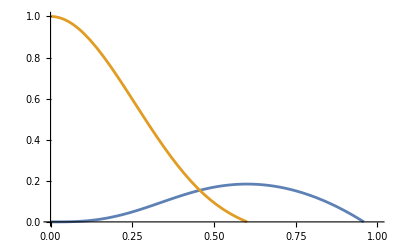

```mathematica
rmin=0.00000000000000000000000000000000001`36;
tovsolve[[1;;2]]
%/.aconf->Function[{r},1]/.K->Kval/.Γ->Γval
Map[First@#==Last@#&,%];
NDSolve[{%,m[rmin]==0,ρ[rmin]==1}//Flatten,{m,ρ},{r,rmin,1},AccuracyGoal->accdef,PrecisionGoal->precdef,WorkingPrecision->wpdef]
munco=m/.%[[1]];
ρunco=ρ/.%%[[1]];
Plot[{%%[r],%[r]},{r,0,1},PlotRange->{0,1}]
```

```mathematica
FindRoot[ρunco[r]==0,{r,0.8`36},AccuracyGoal->accdef,PrecisionGoal->precdef,WorkingPrecision->wpdef]
rsunco=%[[1,2]]
msunco=munco[rsunco]
```

{r→0.60105862487811508465060001432581958516898513822673}

0.60105862487811508465060001432581958516898513822673

0.1840879672264349437833587147264593155236675961854

#### Constructing full solution for NS (TOV ν equation)

```mathematica
massNS[r_]=Piecewise[{{munco[r],r<rsunco},{msunco ,r>=rsunco}}](*mass*)
ρNS[r_]=Piecewise[{{ρunco[r],r<rsunco},{0 ,r>=rsunco}}](*energy density*)
```

Piecewise[{{InterpolatingFunction[…][r], r<0.60105862487811508465060001432581958516898513822673}, {0.1840879672264349437833587147264593155236675961854, r≥0.60105862487811508465060001432581958516898513822673}, {0, True}}]

Piecewise[{{InterpolatingFunction[…][r], r<0.60105862487811508465060001432581958516898513822673}, {0, True}}]

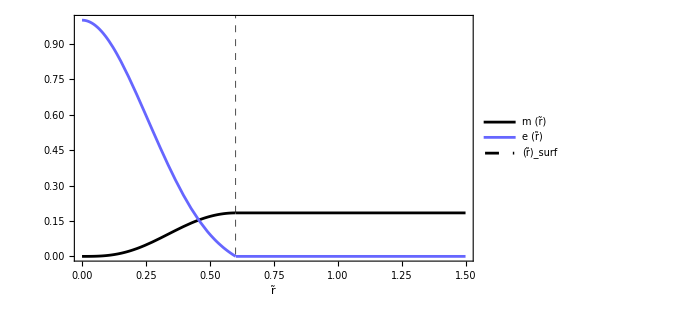

```mathematica
Plot[{massNS[r],ρNS[r],},{r,0,1.5},PlotRange->All,PlotStyle->{Black,myblue,{Black,Dashed,Thin}},ImageSize->500,Frame->True,FrameLabel->{"r̃",""},BaseStyle->{FontSize->15,FontFamily->"Times",FontColor->Black},FrameStyle->Black,AxesStyle->Black,PlotLegends->Placed[Map[Style[#,15,FontFamily->"Times",Italic]&,{"m (r̃)","e (r̃)","(r̃)_surf"}],{0.7,0.7}],GridLines->{{rsunco},{}},GridLinesStyle->Directive[Black,Dashed,Thin]]
```

```mathematica
grrNS[r_]=1/(1-2massNS[r]/r)//Evaluate
```

1/(1-1/r 2 (Piecewise[{{InterpolatingFunction[…][r], r<0.60105862487811508465060001432581958516898513822673}, {0.1840879672264349437833587147264593155236675961854, r≥0.60105862487811508465060001432581958516898513822673}, {0, True}}]))

```mathematica
νsunco=Log[(1-2msunco/r)/.r->rsunco]
```

-0.9481576231221585581569385309806982629037187782799

ν'[r]→-(2 (m[r]+4 K π r^3 ρ[r]^Γ))/(r (-r+2 m[r]))

NDSolve::mxst: Maximum number of 10000 steps reached at the point r == 1.394102008919095199989213579024103974113717673829×10^-6.

{{ν→                                                                             -6
InterpolatingFunction[{{1.394102008919095199989213579024103974113717673829 10  , 0.6010586248781150846506000143258195851689851382267}}, <>]}}

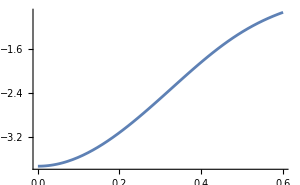
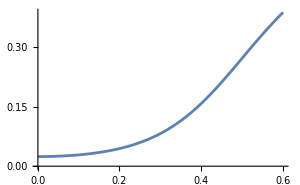

```mathematica
tovsolve[[3]]
%/.K->Kval/.Γ->Γval/.ρ->ρunco/.m->munco;
NDSolve[{First@%==Last@%,ν[rsunco]==νsunco},ν,{r,rmin,rsunco},AccuracyGoal->accdef,PrecisionGoal->precdef,WorkingPrecision->wpdef-1]
νunco=ν/.%[[1]];
{Plot[{νunco[r]},{r,0,rsunco},ImageSize->300],Plot[{Exp[νunco[r]]},{r,0,rsunco},ImageSize->300]}//Quiet
```

```mathematica
gttNS[r_]=Piecewise[{{-Exp[νunco[r]],r<rsunco},{-(1-2msunco/r) ,r>=rsunco}}]//Evaluate
```

Piecewise[{{-ⅇ^(-6
InterpolatingFunction[{{1.394102008919095199989213579024103974113717673829 10  , 0.6010586248781150846506000143258195851689851382267}}, <>][r]), r<0.60105862487811508465060001432581958516898513822673}, {-1+0.3681759344528698875667174294529186310473351923708/r, r≥0.60105862487811508465060001432581958516898513822673}, {0, True}}]

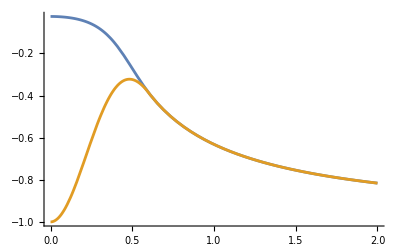

```mathematica
Plot[{gttNS[r],-1/grrNS[r]}//Evaluate,{r,0,2},PlotRange->All]//Quiet
```

(-Log[P]+Γ Log[P+(P/K)^(1/Γ)])/(-1+Γ)

(-Log[K e[r]^Γ]+Γ Log[K e[r]^Γ+(e[r]^Γ)^(1/Γ)])/(-1+Γ)

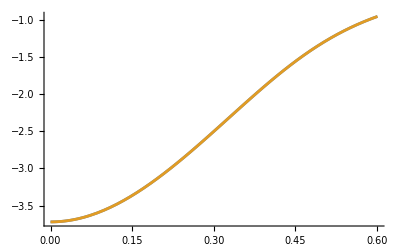

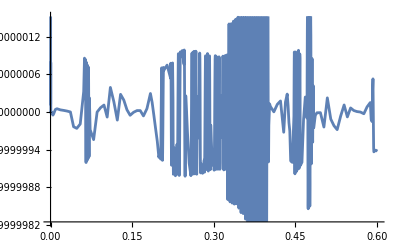

```mathematica
(*following 2503.00098[gr-qc], eq (8) and around, note that there is a factor 2 of difference between the definitions of ν*)
(*P[r]->K e[r]^Γ*)
(*H=*)Integrate[1/((P/K)^(1/Γ)+P),P]
%/.P->K e[r]^Γ//Simplify
%/.K->Kval/.Γ->Γval/.e->ρNS;
Plot[{2(Log[1-2msunco/rsunco(*C*)]/2-%),νunco[r]},{r,0,rsunco}]
Plot[{-D[%%,r]/D[2νunco[r],r]}//Evaluate,{r,0,rsunco}]
```

### 2. Transform NS to isotropic radius

#### Setting condition at infinity

rt'[r]==(√(1/(1-0.3681759344528698875667174294529186310473351923708/r)) rt[r])/r

{{rt→Function[{r},0.0920439836132174718916793573632296577618337980927 ⅇ^(2. √(1/(1.-0.3681759344528698875667174294529186310473351923708/r)) √(1.-0.3681759344528698875667174294529186310473351923708/r) ArcTanh[√(1.-0.3681759344528698875667174294529186310473351923708/r)])]}}

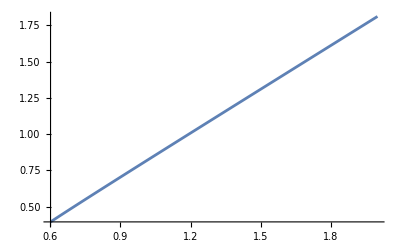

```mathematica
rt'[r]==rt[r]/r Sqrt[1/(1-2 msunco/r)]
DSolve[{%,rt'[∞]==1},rt,r]
rtofrout=%[[1,1,2]];
Plot[rtofrout[r],{r,rsunco,2}]//Quiet
```

rt'[r]==1/r √(1/(1-1/r 2 (Piecewise[{{InterpolatingFunction[…][r], r<0.60105862487811508465060001432581958516898513822673}, {0.1840879672264349437833587147264593155236675961854, r≥0.60105862487811508465060001432581958516898513822673}, {0, True}}]))) rt[r]

{{rt→                                                                           -35
InterpolatingFunction[{{1.0000000000000000000000000000000000000000000000 10   , 0.60105862487811508465060001432581958516898513823}}, <>]}}

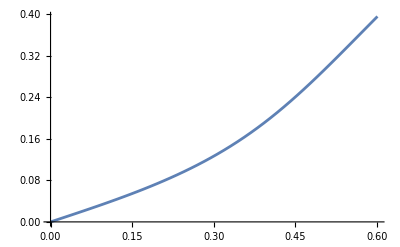

```mathematica
rt'[r]==rt[r]/r Sqrt[grrNS[r]]
NDSolve[{%,rt[rsunco]==rtofrout[rsunco]},rt,{r,rmin,rsunco},AccuracyGoal->accdef,PrecisionGoal->precdef,WorkingPrecision->wpdef-3]
rtofrin=%[[1,1,2]];
Plot[rtofrin[r],{r,0,rsunco}]//Quiet
(*ParametricPlot[{%%[[1,1,2]][r],grrNS[r]},{r,0,rsunco}]*)
```

```mathematica
rtofr[r_]=Piecewise[{{rtofrin[r],r<rsunco},{rtofrout[r] ,r>=rsunco}}](*isotropic radius in terms of non-isotropic one*)
```

Piecewise[{{-35
InterpolatingFunction[{{1.0000000000000000000000000000000000000000000000 10   , 0.60105862487811508465060001432581958516898513823}}, <>][r], r<0.60105862487811508465060001432581958516898513822673}, {0.0920439836132174718916793573632296577618337980927 ⅇ^(2. √(1/(1.-0.3681759344528698875667174294529186310473351923708/r)) √(1.-0.3681759344528698875667174294529186310473351923708/r) ArcTanh[√(1.-0.3681759344528698875667174294529186310473351923708/r)]), r≥0.60105862487811508465060001432581958516898513822673}, {0, True}}]

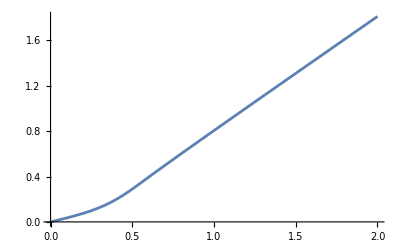

```mathematica
Plot[rtofr[r],{r,0,2}]
```

```mathematica
χNSofr[r_]=rtofr[r]^2/r^2//Evaluate
```

1/r^2(Piecewise[{{-35
InterpolatingFunction[{{1.0000000000000000000000000000000000000000000000 10   , 0.60105862487811508465060001432581958516898513823}}, <>][r], r<0.60105862487811508465060001432581958516898513822673}, {0.0920439836132174718916793573632296577618337980927 ⅇ^(2. √(1/(1.-0.3681759344528698875667174294529186310473351923708/r)) √(1.-0.3681759344528698875667174294529186310473351923708/r) ArcTanh[√(1.-0.3681759344528698875667174294529186310473351923708/r)]), r≥0.60105862487811508465060001432581958516898513822673}, {0, True}}])^2

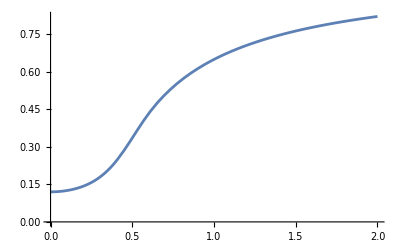
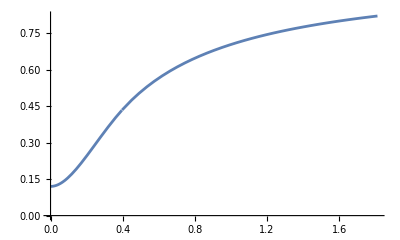

```mathematica
{Plot[χNSofr[r],{r,0,2},ImageSize->400,AxesOrigin->{0,0}],ParametricPlot[{rtofr[r],χNSofr[r]},{r,0,2},AspectRatio->0.6,ImageSize->400,AxesOrigin->{0,0}]}
```

#### Express quantities in terms of the isotropic radius: doing inner and outer part separately

```mathematica
(*use numerical solution for interior part and match to 1+mNS/(2rbar) outside*)
```

```mathematica
χout[r_]=(1+msunco/(2 r))^-4;
```

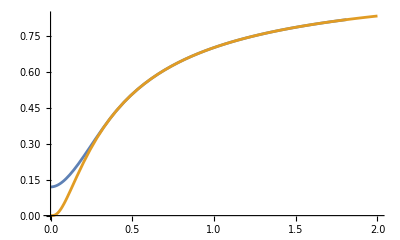

```mathematica
ParametricPlot[{{rtofr[r],χNSofr[r]},{r,χout[r]}},{r,0,2},AspectRatio->0.6,ImageSize->400,AxesOrigin->{0,0}](*check from before, now correct*)
```

```mathematica
(*determining the star's surface on the isotropic radius rt*)
FindRoot[χout[rts]==rts^2/rsunco^2,{rts,rsunco},AccuracyGoal->accdef,PrecisionGoal->precdef,WorkingPrecision->wpdef]
rsiso=rts/.%
```

{rts→0.39555226181034274336012757161652778425311422514936}

0.39555226181034274336012757161652778425311422514936

Power::infy: Infinite expression 1/0 encountered.

InterpolatingFunction::dmval: Input value {-7.0725499592181734694837991645768939288681848020613×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {riso,runco[riso]} = {0,-7.0725499592181734694837991645768939288681848020613×10^-19}.

{{runco→                                                                              -7
InterpolatingFunction[{{9.8776149472859247205403402742799661841877956844945 10  , 0.39555226181034274336012757161652778425311422514936}}, <>]}}

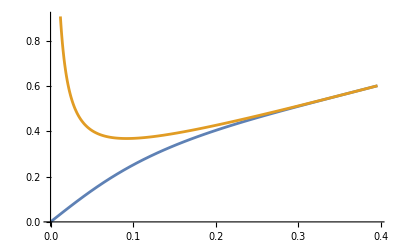

```mathematica
NDSolve[{runco'[riso]==runco[riso]/riso*Sqrt[1-2munco[runco[riso]]/runco[riso]],runco[rsiso]==rsunco},runco,{riso,0,rsiso},AccuracyGoal->accdef,PrecisionGoal->precdef,WorkingPrecision->wpdef]
Plot[{%[[1,1,2]][r],r/ Sqrt[χout[r]]},{r,0,rsiso}](*they coincide at the surface of the star, good*)
rofrtin=%%[[1,1,2]];
```

```mathematica
χNS[r_]=Piecewise[{{r^2/rofrtin[r]^2,r<rsiso},{χout[r],r>=rsiso}}]//Evaluate;
```

```mathematica
χNSpoly=InterpolatingPolynomial[Table[{x1,x1^2/rofrtin[x1]^2},{x1,Range[1,20-1]/(20-1)*rsiso}],r];
```

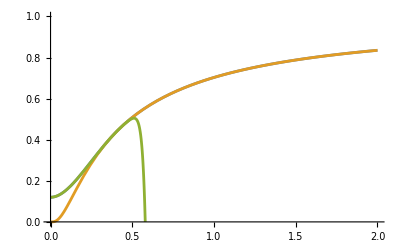

```mathematica
Plot[{χNS[r],χout[r],χNSpoly},{r,0,2},PlotRange->{0,1}]//Quiet
```

```mathematica
(*check by inverting result from the previous subsection*)
```

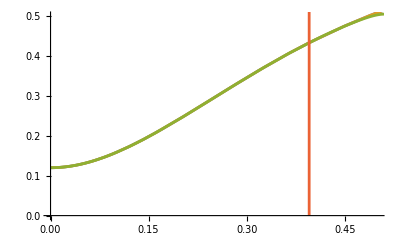

```mathematica
ParametricPlot[{{rtofr[r],χNSofr[r]},{r,χNS[r]},{r,χNSpoly},{rsiso,r}},{r,0,2},AspectRatio->0.6,ImageSize->400,PlotRange->{0,0.5}](*this should also serve as a check, I think -- ok! *)//Quiet
```

#### Calculate mass-energy density and NS metric components in isotropic radius

```mathematica
ρNSiso[r_]=ρNS[rofrtin[r]];
```

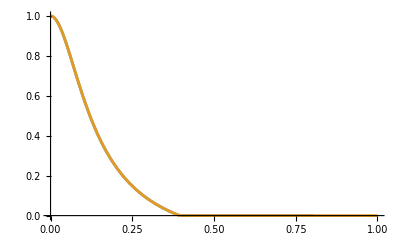

0.39555226181034274336012757161652778425311422514936

```mathematica
ParametricPlot[{{rtofr[r],ρNS[r]},{r,ρNSiso[r]}},{r,0,1},AspectRatio->0.6,ImageSize->400]//Quiet
rsiso(*surface of the star in isotropic coordinates*)
```

```mathematica
rofrt[r_]=Piecewise[{{rofrtin[r],r<rsiso},{r(1+msunco/2/r)^2 ,r>=rsiso}}](*non-isotropic radius in terms of isotropic one*)
```

Piecewise[{{-7
InterpolatingFunction[{{9.8776149472859247205403402742799661841877956844945 10  , 0.39555226181034274336012757161652778425311422514936}}, <>][r], r<0.39555226181034274336012757161652778425311422514936}, {(1+0.09204398361321747189167935736322965776183379809271/r)^2 r, r≥0.39555226181034274336012757161652778425311422514936}, {0, True}}]

```mathematica
(*not really used*)
(*gttNSiso[r_]=gttNS[rofrt[r]]//Evaluate
grrNSiso[r_]=grrNS[rofrt[r]]//Evaluate*)
```

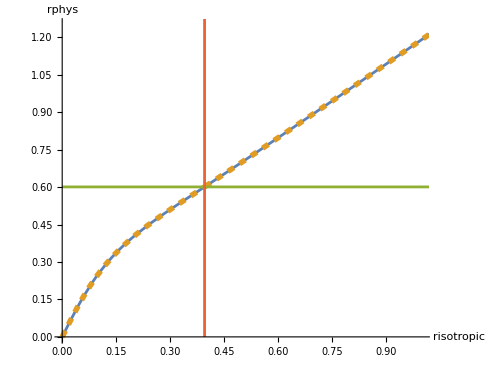

```mathematica
ParametricPlot[{(*{r,rofrtin[r]},{r,r(1+msunco/2/r)^2},*){r,rofrt[r]},{rtofr[r],r},{r,rsunco},{rsiso,r}},{r,0,2},PlotRange->{{0,1},{0,1.25}},AspectRatio->3/4,AxesLabel->{risotropic,rphys},PlotStyle->{(*{},*){},{Dashed,AbsoluteThickness[4]}(*,{Dotted,AbsoluteThickness[6]}*),{},{}},ImageSize->500]//Quiet
```

### 3. Put BH and NS together

#### Add uncompactified conformal factors

```mathematica
massBH=1/3msunco;
2massBH(*horizon radius*)
rsunco(*star surface*)
```

0.1227253114842899625222391431509728770157783974569

0.60105862487811508465060001432581958516898513822673

```mathematica
ψNS[r_]=χNS[r]^(-1/4)//Evaluate;(*includes the 1*)
ψBH[r_]=massBH/(2 r);
ψtot[r_]=ψNS[r]+ψBH[r];
```

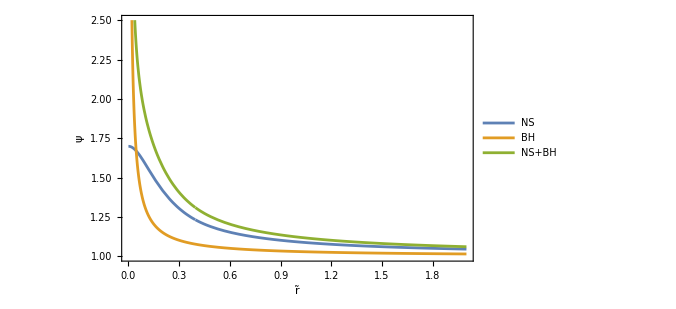
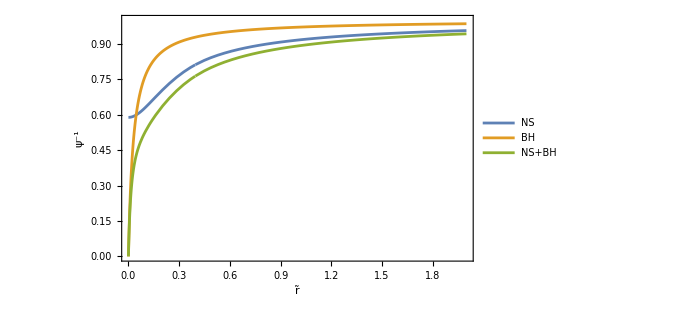
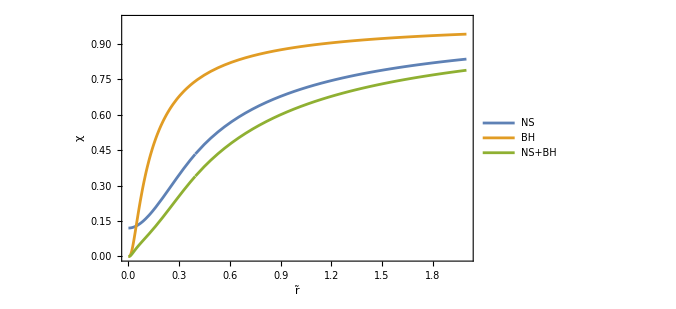

```mathematica
{Plot[{ψNS[r],1+ψBH[r],ψtot[r]},{r,0,2},PlotRange->{1,2.5},ImageSize->500,PlotLegends->Placed[{"NS","BH","NS+BH"},Above],Frame->True,FrameLabel->{"r̃","ψ"},FrameStyle->Directive[Black,FontFamily->"Times",FontSize->14]],Plot[{1/ψNS[r],1/(1+ψBH[r]),1/(ψtot[r])},{r,0,2},PlotRange->{0,1},ImageSize->500,PlotLegends->Placed[{"NS","BH","NS+BH"},Above],Frame->True,FrameLabel->{"r̃","ψ^-1"},FrameStyle->Directive[Black,FontFamily->"Times",FontSize->14]],Plot[{1/ψNS[r]^4,1/(1+ψBH[r])^4,1/(ψtot[r])^4},{r,0,2},PlotRange->{0,1},ImageSize->500,PlotLegends->Placed[{"NS","BH","NS+BH"},Above],Frame->True,FrameLabel->{"r̃","χ"},FrameStyle->Directive[Black,FontFamily->"Times",FontSize->14]]}//Quiet
```

#### Misner-Sharp mass of straightforward superposition

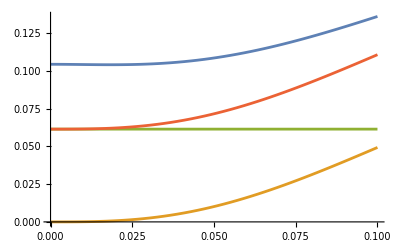
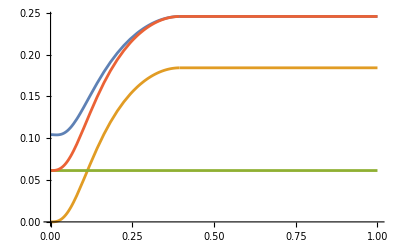

Asymptotically the Misner-Sharp mass of the superposition equals the masses of BH + NS, but at the origin its value is different.

```mathematica
msmcauchy/.χ->Function[{r},ψtot[r]^-4];
{Plot[{%,massNS[rofrtin[r]],massBH,massNS[rofrtin[r]]+massBH},{r,0,0.1},PlotRange->All,ImageSize->400],Plot[{%,massNS[rofrtin[r]],massBH,massNS[rofrtin[r]]+massBH},{r,0,1},PlotRange->All,ImageSize->400]}//Quiet
Style["Asymptotically the Misner-Sharp mass of the superposition equals the masses of BH + NS, but at the origin its value is different.",Purple,16]
```

```mathematica
Solve[2x msunco==rsunco,x];
maxfactor=%[[1,1,2]](*maximum value for which the BH horizon is smaller or equal to the NS radius*)
```

1.632530995735291476609053192478616673500276281802

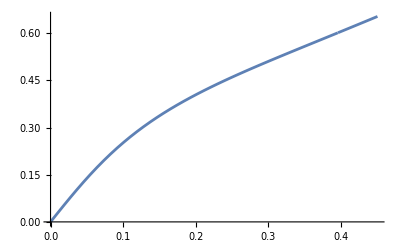
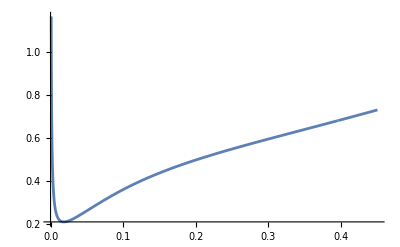
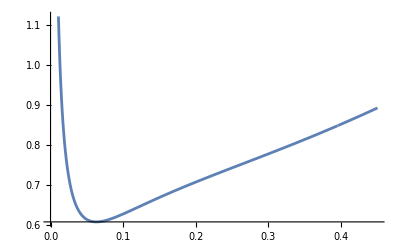
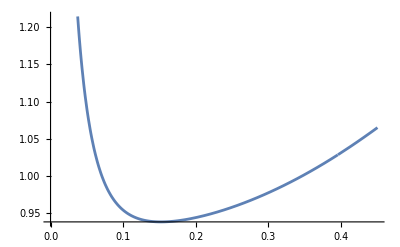

The minimum of the arial radius is the location of the horizon.

{{rts→0.018320582960610302952436021948932641080178871163769},{rts→0.062940099125159623209737255772466066345977479960791},{rts→0.1519596958090861572296343436316393934104678542254}}

{0.207922623810220068884789539151432318943905727979,0.6085696294735557031052352839785448072930929814355,0.9384363538301436342921646967939717670741628002457}

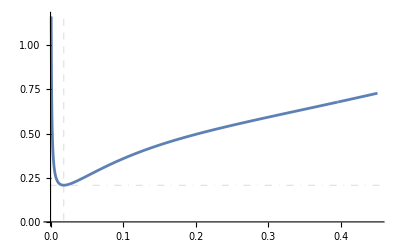
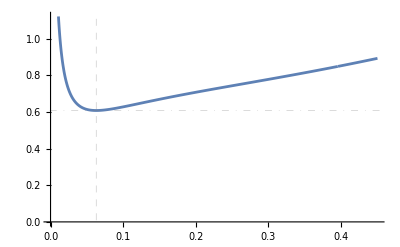
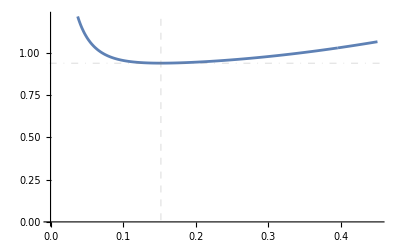

```mathematica
Map[Plot[rts(ψNS[rts]+#/(2 rts))^2,{rts,0,0.45}]&,{0,msunco/3,msunco,msunco maxfactor}]//Quiet
Style["The minimum of the arial radius is the location of the horizon.",Blue]
Map[(FindRoot[D[rts(ψNS[rts]+#/(2 rts))^2,rts]==0,{rts,0+0.01},AccuracyGoal->accdef,PrecisionGoal->precdef,WorkingPrecision->wpdef]//Evaluate)&,{msunco/3,msunco,msunco maxfactor}]//Quiet
Diagonal[Map[rts(ψNS[rts]+#/(2 rts))^2&,{msunco/3,msunco,msunco maxfactor}]/.%]
isoradiibh=%%[[;;,1,2]];
arealradiibh=%%;
masslistbh={msunco/3,msunco,msunco maxfactor};
Table[Plot[rts(ψNS[rts]+masslistbh[[i]]/(2 rts))^2,{rts,0,0.45},ImageSize->400,AxesOrigin->{0,0},GridLines->{{{isoradiibh[[i]],Directive[Dashed]}},{{arealradiibh[[i]],Directive[DotDashed]}}}],{i,1,Length@masslistbh}]
```

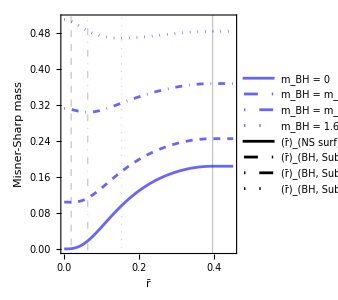

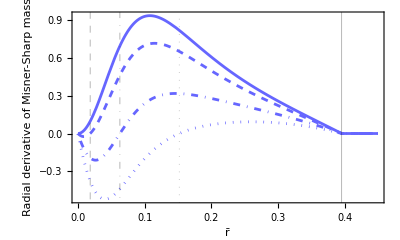

```mathematica
Map[msmcauchy/.χ->Function[{r},(ψNS[r]+#/(2 r))^-4]&,{0,msunco/3,msunco,msunco maxfactor,,,,}];
Plot[%,{r,0,0.45},PlotRange->All,ImageSize->250,Frame->True,FrameLabel->{"r̄","Misner-Sharp mass"},BaseStyle->{FontSize->12,FontFamily->"Times",FontColor->Black},FrameStyle->Black,AxesStyle->Black,PlotStyle->{myblue,{myblue,Dashed},{myblue,DotDashed},{myblue,Dotted},{Black,Thin},{Black, Dashed,Thin},{Black, DotDashed,Thin},{Black, Dotted,Thin}},PlotLegends->Placed[Map[Style[#,FontSize->12,FontFamily->"Times",FontColor->Black]&,{"m_BH = 0", "m_BH = m_NS/3","m_BH = m_NS", "m_BH = 1.63 m_NS","(r̄)_(NS surf)","(r̄)_(BH,  SubscriptBox[m, BH]  =  SubscriptBox[m, NS]/3)","(r̄)_(BH,  SubscriptBox[m, BH]  =  SubscriptBox[m, NS])","(r̄)_(BH,  SubscriptBox[m, BH]  = 1.63 SubscriptBox[m, NS])"}],Right],AspectRatio->1.2,GridLines->{{{rsiso,Directive[Black]},{isoradiibh[[1]],Directive[Black,Dashed]},{isoradiibh[[2]],Directive[Black,DotDashed]},{isoradiibh[[3]],Directive[Black,Dotted]}},{}}]
Plot[D[%%,r]//Evaluate,{r,0.0001,0.45},PlotRange->All,ImageSize->400,Frame->True,FrameLabel->{"r̄","Radial derivative of Misner-Sharp mass"},BaseStyle->{FontSize->12,FontFamily->"Times",FontColor->Black},FrameStyle->Black,AxesStyle->Black,PlotStyle->{myblue,{myblue,Dashed},{myblue,DotDashed},{myblue,Dotted},{Black,Thin},{Black, Dashed,Thin},{Black, DotDashed,Thin},{Black, Dotted,Thin}},AspectRatio->0.6,GridLines->{{{rsiso,Directive[Black]},{isoradiibh[[1]],Directive[Black,Dashed]},{isoradiibh[[2]],Directive[Black,DotDashed]},{isoradiibh[[3]],Directive[Black,Dotted]}},{}}]
(*Export["msmasslegend.pdf",%%,"PDF"]*)
```

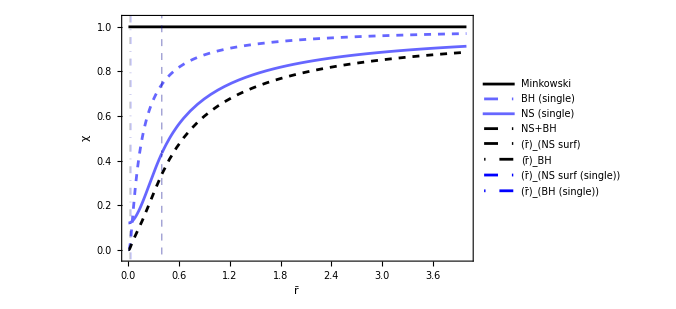

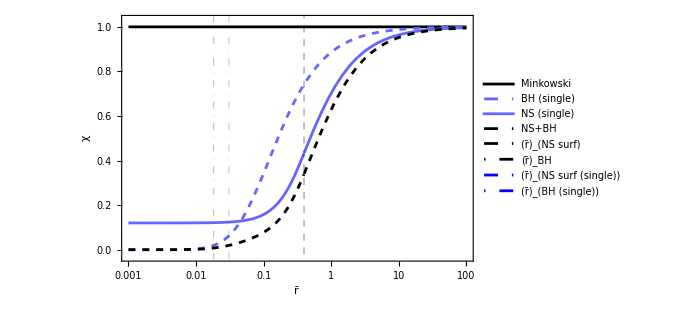

```mathematica
Plot[{1,1/(1+ψBH[r])^4,1/ψNS[r]^4,1/(ψtot[r])^4,,,,},{r,0,4},PlotRange->{-0.03,1.03},ImageSize->500,PlotStyle->{Black,{myblue,Dashed},{myblue},{Black,Dashed},Directive[Black,Dashed,Thin],Directive[Black,DotDashed,Thin],Directive[Blue,Dashed,Thin],Directive[Blue,DotDashed,Thin]},ImageSize->500,Frame->True,FrameLabel->{"r̄","χ"},BaseStyle->{FontSize->15,FontFamily->"Times",FontColor->Black},FrameStyle->Black,AxesStyle->Black,PlotLegends->Placed[Map[Style[#,15,FontFamily->"Times"]&,{"Minkowski","BH (single)","NS (single)", "NS+BH", "(r̄)_(NS surf)","(r̄)_BH","(r̄)_(NS surf (single))","(r̄)_(BH (single))"}],{0.65,0.30}],GridLines->{{{rsiso,Directive[Black,Dashed,Thin]},{isoradiibh[[1]],Directive[Black,DotDashed,Thin]},{rsiso,Directive[Blue,Dashed,Thin]},{massBH/2,Directive[Blue,DotDashed,Thin]}},{}}]//Quiet
LogLinearPlot[{1,1/(1+ψBH[r])^4,1/ψNS[r]^4,1/(ψtot[r])^4,,,,},{r,0.001,100},PlotRange->{-0.03,1.03},ImageSize->500,PlotStyle->{Black,{myblue,Dashed},{myblue},{Black,Dashed},Directive[Black,Dashed,Thin],Directive[Black,DotDashed,Thin],Directive[Blue,Dashed,Thin],Directive[Blue,DotDashed,Thin]},ImageSize->500,Frame->True,FrameLabel->{"r̄","χ"},BaseStyle->{FontSize->15,FontFamily->"Times",FontColor->Black},FrameStyle->Black,AxesStyle->Black,PlotLegends->Placed[Map[Style[#,15,FontFamily->"Times"]&,{"Minkowski","BH (single)","NS (single)", "NS+BH", "(r̄)_(NS surf)","(r̄)_BH","(r̄)_(NS surf (single))","(r̄)_(BH (single))"}],{0.84,0.43}],GridLines->{{{rsiso,Directive[Black,Dashed,Thin]},{isoradiibh[[1]],Directive[Black,DotDashed,Thin]},{rsiso,Directive[Blue,Dashed,Thin]},{massBH/2,Directive[Blue,DotDashed,Thin]}},{}}]//Quiet
```

#### BH hyperboloidal compactification

```mathematica
(*to find critical value of Ccmc and innermost achievable Schwarzschild-type radius by the trumpet*)
(9 r^4 (aconf[r]-r aconf'[r])^2)/(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6)/.Q->Qset/.Ω->Function[{r},1]/.ψ->Function[{r},1]/.aconf->Function[{r},1]/.r[]->r//Simplify
Discriminant[r^4/%,r]
Solve[0==%,Ccmc];
N[%/.Kcmc->Kcmcset/.mass->massBH/.Q->Qset,{∞,200}]//Chop;
Cases[Cases[%,{Ccmc->Except[_Complex]}],{Ccmc->Except[0]}]
Ccmcset=Last@Last@%[[2]]
N[Solve[(1/%%%%%%/.Kcmc->Kcmcset/.Ccmc->Ccmcset/.mass->massBH/.Q->Qset)==0,r, Assumptions->None],{∞,100}]//Chop;
Cases[%,{r->Except[_Complex]}]
inmstR=Last@Last@%[[1]]
```

(9 r^4)/(9 Ccmc^2+6 (Ccmc Kcmc-3 mass) r^3+9 r^4+Kcmc^2 r^6)

-64/9 Ccmc^4 Kcmc^2 (16 Ccmc^2+9 Ccmc^4 Kcmc^4-36 Ccmc^3 Kcmc^3 mass+42 Ccmc^2 Kcmc^2 mass^2+36 Ccmc Kcmc mass^3+24 Ccmc^3 Kcmc^5 mass^3-27 mass^4-108 Ccmc^2 Kcmc^4 mass^4+162 Ccmc Kcmc^3 mass^5-81 Kcmc^2 mass^6)

{{Ccmc→-0.004199240785280262513544778901032293498753083913},{Ccmc→0.005768396458482668978052964866004407949826855272}}

0.005768396458482668978052964866004407949826855272

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{r→0.09923092135540955887796625227956173137883818662},{r→0.09923092135540955887796657210920973777303154306}}

0.09923092135540955887796625227956173137883818662

(9 r^4 (aconf[r]-r aconf'[r])^2)/(Kcmc^2 r^6+9 r^4 aconf[r]^2+6 (Ccmc Kcmc-3 mass) r^3 aconf[r]^3+9 Ccmc^2 aconf[r]^6)

(r^4 (-1. aconf[r]+r aconf'[r])^2)/(r^6+r^4 aconf[r]^2-0.134262104401255300478345072882981692915432108 r^3 aconf[r]^3+0.00003327439770223539781100737388129123633982786167 aconf[r]^6)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NDSolve::precw: The precision of the differential equation ({{aconf'[r]==(0.5 (r^6+r^4 aconf[«1»]^2-0.134262104401255300478345072882981692915432108 r^3 aconf[«1»]^3+0.00003327439770223539781100737388129123633982786167 aconf[«1»]^6) ((2. r^5 aconf[r])/Plus[«4»]-(6.434242102478151696109946845868446326953477793×10^24 r^3)/(√Plus[«4»])))/r^6,aconf[1]==0},{},{},{},{}}) is less than WorkingPrecision (50.).

Power::infy: Infinite expression 1/0^6 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {r,aconf[r]} = {0,-5.9491334446752607240825521892915753791689089099685×10^-16}.

{{aconf→InterpolatingFunction[…]}}

InterpolatingFunction[…]

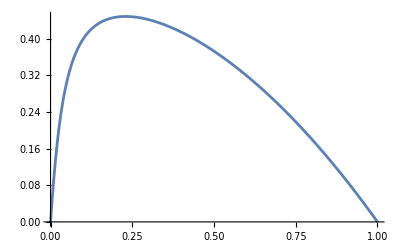

```mathematica
(*compactification factor for trumpet BH slice*)
(9 r^4 (aconf[r]-r aconf'[r])^2)/(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6)/.Q->Qset/.r[]->r//Simplify
%/.Kcmc->Kcmcset/.Ccmc->Ccmcset/.mass->massBH/.Q->Qset//Simplify
(*NDSolve[{%==1,aconf[1]==0},aconf,{r,0,1},AccuracyGoal->(*29*)15,PrecisionGoal->(*40*)20,WorkingPrecision->(*100*)50]*)
Solve[%==1,aconf'[r],Assumptions->None][[1,1]];
NDSolve[{First@%==Last@%,aconf[1]==0},aconf,{r,0,1},AccuracyGoal->15,PrecisionGoal->20,WorkingPrecision->50]
lilu=%[[1,1,2]]
Plot[{lilu[r]},{r,0,1}]
```

InterpolatingFunction::dmval: Input value {2.04286×10^-25} lies outside the range of data in the interpolating function. Extrapolation will be used.

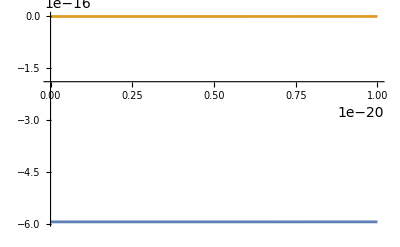

```mathematica
Prepend[Map[{#,lilu[#]}&,Range[1/100000,1,1/100000]],{0,0}];
lilulu=Interpolation[%];
Plot[{lilu[r],lilulu[r]},{r,0,0.00000000000000000001}]
```

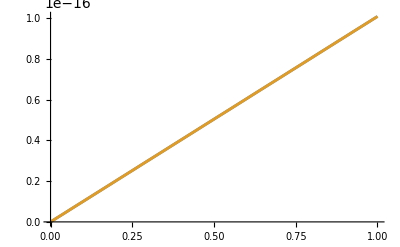

```mathematica
lilu=lilulu;
Plot[{lilulu[r],lilu[r]},{r,0,0.00000000000000001}]
```

### 4. Solve Hamiltonian constraint

#### Check that constraints are satisfied in the presence of only BH

```mathematica
solveMr/.emt->0
```

Mr[r]→0

```mathematica
solveH/.emt->0/.χ->Function[{r},(1+massset/(2 r))^-4]//Simplify
```

H[r]→0

```mathematica
msmcauchy/.χ->Function[{r},(1+mass/(2 r))^-4];
Simplify[%,Assumptions->{r∈Reals,r<0,mass∈Reals,mass>0}]
mass
Style["Misner-Sharp mass coincides with BH mass, as expected.",Blue]
```

mass

mass

Misner-Sharp mass coincides with BH mass, as expected.

#### Check that constraints are satisfied in the presence of only NS -- satisfied if ⋁=0 and W=1

Mr[r]→(8 emt π P[r] v[r] W[r]^2)/χ[r]+(8 emt π v[r] W[r]^2 ρ[r])/χ[r]

Mr[r]→(8 emt π v[r] W[r]^2 (ρ[r]+K ρ[r]^Γ))/χ[r]

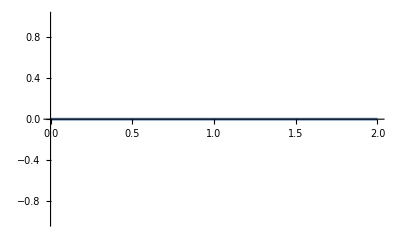

```mathematica
solveMr
%/.polyeos//Factor
%/.ρ->ρNSiso/.χ->χNS/.K->Kval/.Γ->Γval;
Last@%/.emt->1/.v[r]->0(*I believe the r component of the speed is zero on a Cauchy slice*);
Plot[%,{r,0,2},PlotRange->All]
```

H[r]→16 emt π P[r]-16 emt π P[r] W[r]^2-16 emt π W[r]^2 ρ[r]+(4 χ'[r])/r-(5 χ'[r]^2)/(2 χ[r])+2 χ''[r]

H[r]→-16 emt π W[r]^2 ρ[r]+16 emt K π ρ[r]^Γ-16 emt K π W[r]^2 ρ[r]^Γ+(4 χ'[r])/r-(5 χ'[r]^2)/(2 χ[r])+2 χ''[r]

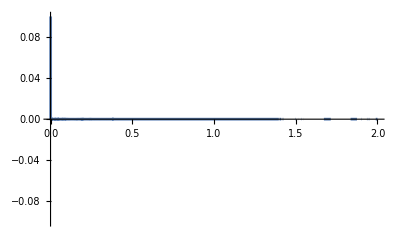

-5.61977×10^-6

```mathematica
solveH
%/.polyeos
%/.ρ->ρNSiso/.χ->χNS/.K->Kval/.Γ->Γval;
Last@%/.emt->1/.v[r]->0(*I believe the r component of the speed is zero on a Cauchy slice*)/.W[r]->α[r]u0(*index down*)/.α[r]->1/.u0->1;
Plot[%,{r,0,2},PlotRange->{-0.1,0.1}]
%%/.r->0.3
```

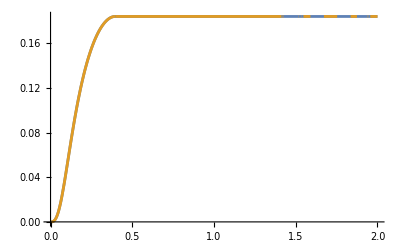
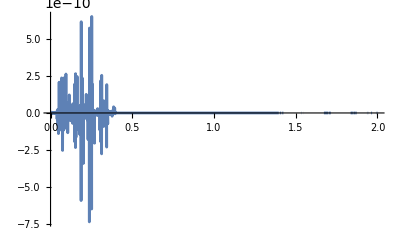

Misner-Sharp mass of NS spacetime coincides with the calculated mass of the NS.

```mathematica
msmcauchy/.χ->χNS;
{Plot[{%,massNS[rofrtin[r]]},{r,0,2},PlotRange->All,ImageSize->400],Plot[{%-massNS[rofrtin[r]]},{r,0,2},PlotRange->All,ImageSize->400]}//Quiet
Style["Misner-Sharp mass of NS spacetime coincides with the calculated mass of the NS.",Blue]
```

#### Solving the Hamiltonian constraint following the rescaling in 2102.09574

```mathematica
Heqsolve=(2 δψ'[r])/r+δψ''[r]->-2 π ((2massbh)/r+NSψ[r]+δψ[r])^5 ρ[r]-(2 NSψ'[r])/r-NSψ''[r]
%/.NSψ''[r]->-(2 NSψ'[r])/r-2 π NSρ[r] NSψ[r]^5/.ρ[r]->ρbar[r]((2massbh)/r+NSψ[r]+δψ[r])^m/.NSρ[r]->ρbar[r] NSψ[r]^m
Heqsolveresc=%/.ρbar[r]->NSρ[r] NSψ[r]^-m
Heqsolverescρ=%/.m->-6/.massbh->massBH
```

(2 δψ'[r])/r+δψ''[r]→-2 π ((2 massbh)/r+NSψ[r]+δψ[r])^5 ρ[r]-(2 NSψ'[r])/r-NSψ''[r]

(2 δψ'[r])/r+δψ''[r]→2 π NSψ[r]^(5+m) ρbar[r]-2 π ((2 massbh)/r+NSψ[r]+δψ[r])^(5+m) ρbar[r]

(2 δψ'[r])/r+δψ''[r]→2 π NSρ[r] NSψ[r]^5-2 π NSρ[r] NSψ[r]^-m ((2 massbh)/r+NSψ[r]+δψ[r])^(5+m)

(2 δψ'[r])/r+δψ''[r]→2 π NSρ[r] NSψ[r]^5-(2 π NSρ[r] NSψ[r]^6)/(0.1227253114842899625222391431509728770157783974569/r+NSψ[r]+δψ[r])

0→-2 π NSψ[r]^5 ρ[r]-(2 NSψ'[r])/r-NSψ''[r]

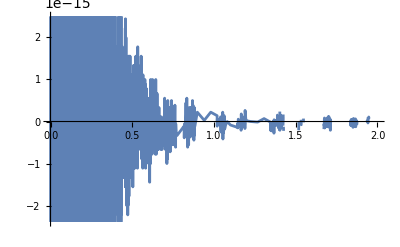

```mathematica
(*check that the single NS is a solution of the above with ρ = ρNSiso (the pressure part disappears)*)
Heqsolve/.δψ->Function[{r},0]/.massbh->0
Last@%/.ρ->ρNSiso/.NSψ->ψNS;
Plot[%,{r,0,2}]
```

InterpolatingFunction::dmval: Input value {0.3955522618103427433701275716165277701537} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.872586787512623584389570718996567643569×10^-7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 10000 steps reached at the point r == 4.181444794792855490906398324265715576813×10^-8.

{{δψ→                                                                    -8
InterpolatingFunction[{{4.181444794792855490906398324265715576813 10  , 0.3955522618103427433601275716165277842531}}, <>]}}

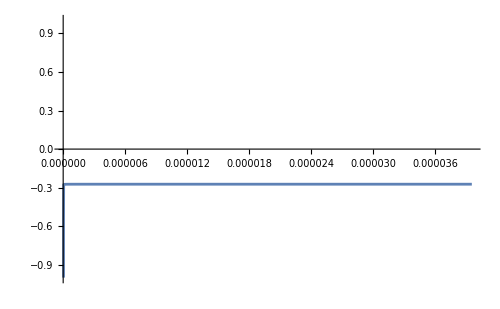
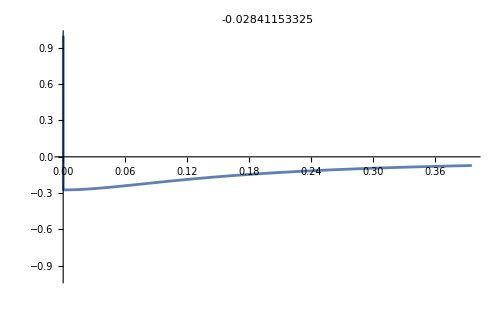
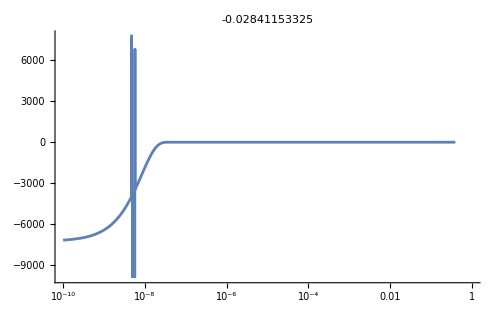

InterpolatingFunction::dmval: Input value {1/100000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.28480915686685595

-8
InterpolatingFunction[{{4.181444794792855490906398324265715576813 10  , 0.3955522618103427433601275716165277842531}}, <>]

```mathematica
Aval=-0.02841153325`50(*for massBH=msunco/3 and K=1*);
rmin=10^-12;
Heqsolverescρ/.NSρ->ρNSiso/.NSψ->ψNS;
NDSolve[{First@%==Last@%,δψ[rsiso]==A/rsiso,δψ'[rsiso]==-A/rsiso^2}/.A->Aval//Evaluate,δψ,{r,rmin,rsiso},AccuracyGoal->accdef,PrecisionGoal->precdef,WorkingPrecision->wpdef-10]
Print[{Plot[%[[1,1,2]][r],{r,(*rsiso,0.5*)0,0.0001rsiso},ImageSize->500(*,AxesOrigin->{0,0}*),PlotRange->(*Automatic*){-1,1}],Plot[%[[1,1,2]][r],{r,0,rsiso},ImageSize->500,PlotRange->{-1,1},PlotLabel->Aval],LogLinearPlot[%[[1,1,2]][r],{r,100rmin,rsiso},ImageSize->500,PlotRange->Automatic,PlotLabel->Aval]}]//Quiet
%%[[1,1,2]][10^-8]
onemoreδψ=%%%[[1,1,2]]
onemoreAval=Aval;
```

```mathematica
onemoreδψall[r_]=Piecewise[{{onemoreδψ[r],r<rsiso},{Aval/r,r>=rsiso}}];
```

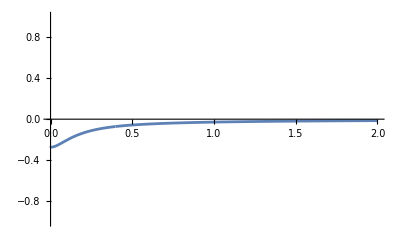

(2 δψ'[r])/r+δψ''[r]→2 π NSρ[r] NSψ[r]^5-(2 π NSρ[r] NSψ[r]^6)/(0.1227253114842899625222391431509728770157783974569/r+NSψ[r]+δψ[r])

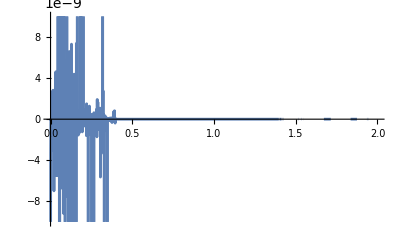

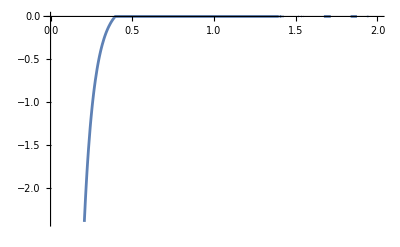

```mathematica
Plot[onemoreδψall[r],{r,0,2},PlotRange->{-1,1}]//Quiet
Heqsolverescρ
First@%-Last@%/.NSρ->ρNSiso/.NSψ->ψNS/.δψ->onemoreδψall;
Plot[%,{r,0,2},PlotRange->{-10^-8,10^-8}]//Quiet
First@%%%-Last@%%%/.NSρ->ρNSiso/.NSψ->ψNS/.δψ->Function[{r},0];
Plot[%,{r,0,2},PlotRange->Automatic]//Quiet
```

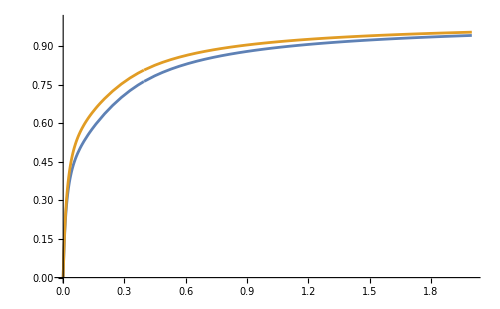
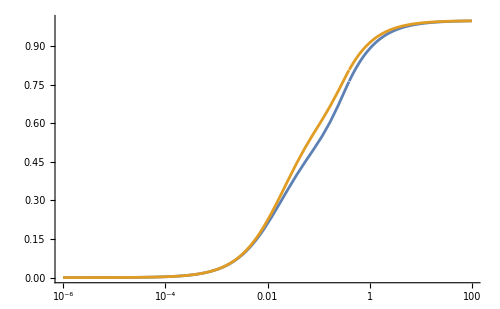

The difference with a BH comparable to the NS in terms of mass has an impact (here mbh=mns/3).

```mathematica
{Plot[{1/ψtot[r],1/(ψtot[r]+onemoreδψall[r])},{r,0,2},PlotRange->{0,1},ImageSize->500],LogLinearPlot[{1/ψtot[r],1/(ψtot[r]+onemoreδψall[r])},{r,10^-6,100},PlotRange->{0,1},ImageSize->500]}//Quiet
Style["The difference with a BH comparable to the NS in terms of mass has an impact (here mbh=mns/3).",Blue,20]
```

#### Comparing to smaller BH masses

InterpolatingFunction::dmval: Input value {0.3955522618103427433701275716165277701537} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.85373438822095934407061146116464038728×10^-7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{δψ→                                                                    -12
InterpolatingFunction[{{1.000000000000000000000000000000000000000 10   , 0.3955522618103427433601275716165277842531}}, <>]}}

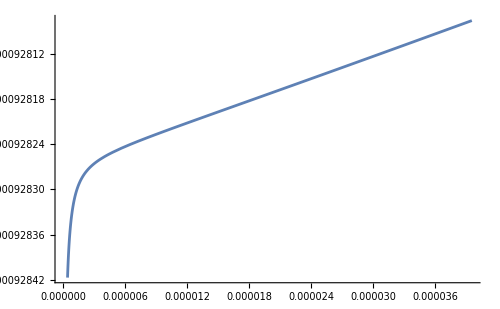
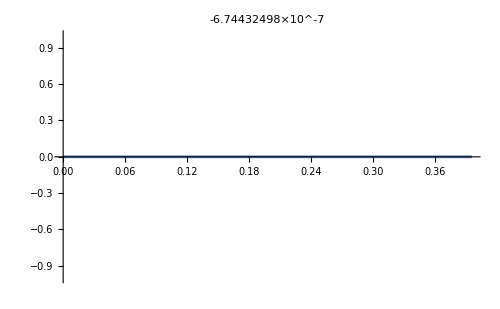
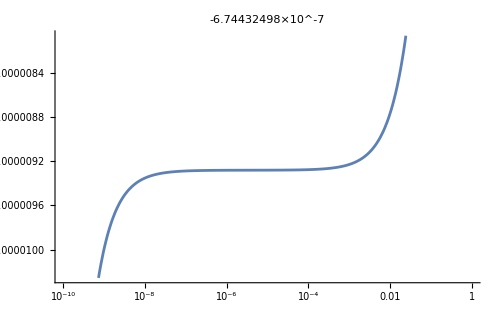

-9.35385724700375081918744089885228944549×10^-6

-12
InterpolatingFunction[{{1.000000000000000000000000000000000000000 10   , 0.3955522618103427433601275716165277842531}}, <>]

```mathematica
Aval=-0.000000674432498`50;(*changing the BH's mass changes the value of A*)
rmin=10^-12;
Heqsolveresc/.m->-6/.massbh->10^-6/.NSρ->ρNSiso/.NSψ->ψNS;
NDSolve[{First@%==Last@%,δψ[rsiso]==A/rsiso,δψ'[rsiso]==-A/rsiso^2}/.A->Aval//Evaluate,δψ,{r,rmin,rsiso},AccuracyGoal->accdef,PrecisionGoal->precdef,WorkingPrecision->wpdef-10]
Print[{Plot[%[[1,1,2]][r],{r,(*rsiso,0.5*)0,0.0001rsiso},ImageSize->500(*,AxesOrigin->{0,0}*),PlotRange->Automatic],Plot[%[[1,1,2]][r],{r,0,rsiso},ImageSize->500,PlotRange->{-1,1},PlotLabel->Aval],LogLinearPlot[%[[1,1,2]][r],{r,100rmin,rsiso},ImageSize->500,PlotRange->Automatic,PlotLabel->Aval]}]
%%[[1,1,2]][10^-8]
evensmallerbhδψ=%%%[[1,1,2]]
```

```mathematica
evensmallerbhδψall[r_]=Piecewise[{{evensmallerbhδψ[r],r<rsiso},{Aval/r,r>=rsiso}}];
```

InterpolatingFunction::dmval: Input value {0.3955522618103427433701275716165277701537} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.809387055592675405522809373533745250613×10^-7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{δψ→                                                                    -12
InterpolatingFunction[{{1.000000000000000000000000000000000000000 10   , 0.3955522618103427433601275716165277842531}}, <>]}}

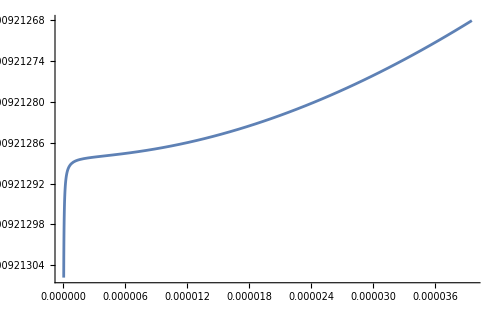
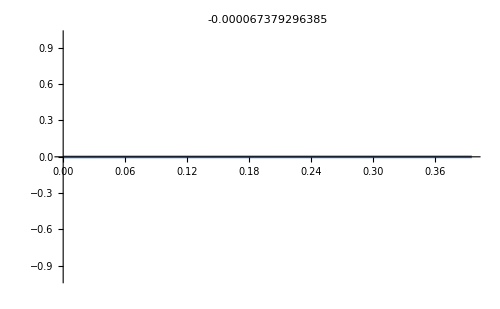
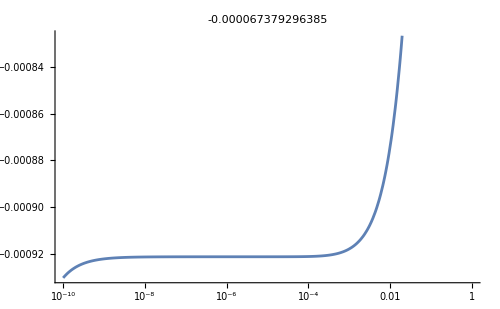

-0.000921378554046707413651878655957110962134

-12
InterpolatingFunction[{{1.000000000000000000000000000000000000000 10   , 0.3955522618103427433601275716165277842531}}, <>]

```mathematica
Aval=-0.000067379296385`50;(*changing the BH's mass changes the value of A*)
rmin=10^-12;
Heqsolveresc/.m->-6/.massbh->10^-4/.NSρ->ρNSiso/.NSψ->ψNS;
NDSolve[{First@%==Last@%,δψ[rsiso]==A/rsiso,δψ'[rsiso]==-A/rsiso^2}/.A->Aval//Evaluate,δψ,{r,rmin,rsiso},AccuracyGoal->accdef,PrecisionGoal->precdef,WorkingPrecision->wpdef-10]
Print[{Plot[%[[1,1,2]][r],{r,(*rsiso,0.5*)0,0.0001rsiso},ImageSize->500(*,AxesOrigin->{0,0}*),PlotRange->Automatic],Plot[%[[1,1,2]][r],{r,0,rsiso},ImageSize->500,PlotRange->{-1,1},PlotLabel->Aval],LogLinearPlot[%[[1,1,2]][r],{r,100rmin,rsiso},ImageSize->500,PlotRange->Automatic,PlotLabel->Aval]}]
%%[[1,1,2]][10^-8]
smallerbhδψ=%%%[[1,1,2]]
```

```mathematica
smallerbhδψall[r_]=Piecewise[{{smallerbhδψ[r],r<rsiso},{Aval/r,r>=rsiso}}];
```

InterpolatingFunction::dmval: Input value {0.3955522618103427433701275716165277701537} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.821455877767118281806753267770606117449×10^-7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{δψ→                                                                    -12
InterpolatingFunction[{{1.000000000000000000000000000000000000000 10   , 0.3955522618103427433601275716165277842531}}, <>]}}

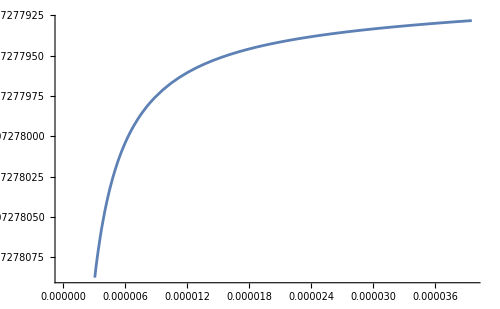
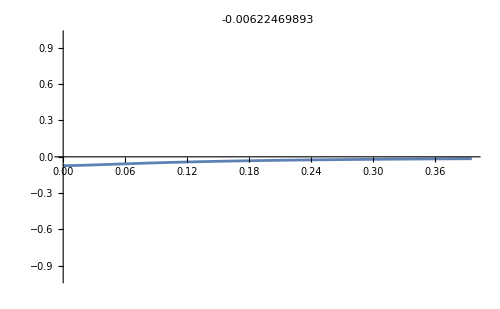
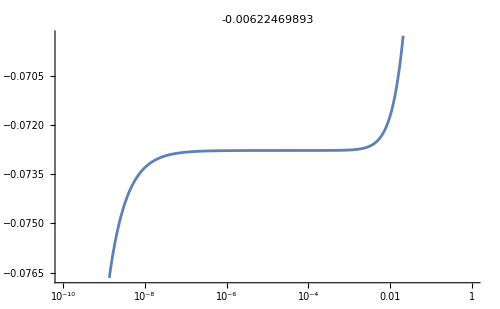

-0.0733000396261796814019362977134143648602

-12
InterpolatingFunction[{{1.000000000000000000000000000000000000000 10   , 0.3955522618103427433601275716165277842531}}, <>]

```mathematica
Aval=-0.00622469893`50;(*changing the BH's mass changes the value of A*)
rmin=10^-12;
Heqsolveresc/.m->-6/.massbh->10^-2/.NSρ->ρNSiso/.NSψ->ψNS;
NDSolve[{First@%==Last@%,δψ[rsiso]==A/rsiso,δψ'[rsiso]==-A/rsiso^2}/.A->Aval//Evaluate,δψ,{r,rmin,rsiso},AccuracyGoal->accdef,PrecisionGoal->precdef,WorkingPrecision->wpdef-10]
Print[{Plot[%[[1,1,2]][r],{r,(*rsiso,0.5*)0,0.0001rsiso},ImageSize->500(*,AxesOrigin->{0,0}*),PlotRange->Automatic],Plot[%[[1,1,2]][r],{r,0,rsiso},ImageSize->500,PlotRange->{-1,1},PlotLabel->Aval],LogLinearPlot[%[[1,1,2]][r],{r,100rmin,rsiso},ImageSize->500,PlotRange->Automatic,PlotLabel->Aval]}]
%%[[1,1,2]][10^-8]
smallbhδψ=%%%[[1,1,2]]
```

```mathematica
smallbhδψall[r_]=Piecewise[{{smallbhδψ[r],r<rsiso},{Aval/r,r>=rsiso}}];
```

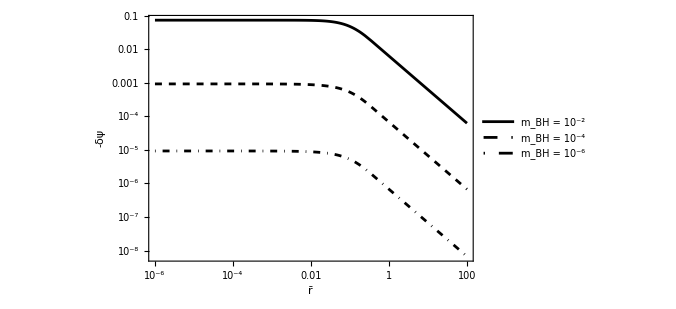

```mathematica
LogLogPlot[-{δψ[r]/.δψ->smallbhδψall,δψ[r]/.δψ->smallerbhδψall,δψ[r]/.δψ->evensmallerbhδψall}//Evaluate,{r,10^-6,100},PlotRange->All,ImageSize->500,PlotStyle->{{Black},{Black,Dashed},{Black,DotDashed}},ImageSize->500,Frame->True,FrameLabel->{"r̄","-δψ"},BaseStyle->{FontSize->15,FontFamily->"Times",FontColor->Black},FrameStyle->Black,AxesStyle->Black,PlotLegends->Placed[Map[Style[#,15,FontFamily->"Times"]&,{"m_BH = 10^-2","m_BH = 10^-4","m_BH = 10^-6"}],{0.35,0.25}]]
```

InterpolatingFunction::dmval: Input value {1.00039×10^-8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

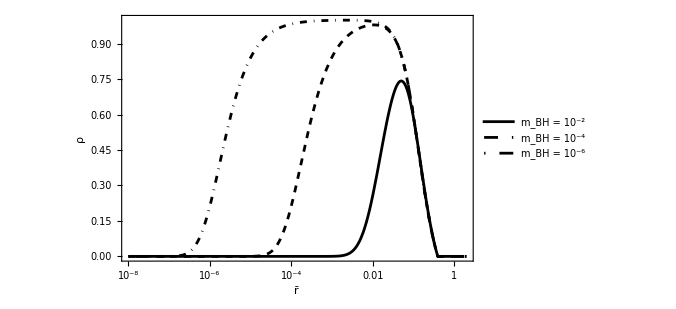

```mathematica
ρbar[r](1/(oobhmass r)+NSψ[r]+δψ[r])^m/.ρbar[r]->NSρ[r] NSψ[r]^-m/.m->-6;
%/.NSρ->ρNSiso/.NSψ->ψNS;
LogLinearPlot[{%/.oobhmass->200/.δψ->smallbhδψall,%/.oobhmass->20000/.δψ->smallerbhδψall,%/.oobhmass->2000000/.δψ->evensmallerbhδψall}//Evaluate,{r,10^-8,2},PlotRange->All,ImageSize->500,PlotStyle->{{Black},{Black,Dashed},{Black,DotDashed}},ImageSize->500,Frame->True,FrameLabel->{"r̄","ρ"},BaseStyle->{FontSize->15,FontFamily->"Times",FontColor->Black},FrameStyle->Black,AxesStyle->Black,PlotLegends->Placed[Map[Style[#,15,FontFamily->"Times"]&,{"m_BH = 10^-2","m_BH = 10^-4","m_BH = 10^-6"}],{0.18,0.80}]]
```

#### Using RK4 to check convergence

```mathematica
Heqsolverescρ/.δψ''[r]->δπ'[r]/.δψ'[r]->δπ[r];
{δψ'[r]->δπ[r],Solve[First@%==Last@%,δπ'[r]][[1,1]]//Simplify};
Collect[%,{δπ[r],δψ[r]},Simplify]
Map[Last@#&,%]/.NSρ->ρNSiso/.NSψ->ψNS;
rhsg=Collect[%,{δπ[r],δψ[r]}(*,Simplify*)]/.r->xx;
```

{δψ'[r]→δπ[r],δπ'[r]→-(2. δπ[r])/r+(NSρ[r] NSψ[r]^5 (0.7711058739371288601663357153562489392449735312+6.283185307179586476925286766559005768394338799 r δψ[r]))/(0.1227253114842899625222391431509728770157783974569+r NSψ[r]+r δψ[r])}

```mathematica
detectorirhsrk4backwards[ncells_,out_,rhsout_,inval_,finali_,db_]:=Module[{inivals,var,x,rhs,dx,invalval,dy,rhsdy,k1,k2,k3,k4},
dy=5/1;(*value to detect the growth - change as appropriate*)
rhsdy=5/1;(*value to detect the noise - change as appropriate*)
invalval=inval;
(*ncells=1000;*) dx=-(rsiso-0)/(ncells)(*//N*);
var={0,0};
inivals=(*{c+xx*xx/2*rhsg[[2]],xx*rhsg[[2]]}/.δψ[xx]->var[[1]]/.δπ[xx]->var[[2]]/.xx->x*){invalval/rsiso,-invalval/rsiso^2}//Simplify;
out={Array[0,ncells+1],Array[0,ncells+1],Array[0,ncells+1]};
rhsout={Array[0,ncells+1],Array[0,ncells+1]};
Table[out[[count,1]]=inivals[[count-1]],{count,2,Length@out}];
Table[rhsout[[count,1]]=0,{count,1,Length@rhsout}];
var=inivals;
x=rsiso;
out[[1,1]]=x;
Do[
rhs=rhsg/.δψ[xx]->var[[1]]/.δπ[xx]->var[[2]]/.xx->x;
(*If[i==2,rhs={δπ[xx],0rhsg[[2]]/.δπ->0}/.δψ[xx]->var[[1]]/.δπ[xx]->var[[2]]/.xx->x/.c->invalval];*)
k1=dx*rhs;
x=x+dx/2;
rhs=rhsg/.δψ[xx]->var[[1]]+k1[[1]]/2/.δπ[xx]->var[[2]]+k1[[2]]/2/.xx->x;
k2=dx*rhs;
rhs=rhsg/.δψ[xx]->var[[1]]+k2[[1]]/2/.δπ[xx]->var[[2]]+k2[[2]]/2/.xx->x;
k3=dx*rhs;
x=x+dx/2;
rhs=rhsg/.δψ[xx]->var[[1]]+k3[[1]]/.δπ[xx]->var[[2]]+k3[[2]]/.xx->x;
k4=dx*rhs;
var=var+(k1+2k2+2k3+k4)/6;
out[[1,i]]=x;
Table[out[[count,i]]=var[[count-1]],{count,2,Length@out}];
Table[rhsout[[count,i]]=rhs[[count]],{count,1,Length@rhsout}];
(*If[out[[3,i]]-out[[3,i-1]]>dy,(*Print[{inval,i}];*)finali=i;db=out[[2,i]];Print["Breaking at x = ",out[[1,i]], ", iteration ",i];Break[];];*)(*
If[rhsout[[2,i]]-rhsout[[2,i-1]]>rhsdy,(*Print[{inval,i}];*)finali=i;db=out[[2,i]];Break[];];*)
,{i,2,ncells+1}]]
```

Power::infy: Infinite expression 1/0. encountered.

InterpolatingFunction::dmval: Input value {-5.0807084383485447854382168771×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/0.^(1/4) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^(5/4) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{{0,0.1824983790314347289002439137899201539446181543562},{0,-0.923269654846963830961949738648790990153634456815},{0.085285079723859418234471938854328062447187,0.057471726175083147531661749716824044577555,0.02918996873166787396489445751045064223467,0.0049630261559593198871900358306799495503},{27.856616206165078964415224634341889955997,28.432353075770863841120178748453423173127,28.71970298955849781052202662445008923936,Indeterminate}}

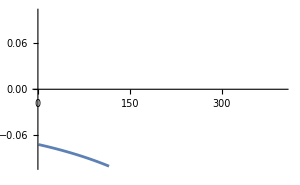
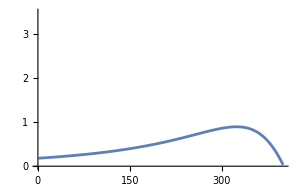

δψ at the origin = -0.2732037442692099948629356117580532254984244, at 0.

```mathematica
Clear@out;Clear@rhsout;Clear@finali;Clear@db;
ncells=400;
numbr=Aval;
detectorirhsrk4backwards[ncells,out,rhsout,numbr,finali,db];
Print[{rhsout[[1,1;;2]],rhsout[[2,1;;2]],rhsout[[1,Length@rhsout[[2]]-3;;]],rhsout[[2,Length@rhsout[[2]]-3;;]]}];
Print[{ListLinePlot[out[[2]],PlotRange->{{0,ncells},{-0.1,0.1}}, ImageSize->300],ListLinePlot[out[[3]],PlotRange->{{0,ncells},{0,3.5}}(*{{1,ncells},Automatic}*), ImageSize->300]}]//Quiet
Print["δψ at the origin = ",out[[2,ncells+1]],", at ",out[[1,ncells+1]]]
```

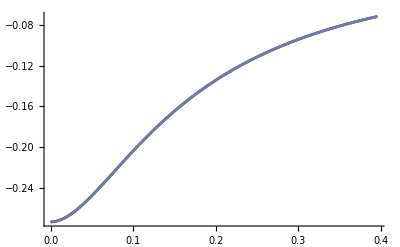

```mathematica
Show[Plot[onemoreδψ[r],{r,0.00001,rsiso},PlotStyle->Red],ListLinePlot[Transpose@out[[1;;2,;;]]]]
```

```mathematica
(*out100=out;*)
```

```mathematica
(*out200=out;*)
```

```mathematica
(*out400=out;*)
```

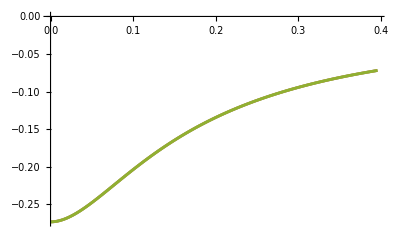

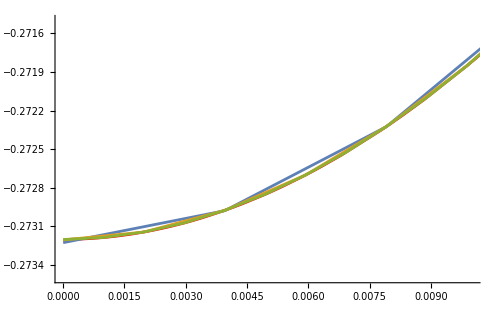
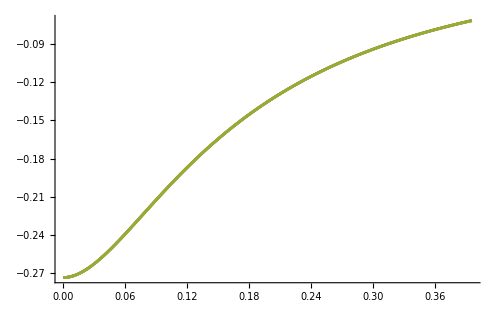

```mathematica
ListLinePlot[{Transpose@out100[[1;;2,;;]],Transpose@out200[[1;;2,;;]],Transpose@out400[[1;;2,;;]]},PlotRange->All]
{Show[Plot[onemoreδψ[r],{r,0.00001,rsiso},PlotStyle->Red,PlotRange->All],%,PlotRange->{{0,0.01},{-0.2735,-0.2715}},ImageSize->500],Show[Plot[onemoreδψ[r],{r,0.00001,rsiso},PlotStyle->Red,PlotRange->All],%,PlotRange->Automatic,ImageSize->500]}
```

```mathematica
interporder=6;
int100=Interpolation[Transpose@out100[[1;;2,;;]],InterpolationOrder->interporder];
int200=Interpolation[Transpose@out200[[1;;2,;;]],InterpolationOrder->interporder];
int400=Interpolation[Transpose@out400[[1;;2,;;]],InterpolationOrder->interporder];
```

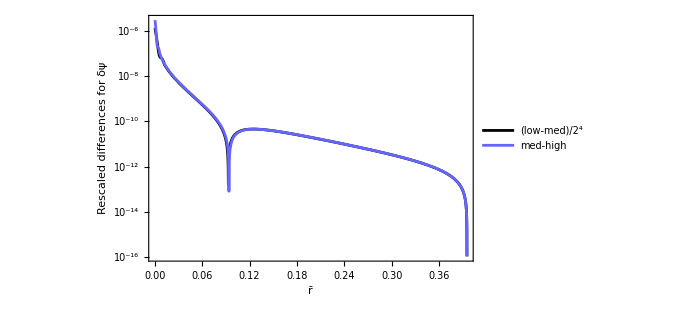

```mathematica
(*100, 200 and 400 points*)
LogPlot[Abs@{(int100[r]-int200[r])/2^4,int200[r]-int400[r]}//Evaluate,{r,0,rsiso},PlotRange->All,PlotStyle->{Black,myblue},ImageSize->500,Frame->True,FrameLabel->{"r̄","Rescaled differences for δψ"},BaseStyle->{FontSize->15,FontFamily->"Times",FontColor->Black},FrameStyle->Black,AxesStyle->Black,PlotLegends->Placed[Map[Style[#,15,FontFamily->"Times"]&,{"(low-med)/2^4","med-high"}],{0.7,0.7}]]
```

### 5. Hyperboloidal construction for NS

#### Hyperboloidalization

Outside:

```mathematica
partout[rp_]:=-Kcmc/3*rp-Ccmc/rp^2
```

Inside:

```mathematica
npoints=200;
Timing[partinpoints=Table[N[{rp,-1/rp^2(NIntegrate[Kcmcset Sqrt[Exp[νunco[r]]1/(1-2munco[r]/r)] r^2,{r,0,rp},AccuracyGoal->accdef,PrecisionGoal->precdef,WorkingPrecision->wpdef]+Ccmcin)/.Ccmcin->0(*choice here: seems to work, but I may want to change it*)}/.rp->0+ci(rsunco-0)/npoints,{(*precdef*)Infinity,5accdef}],{ci,1,npoints}];]
partinpoints=Prepend[partinpoints,N[{rp,-1/rp^2(NIntegrate[Kcmcset Sqrt[Exp[νunco[r]]1/(1-2munco[r]/r)] r^2,{r,0,rp},AccuracyGoal->accdef,PrecisionGoal->precdef,WorkingPrecision->wpdef]+Ccmcin)/.Ccmcin->0(*choice here: seems to work, but I may want to change it*)}/.rp->10^-36//Evaluate,{(*precdef*)Infinity,5accdef}]];
partininter=Interpolation[partinpoints]
```

NIntegrate::nlim: r = rp is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.4656867292920871185104370196772698708529355377964690830152449659704870607582661221251397780114415682}. NIntegrate obtained -0.06453336371666470591477309057081866390831868567880084681475642875697929831384971872115806133204036709 and 1.127185881365251383261888522523872655017998688734885501318795741505809467624969506961236475775527462×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.4006363036138295749844546756330907794856737125378440837596456067688245559090276276544996486055305388}. NIntegrate obtained -0.1273127692040907313005149506475886033123815732860299490252659722400116171033914836625197503331723077 and 1.114444023191903132154299197940985924666049151134062485841664781261843611420484203386056514055151091×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.4669933692490761309035714265387058283138878438215183787896028827212624021464614667953563055480008145}. NIntegrate obtained -0.1509521933917419779384468918485447578051680996347775992631049601498107601838855159067939702183664514 and 1.374757049621963862401179871773946895734797459135720652133717614938187121095333599597443238571680085×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{94.385,Null}

NIntegrate::nlim: r = rp is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

InterpolatingFunction[…]

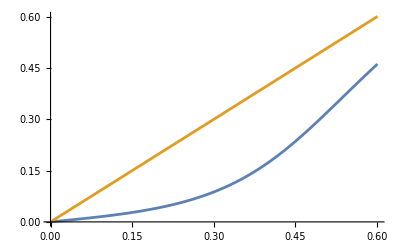

```mathematica
(*comparison with Minkowski*)
Plot[{partininter[r],-Kcmcset/3 r},{r,0,rsunco}]//Quiet
```

```mathematica
(*height function inside*)
hpin[rp_]:=partininter[rp]/Sqrt[(1-2munco[rp]/rp)Exp[νunco[rp]](Exp[νunco[rp]]+partininter[rp]^2)]
```

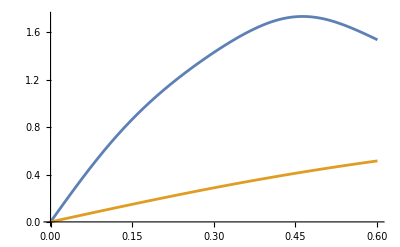

```mathematica
(*comparison with Minkowski*)
Plot[{hpin[r],r/Sqrt[(3/Kcmcset)^2+r^2]},{r,0,rsunco}]//Quiet
```

```mathematica
(*height function outside*)
hpout[rp_]=partout[rp]/(1-2msunco/rp)/Sqrt[((1-2msunco/rp)+partout[rp]^2)]/.Kcmc->Kcmcset//Evaluate;
```

```mathematica
(*joining inside and outside parts of height function*)
Solve[hpout[rsunco]==hpin[rsunco],Ccmc]
hpout[rp_]=hpout[rp]/.%[[1,1]](*choosing value of Ccmc so it coincices at the star's surface with hpin*)
CcmcoutNS=%%[[1,1,2]]
```

{{Ccmc→0.0503188396340561671666177424935846649130481432}}

(-0.0503188396340561671666177424935846649130481432/rp^2+rp)/((1-0.3681759344528698875667174294529186310473351923708/rp) √(1-0.3681759344528698875667174294529186310473351923708/rp+(-0.0503188396340561671666177424935846649130481432/rp^2+rp)^2))

0.0503188396340561671666177424935846649130481432

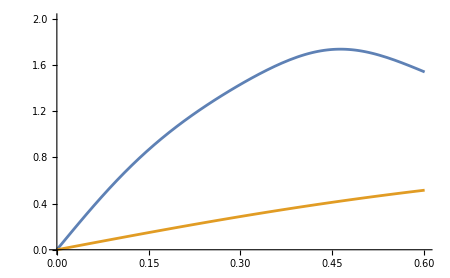
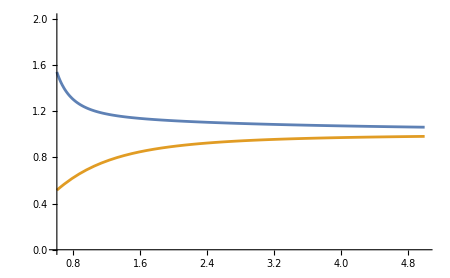

```mathematica
(*comparison with Minkowski*)
{Plot[{hpin[r],r/Sqrt[(3/Kcmcset)^2+r^2]},{r,0,rsunco},ImageSize->450,PlotRange->{0,2}],Plot[{hpout[r],r/Sqrt[(3/Kcmcset)^2+r^2]},{r,rsunco,5},ImageSize->450,PlotRange->{0,2}]}//Quiet
```

```mathematica
hpNS[r_]=Piecewise[{{hpin[r],r<rsunco},{hpout[r] ,r>=rsunco}}];
```

```mathematica
(*calculating hypoerboloidalized trumpet for BH with the same mass as the NS*)
(9 r^4 (aconf[r]-r aconf'[r])^2)/(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6)/.Q->Qset/.Ω->Function[{r},1]/.ψ->Function[{r},1]/.aconf->Function[{r},1]/.r[]->r//Simplify
Discriminant[r^4/%,r](*/Kcmc^2/.Kcmc->Kcmcset*)
Solve[0==%,Ccmc];
N[%/.Kcmc->Kcmcset/.mass->msunco/.Q->Qset,{∞,200}]//Chop;
Cases[Cases[%,{Ccmc->Except[_Complex]}],{Ccmc->Except[0]}]
CcmcsetNS=Last@Last@%[[2]]
N[Solve[(1/%%%%%%/.Kcmc->Kcmcset/.Ccmc->CcmcsetNS/.mass->msunco/.Q->Qset)==0,r, Assumptions->None],{∞,100}]//Chop;
Cases[%,{r->Except[_Complex]}]
inmstRNS=Last@Last@%[[1]]
```

(9 r^4)/(9 Ccmc^2+6 (Ccmc Kcmc-3 mass) r^3+9 r^4+Kcmc^2 r^6)

-64/9 Ccmc^4 Kcmc^2 (16 Ccmc^2+9 Ccmc^4 Kcmc^4-36 Ccmc^3 Kcmc^3 mass+42 Ccmc^2 Kcmc^2 mass^2+36 Ccmc Kcmc mass^3+24 Ccmc^3 Kcmc^5 mass^3-27 mass^4-108 Ccmc^2 Kcmc^4 mass^4+162 Ccmc Kcmc^3 mass^5-81 Kcmc^2 mass^6)

{{Ccmc→-0.029085191212921837412661942297456229256433731816},{Ccmc→0.0729822637042658067421923307500629233019361563382}}

0.0729822637042658067421923307500629233019361563382

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{r→0.331139502670469694614425742744408479490464988299},{r→0.331139502670469694614425895400247722800694945641}}

0.331139502670469694614425742744408479490464988299

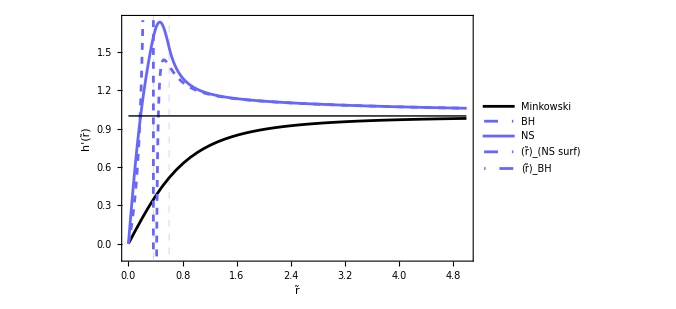

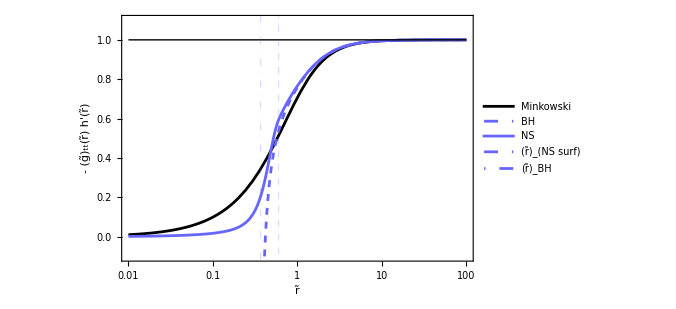

```mathematica
Plot[{(*1**)r/Sqrt[(3/Kcmcset)^2+r^2],(*(1-(2 mass)/r) *)(-Ccmc/r^2-(Kcmc r)/3)/((1-(2 mass)/r) √(1-(2 mass)/r+(Ccmc/r^2+(Kcmc r)/3)^2))/.Kcmc->Kcmcset/.Ccmc->CcmcsetNS/.mass->msunco(*using msunco as mass for the bh to plot here as test*),(*-gttNS[r]*)hpNS[r](*,1/grrNS[r]hpNS[r] same thing asymptotically*),,,1},{r,0,5},PlotRange->{-0.1,1.75},ImageSize->500,PlotStyle->{{Black},{myblue,Dashed},{myblue},Directive[myblue,Dashed,Thin],Directive[myblue,DotDashed,Thin],{Black, Thin}},ImageSize->500,Frame->True,FrameLabel->{"r̃","h'(r̃)"},BaseStyle->{FontSize->15,FontFamily->"Times",FontColor->Black},FrameStyle->Black,AxesStyle->Black,PlotLegends->Placed[Map[Style[#,15,FontFamily->"Times"]&,{"Minkowski","BH","NS","(r̃)_(NS surf)","(r̃)_BH"}],{0.84,0.3}],GridLines->{{{rsunco,Directive[myblue,Dashed,Thin]},{2msunco,Directive[myblue,DotDashed,Thin]}},{}}]
LogLinearPlot[{1*r/Sqrt[(3/Kcmcset)^2+r^2],(1-(2 mass)/r) (-Ccmc/r^2-(Kcmc r)/3)/((1-(2 mass)/r) √(1-(2 mass)/r+(Ccmc/r^2+(Kcmc r)/3)^2))/.Kcmc->Kcmcset/.Ccmc->CcmcsetNS/.mass->msunco(*using msunco as mass for the bh to plot here as test*),-gttNS[r]hpNS[r](*,1/grrNS[r]hpNS[r] same thing asymptotically*),,,1},{r,0.01,100},PlotRange->{-0.1,1.1},ImageSize->500,PlotStyle->{{Black},{myblue,Dashed},{myblue},Directive[myblue,Dashed,Thin],Directive[myblue,DotDashed,Thin],{Black, Thin}},ImageSize->500,Frame->True,FrameLabel->{"r̃","- (g̃)_tt(r̃) h'(r̃)"},BaseStyle->{FontSize->15,FontFamily->"Times",FontColor->Black},FrameStyle->Black,AxesStyle->Black,PlotLegends->Placed[Map[Style[#,15,FontFamily->"Times"]&,{"Minkowski","BH","NS","(r̃)_(NS surf)","(r̃)_BH"}],{0.78,0.35}],GridLines->{{{rsunco,Directive[myblue,Dashed,Thin]},{2msunco,Directive[myblue,DotDashed,Thin]}},{}}]
```

#### Compactification

InterpolatingFunction::dmval: Input value {0.6010659509062693611491445958745186399767461524187} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 10000 steps reached at the point r == 0.99999553066252654592673183765496357227034638203521.

{{aconf→                                                                              -6
InterpolatingFunction[{{1.0000000000000000000000000000000000000000000000000 10  , 0.99999553066252654592673183765496357227034638203521}}, <>]}}

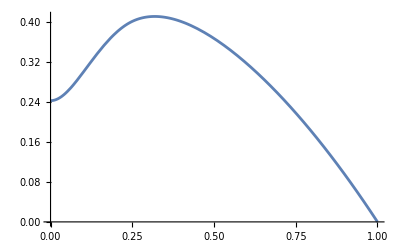

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

-9.710097781389676806561512728877964602557×10^-8

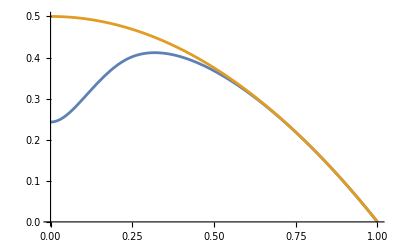

```mathematica
(grrNS[rp]+gttNS[rp] hpNS[rp]^2/.rp->r/aconf[r])(aconf[r]-r aconf'[r])^2/aconf[r]^2;(*choosing compactification imposing and initial conformally flat metric, as usual*)
Solve[%==1,aconf'[r],Assumptions->None][[1,1]];
NDSolve[{First@%==Last@%,aconf[10^-6]==0.243038`50},aconf,{r,10^-6,1},AccuracyGoal->accdef,PrecisionGoal->precdef,WorkingPrecision->wpdef](*here increased the value of the smallest r from 10^-20 to 10^-6 so that it is covered by the functions*)
Plot[%[[1,1,2]][r],{r,0,1},AxesOrigin->{0,0}]
%%[[1,1,2]][1]
aconfNS=%%%[[1,1,2]];
Plot[{aconfNS[r],-Kcmcset(1-r^2)/6},{r,0,1},PlotRange->{0,-Kcmcset/6}](*comparison with Minkowski*)
```

(9 r^4 (aconf[r]-r aconf'[r])^2)/(Kcmc^2 r^6+9 r^4 aconf[r]^2+6 (Ccmc Kcmc-3 mass) r^3 aconf[r]^3+9 Ccmc^2 aconf[r]^6)

(r^4 (-1. aconf[r]+r aconf'[r])^2)/(r^6+r^4 aconf[r]^2-0.514140461861401501051102090953044477651207505047 r^3 aconf[r]^3+0.00532641081539899415512203430499915566621422022628 aconf[r]^6)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NDSolve::precw: The precision of the differential equation ({{aconf'[r]==(0.5 (r^6+r^4 aconf[«1»]^2-0.514140461861401501051102090953044477651207505047 r^3 aconf[«1»]^3+0.00532641081539899415512203430499915566621422022628 aconf[«1»]^6) ((2. r^5 aconf[r])/Plus[«4»]-(1.8458219390224735250068693117207286656754718934×10^25 r^3)/(√Plus[«4»])))/r^6,aconf[1]==0},{},{},{},{}}) is less than WorkingPrecision (50.).

Power::infy: Infinite expression 1/0^6 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {r,aconf[r]} = {0,-1.0040606618913293650806664570093160094581362468784×10^-15}.

{{aconf→InterpolatingFunction[…]}}

InterpolatingFunction[…]

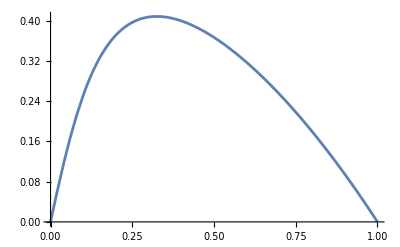

```mathematica
(*equivalent compactification for a hyperboloidal trumpet of a BH with the same mass as the NS*)
(9 r^4 (aconf[r]-r aconf'[r])^2)/(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6)/.Q->Qset/.r[]->r//Simplify
%/.Kcmc->Kcmcset/.Ccmc->CcmcsetNS/.mass->msunco/.Q->Qset//Simplify
(*NDSolve[{%==1,aconf[1]==0},aconf,{r,0,1},AccuracyGoal->(*29*)15,PrecisionGoal->(*40*)20,WorkingPrecision->(*100*)50]*)
Solve[%==1,aconf'[r],Assumptions->None][[1,1]];
NDSolve[{First@%==Last@%,aconf[1]==0},aconf,{r,0,1},AccuracyGoal->15,PrecisionGoal->20,WorkingPrecision->50]
liluNS=%[[1,1,2]]
Plot[{liluNS[r]},{r,0,1}]
```

```mathematica
FindRoot[rsunco==r/aconfNS[r],{r,0.3}]
rsNScomp=%[[1,2]](*location of the NS surface in terms of the compactified radius*)
FindRoot[2msunco==r/liluNS[r],{r,0.3}]
rBHcomp=%[[1,2]](*location of the BH horizon in terms of the compactified radius*)
```

{r→0.239413}

0.239413

{r→0.0710058}

0.0710058

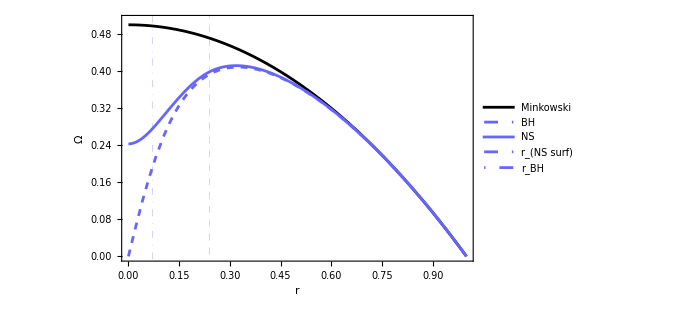

```mathematica
Plot[{-Kcmcset(1-r^2)/6,liluNS[r],aconfNS[r],,},{r,0,1},PlotRange->{0,0.51},ImageSize->500,PlotStyle->{{Black},{myblue,Dashed},{myblue},Directive[myblue,Dashed,Thin],Directive[myblue,DotDashed,Thin]},ImageSize->500,Frame->True,FrameLabel->{"r","Ω̄"},BaseStyle->{FontSize->15,FontFamily->"Times",FontColor->Black},FrameStyle->Black,AxesStyle->Black,PlotLegends->Placed[Map[Style[#,15,FontFamily->"Times"]&,{"Minkowski","BH","NS","r_(NS surf)","r_BH"}],{0.40,0.35}],GridLines->{{{rsNScomp,Directive[myblue,Dashed,Thin]},{rBHcomp,Directive[myblue,DotDashed,Thin]}},{}}]
```

### 6. Hyperboloidal construction for superposition

#### Change from isotropic to Schwarzschild radial coordinate for Schwarzschild

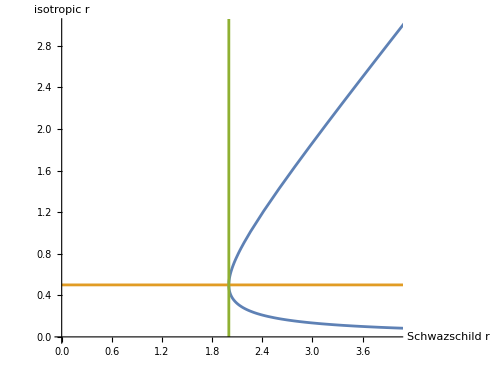

```mathematica
ParametricPlot[{{r(1+mass/2/r)^2,r},{r,mass/2},{2mass,r}}/.mass->1//Evaluate,{r,0,10},ImageSize->500,PlotRange->{{0,4},{0,3}},AxesLabel->{"Schwazschild r", "isotropic r"},AspectRatio->3/4]
```

```mathematica
Solve[riso(1+mass/2/riso)^2==r(*Schwarzschild radial coordinate*),riso(*isotropic radial coordinate*)]
```

{{riso→1/2 (-mass+r-√(-2 mass r+r^2))},{riso→1/2 (-mass+r+√(-2 mass r+r^2))}}

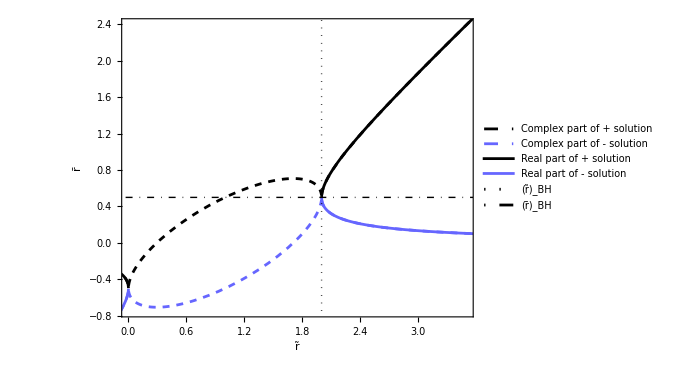

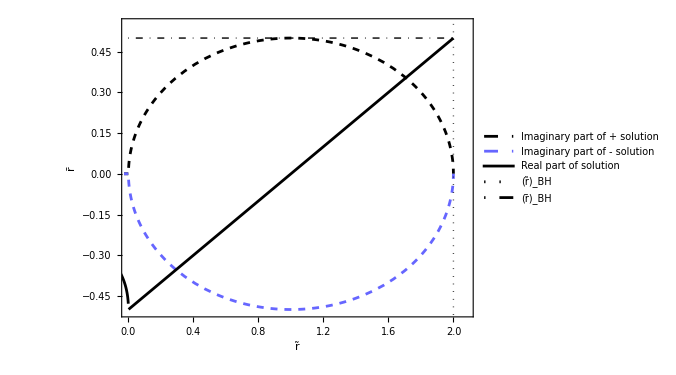

```mathematica
ParametricPlot[{{r,Map[Re@#+Im@#&,1/2 (-mass+r+√(-2 mass r+r^2))]},{r,Map[Re@#+Im@#&,1/2 (-mass+r-√(-2 mass r+r^2))]},{r,1/2 (-mass+r+√(-2 mass r+r^2))},{r,1/2 (-mass+r-√(-2 mass r+r^2))},{2mass,r},{r,mass/2}}/.mass->1//Evaluate,{r,-1,4},ImageSize->500,PlotRange->{{0,3.5},{-0.75,2.4}},AspectRatio->3/4,PlotStyle->{{Black,Dashed},{myblue,Dashed},{Black},{myblue},Directive[Black,Dotted,Thin],Directive[Black,DotDashed,Thin]},ImageSize->500,Frame->True,FrameLabel->{"r̃","r̄"},BaseStyle->{FontSize->15,FontFamily->"Times",FontColor->Black},FrameStyle->Black,AxesStyle->Black,PlotLegends->Placed[Map[Style[#,15,FontFamily->"Times"]&,{"Complex part of + solution","Complex part of - solution","Real part of + solution","Real part of - solution","(r̃)_BH","(r̄)_BH"}],{0.39,0.74}]]
ParametricPlot[{{r,Im[1/2 (-mass+r+√(-2 mass r+r^2))]},{r,Im[1/2 (-mass+r-√(-2 mass r+r^2))]},{r,Map[Re@#&,1/2 (-mass+r+√(-2 mass r+r^2))]},{2mass,r},{r,mass/2}}/.mass->1//Evaluate,{r,-1,2},ImageSize->500,PlotRange->{{0,2.08},{-0.506,0.55}},AspectRatio->3/4,PlotStyle->{{Black,Dashed},{myblue,Dashed},{Black},Directive[Black,Dotted,Thin],Directive[Black,DotDashed,Thin]},ImageSize->500,Frame->True,FrameLabel->{"r̃","r̄"},BaseStyle->{FontSize->15,FontFamily->"Times",FontColor->Black},FrameStyle->Black,AxesStyle->Black,PlotLegends->Placed[Map[Style[#,15,FontFamily->"Times"]&,{"Imaginary part of + solution","Imaginary part of - solution","Real part of solution","(r̃)_BH","(r̄)_BH"}],{0.34,0.53}]]
```

#### Transforming from isotropic to areal radial coordinate for the superposition

```mathematica
δψsol=onemoreδψall;Avalsol=onemoreAval;
```

```mathematica
δψsolpoly=InterpolatingPolynomial[Table[{x1,δψsol[x1]},{x1,Range[1,20-1]/(20-1)*rsiso}],r];
```

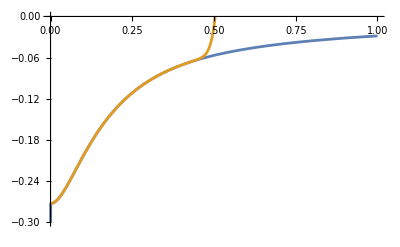

```mathematica
Plot[{δψsol[r],δψsolpoly},{r,0,1},PlotRange->{-0.3,0}]
```

```mathematica
rsuncofromisodp=(ψtot[rsiso]+δψsol[rsiso])^2 rsiso(*location of the NS surface in terms of the areal-like coordinate for the superposition*)
```

0.6066675894880070347992882367900098428777367653056

```mathematica
FindRoot[(1/((ψtot[r]+δψsol[r])/(2D[ψtot[r]+δψsol[r],r]r+ψtot[r]+δψsol[r]))^2//Evaluate)==0,{r,2/100},AccuracyGoal->accdef,PrecisionGoal->precdef,WorkingPrecision->wpdef]
newrjoindp=%[[1,2]](*location of the horizon for the isotropic radius -- grr_BH changes sign before and after if expressed in terms of the non-isotropic radius*)
newruncodp=(ψtot[r]+δψsol[r])^2 r/.%%[[1]](*ocation of the horizon of the BH part for the areal (non-isotropic) radius -- grr_BH changes sign before and after*)
N[{{massBH/2,2massBH},{newrjoindp,newruncodp},{msmcauchy/2/.χ->Function[{r},(ψtot[r]+δψsol[r])^-4]/.r->10^-16,2msmcauchy/.χ->Function[{r},(ψtot[r]+δψsol[r])^-4]/.r->10^-16},{msmcauchy/2/.χ->Function[{r},(ψtot[r]+δψsol[r])^-4]/.r->newrjoindp,2msmcauchy/.χ->Function[{r},(ψtot[r]+δψsol[r])^-4]/.r->newrjoindp}},{Infinity,5accdef}]
Style["newruncodp coincides with 2 Misner-Sharp_mass (evaluated at newrjoindp), but newrjoindp does not coincide with MSmass/2.",Red,24]
```

{r→0.021606568161251973545197383562513598336195571386534}

0.021606568161251973545197383562513598336195571386534

0.1748830936617506714256753190666675263394

InterpolatingFunction::dmval: Input value {1/10000000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{0.03068132787107249063055978578774321925394459936424,0.1227253114842899625222391431509728770157783974569},{0.021606568161251973545197383562513598336195571386534,0.1748830936617506714256753190666675263394},{0.04311373583029902,0.1724549433211961},{0.04372077341543766785641882976644451945,0.1748830936617506714256753190657780778}}

newruncodp coincides with 2 Misner-Sharp_mass (evaluated at newrjoindp), but newrjoindp does not coincide with MSmass/2.

```mathematica
(*expression for the imaginary part of the solution inside of the horizon*)
npoints=1000;
Table[{newruncodp (1-Cos[π r])/2,newrjoindp Sin[π r]}/.r->ci(1-0)/npoints,{ci,1,npoints}];
insolutiondp=Interpolation[%]
```

InterpolatingFunction[…]

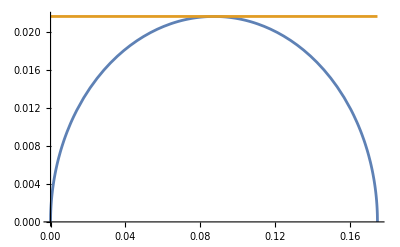

```mathematica
Plot[{insolutiondp[r],newrjoindp},{r,0,newruncodp},PlotRange->All]
```

```mathematica
(*factors for the real part of the solution inside of the horizon*)
slopetotdp=(msmcauchy/.χ->Function[{r},(ψtot[r]+δψsol[r])^-4]/.r->10^-12)/newrjoindp
difftotdp=newrjoindp;
```

InterpolatingFunction::dmval: Input value {1/1000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

3.990804193107742

{{riso→1/2 (-2 A-mBH-mNS+r-√(-((4 A+2 mBH+2 mNS-r) r)))},{riso→1/2 (-2 A-mBH-mNS+r+√(-((4 A+2 mBH+2 mNS-r) r)))}}

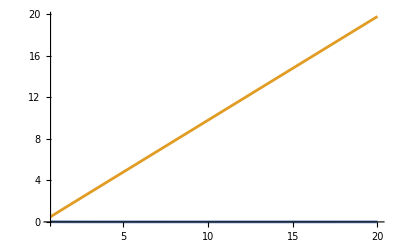

The solution where both radii become asymptotically the same is the suitable one.

1/2 (-2 A-mBH-mNS+r+√(-((4 A+2 mBH+2 mNS-r) r)))

```mathematica
(*solution outside of the NS surface*)
Solve[(1+(mNS+mBH)/(2 riso)+A/riso)^2 riso==r,riso]//Simplify
{%[[1,1,2]],%[[2,1,2]]}/.mNS->msunco/.mBH->massBH/.A->Avalsol;
Plot[%,{r,0.7,20}]
Style["The solution where both radii become asymptotically the same is the suitable one.",Blue]
risototofroutdp[r_]=%%%%[[2,1,2]]//Evaluate
```

```mathematica
(*solution between horizon and NS surface*)
npoints=2000;
Table[{(ψtot[r]+δψsol[r])^2 r,r}/.r->newrjoindp+ci(rsiso(*no dp??*)-newrjoindp)/npoints,{ci,0,npoints}];
risototofrintermdp=Interpolation[%]
```

InterpolatingFunction[…]

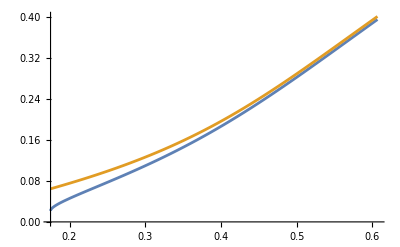

```mathematica
Plot[{risototofrintermdp[r],rtofr[r]},{r,newruncodp,rsuncofromisodp}](*comparing to NS*)
```

```mathematica
risototofrdp[r_]=Piecewise[{{ⅈ insolutiondp[r]+r/slopetotdp-difftotdp,r<newruncodp},{risototofrintermdp[r],newruncodp<r<rsuncofromisodp},{risototofroutdp[r]/.mNS->msunco/.mBH->massBH/.A->Avalsol ,r>=rsuncofromisodp}}];
```

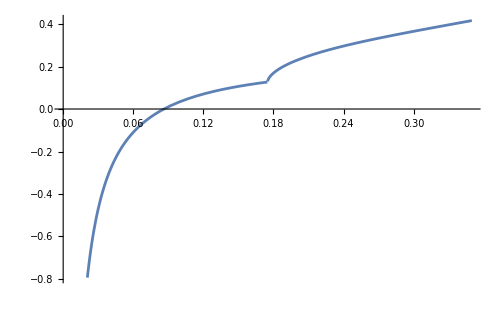
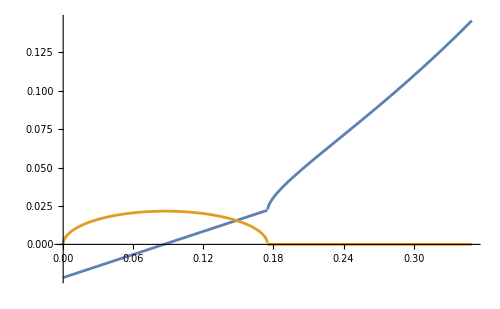

```mathematica
{Plot[Re@risototofrdp[r]/r,{r,0,2newruncodp},ImageSize->500],Plot[{Re@risototofrdp[r],Im@risototofrdp[r]},{r,0,2newruncodp},ImageSize->500]}
```

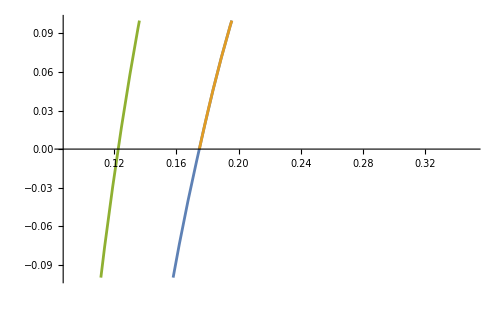
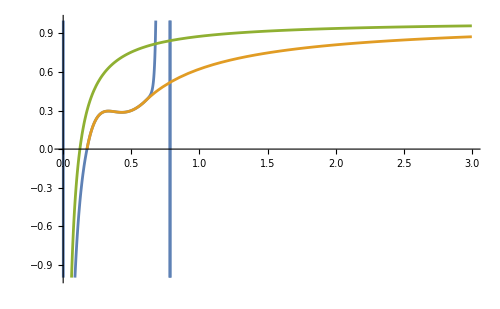
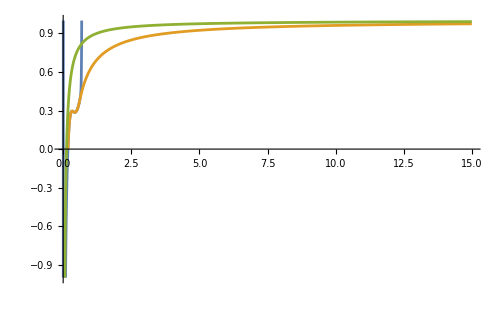

```mathematica
{1/(((χNSpoly)^(-1/4)+ψBH[r]+δψsolpoly)/(2D[((χNSpoly)^(-1/4)+ψBH[r]+δψsolpoly),r]r+((χNSpoly)^(-1/4)+ψBH[r]+δψsolpoly)))^2/.r->risototofrdp[rschw]/.rschw->r,1/((ψtot[r]+δψsol[r])/(2D[ψtot[r]+δψsol[r],r]r+ψtot[r]+δψsol[r]))^2/.r->risototofrdp[rschw]/.rschw->r,1-(2massBH)/r};
{Plot[Re@%//Evaluate,{r,newruncodp/2,2newruncodp},PlotRange->{-0.1,0.1},ImageSize->500],Plot[Re@%//Evaluate,{r,0,3},PlotRange->{-1,1},ImageSize->500],Plot[Re@%//Evaluate,{r,0,15},PlotRange->{-1,1},ImageSize->500]}//Quiet(*check that 1/grr was determined properly*)
```

```mathematica
oneovergrrarealradiusdp[r_]=Piecewise[{{1/(((χNSpoly)^(-1/4)+ψBH[r]+δψsolpoly)/(2D[((χNSpoly)^(-1/4)+ψBH[r]+δψsolpoly),r]r+((χNSpoly)^(-1/4)+ψBH[r]+δψsolpoly)))^2/.r->risototofrdp[rschw]/.rschw->r//Re//Evaluate,r<rsuncofromisodp},{1/((ψtot[r]+δψsol[r])/(2D[ψtot[r]+δψsol[r],r]r+ψtot[r]+δψsol[r]))^2/.r->risototofrdp[rschw]/.rschw->r,r>=rsuncofromisodp}}];
```

InterpolatingFunction::dmval: Input value {1/1000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

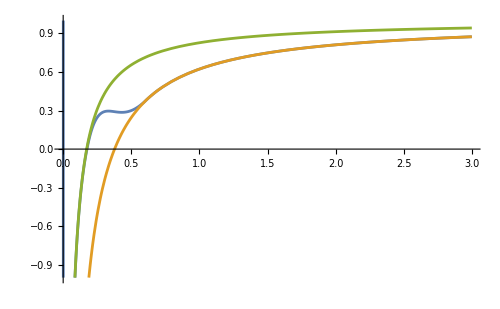
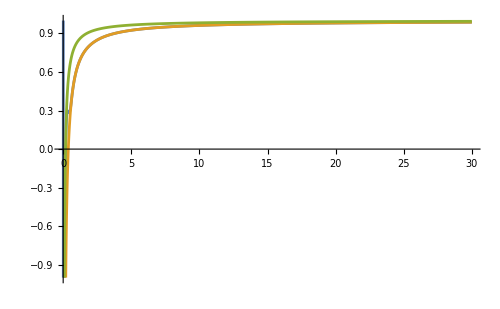

```mathematica
(*comparison with BH with total mass of the system and with BH with the horizon mass*)
{oneovergrrarealradiusdp[r],1-2massBH/r-2msunco/r-4Avalsol/r,1-2(msmcauchy/.χ->Function[{r},(ψtot[r]+δψsol[r])^-4]/.r->10^-12)/r};
{Plot[Re@%//Evaluate,{r,0,3},PlotRange->{-1,1},ImageSize->500],Plot[Re@%//Evaluate,{r,0,30},PlotRange->{-1,1},ImageSize->500]}//Quiet
```

```mathematica
rsuncofromisodp(*location of NS surface in the superposition*)
rsunco(*location of NS surface for single NS*)
FindRoot[2(msmcauchy/.χ->Function[{r},(ψtot[r]+δψsol[r])^-4]/.r->10^-12)==r,{r,0.1}]
rBHdp=%[[1,2]](*location of horizon in the superposition*)
newruncodp(*location of horizon in the superposition*)
```

0.6066675894880070347992882367900098428777367653056

0.60105862487811508465060001432581958516898513822673

InterpolatingFunction::dmval: Input value {1/1000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{r→0.172455}

0.172455

0.1748830936617506714256753190666675263394

```mathematica
(*K=1 and massBH=massNS/3*)
```

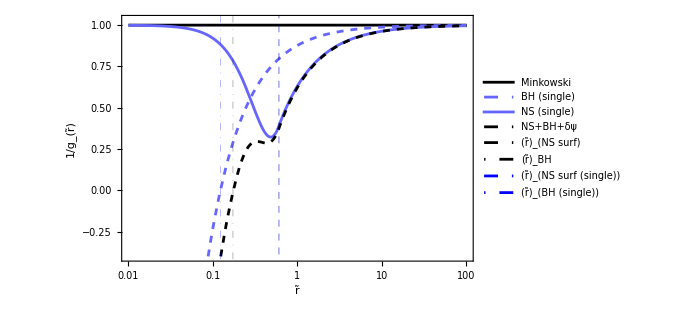

```mathematica
LogLinearPlot[Re@{1,1-(2massBH)/r,1/grrNS[r],oneovergrrarealradiusdp[r],,,,}//Evaluate,{r,0.01,100},PlotRange->{-0.4,1.03},ImageSize->500,PlotStyle->{{Black},{myblue,Dashed},{myblue},{Black,Dashed},Directive[Black,Dashed,Thin],Directive[Black,DotDashed,Thin],Directive[Blue,Dashed,Thin],Directive[Blue,DotDashed,Thin]},ImageSize->500,Frame->True,FrameLabel->{"r̃","1/g_(r̃)"},BaseStyle->{FontSize->15,FontFamily->"Times",FontColor->Black},FrameStyle->Black,AxesStyle->Black,PlotLegends->Placed[Map[Style[#,15,FontFamily->"Times"]&,{"Minkowski","BH (single)","NS (single)", "NS+BH+δψ","(r̃)_(NS surf)","(r̃)_BH","(r̃)_(NS surf (single))","(r̃)_(BH (single))"}],{0.82,0.48}],GridLines->{{{rsuncofromisodp,Directive[Black,Dashed,Thin]},{rBHdp,Directive[Black,DotDashed,Thin]},{rsunco,Directive[Blue,Dashed,Thin]},{2massBH,Directive[Blue,DotDashed,Thin]}},{}}]
```

#### Hyperboloidalization

If gtt = -1/grr, as should have been derived here, then the calculation of h should be a bit simpler.

```mathematica
part[rp_]=partout[rp]//Evaluate
Aadp=oneovergrrarealradiusdp[r]/.r->rp;
```

-Ccmc/rp^2-(Kcmc rp)/3

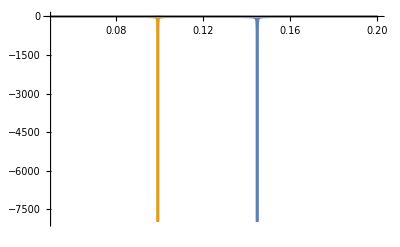

```mathematica
(*calculation of the critical Ccmc value*)
Ccmcvalsuperpdp=0.0123453371`50;(*for massBH=msunco/3 (with K=1 and Γ=2) and Kcmc=-3*)
Plot[{part[rp](*/Aadp*)/Sqrt[Aadp+part[rp]^2]/.Kcmc->Kcmcset/.Ccmc->Ccmcvalsuperpdp,(-Ccmc/r^2-(Kcmc r)/3)/((*(1-(2 mass)/r)*) √(1-(2 mass)/r+(Ccmc/r^2+(Kcmc r)/3)^2))/.Kcmc->Kcmcset/.Ccmc->Ccmcset/.mass->massBH/.r->rp}//Flatten//Evaluate,{rp,0.05,0.2(*0.01,0.03*)},PlotRange->{-8000,1},PlotPoints->500]//Quiet
```

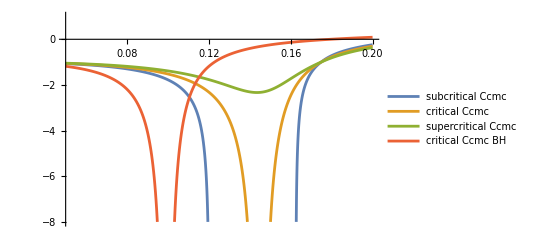

```mathematica
Plot[{Map[part[rp](*/Aadp*)/Sqrt[Aadp+part[rp]^2]/.Kcmc->Kcmcset/.Ccmc->#&,{Ccmcvalsuperpdp-0.001,Ccmcvalsuperpdp,Ccmcvalsuperpdp+0.001}],(-Ccmc/r^2-(Kcmc r)/3)/((*(1-(2 mass)/r)*) √(1-(2 mass)/r+(Ccmc/r^2+(Kcmc r)/3)^2))/.Kcmc->Kcmcset/.Ccmc->Ccmcset/.mass->massBH/.r->rp}//Flatten//Evaluate,{rp,0.05,0.2(*0.01,0.03*)},PlotRange->{-8,1},PlotPoints->500,PlotLegends->{"subcritical Ccmc","critical Ccmc","supercritical Ccmc","critical Ccmc BH" }]//Quiet
```

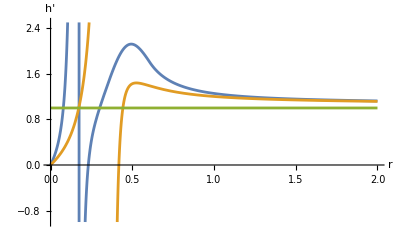

```mathematica
(*comparison to BH with same mass as NS*)
Plot[{part[rp]/Aadp/Sqrt[Aadp+part[rp]^2]/.Kcmc->Kcmcset/.Ccmc->Ccmcvalsuperpdp,(-Ccmc/r^2-(Kcmc r)/3)/((1-(2 mass)/r) √(1-(2 mass)/r+(Ccmc/r^2+(Kcmc r)/3)^2))/.Kcmc->Kcmcset/.Ccmc->CcmcsetNS/.mass->msunco/.r->rp,1}//Evaluate,{rp,0,2},PlotRange->{-1,2.5},AxesLabel->{r,h'}]//Quiet
```

#### Compactification

(9 r^4 (aconf[r]-r aconf'[r])^2)/(Kcmc^2 r^6+9 r^4 aconf[r]^2+6 (Ccmc Kcmc-3 mass) r^3 aconf[r]^3+9 Ccmc^2 aconf[r]^6)

(r^4 (-1. aconf[r]+r aconf'[r])^2)/(r^6+r^4 aconf[r]^2-0.401945787137159850088956572603891508063113589828 r^3 aconf[r]^3+0.00015240734811263641 aconf[r]^6)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NDSolve::mxst: Maximum number of 10000 steps reached at the point r == 0.06935977921696677286495987349655012581029.

{{aconf→InterpolatingFunction[{{0.06935977921696677286495987349655012581029, 1.000000000000000000000000000000000000000}}, <>]}}

InterpolatingFunction[{{0.06935977921696677286495987349655012581029, 1.000000000000000000000000000000000000000}}, <>]

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

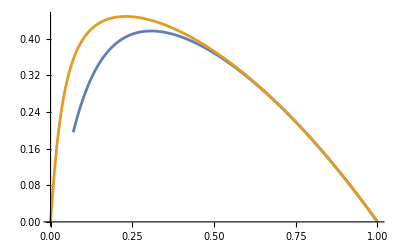

```mathematica
(*compactification for outer part of the spacetime*)
(9 r^4 (aconf[r]-r aconf'[r])^2)/(9 Subscript[C, CMC]^2 aconf[r]^6+9 Q^2 aconf[r]^4 r^2+6 (Subscript[C, CMC] Subscript[K, CMC]-3 m) aconf[r]^3 r^3+9 aconf[r]^2 r^4+Subscript[K, CMC]^2 r^6)/.Q->Qset/.r[]->r//Simplify
%/.Kcmc->Kcmcset/.Ccmc->Ccmcvalsuperpdp/.mass->(msmcauchy/.χ->Function[{r},(ψtot[r]+δψsol[r])^-4]/.r->(*10^-16*)1)/.Q->Qset//Simplify
Solve[%==1,aconf'[r],Assumptions->None][[1,1]];
NDSolve[{First@%==Last@%,aconf[1]==0},aconf,{r,0,1},AccuracyGoal->15,PrecisionGoal->20,WorkingPrecision->40]
lilumsmdp=%[[1,1,2]]
Plot[{lilumsmdp[r],lilu[r]},{r,0,1}]
```

```mathematica
FindRoot[rsunco==r/lilumsmdp[r],{r,0.2},AccuracyGoal->15,PrecisionGoal->20,WorkingPrecision->40]
rscompdp=%[[1,2]]
FindRoot[rsuncofromisodp==r/lilumsmdp[r],{r,0.2},AccuracyGoal->15,PrecisionGoal->20,WorkingPrecision->40]
rscompmsmdp=%[[1,2]]
```

{r→0.2458419087898775232738463234110044029143}

0.2458419087898775232738463234110044029143

{r→0.2485861464259339532975175904222883428735}

0.2485861464259339532975175904222883428735

```mathematica
(*Aadp in interior*)1/(((χNSpoly)^(-1/4)+ψBH[r]+δψsolpoly)/(2D[((χNSpoly)^(-1/4)+ψBH[r]+δψsolpoly),r]r+((χNSpoly)^(-1/4)+ψBH[r]+δψsolpoly)))^2/.r->risototofrdp[rschw]/.rschw->r//Re (*for r<rsuncofromiso*);
Aadpinterior=%/.r->rp;
%/.rp->2
```

1788.13167394616051150795

```mathematica
grrinteriordp=1/(Aadpinterior+part[rp]^2)/.Kcmc->Kcmcset/.Ccmc->Ccmcvalsuperpdp;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value {0.17488260188325} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Max::nord: Invalid comparison with -0.46184214718303-4.90187×10^-9 ⅈ attempted.

Max::nord: Invalid comparison with 0.03005765135678+4.90187×10^-9 ⅈ attempted.

Max::nord: Invalid comparison with -0.46184214718303-4.90187×10^-9 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

NDSolve::nrnum1: The function value Max[-0.46184214718303-4.90187×10^-9 ⅈ,0.03005765135678+4.90187×10^-9 ⅈ] is not a real number when the arguments are {0.0000151735916136429,0.000104771588279983+3.546177×10^-12 ⅈ,1,-1,1}.

NDSolve::nlnum: The function value $Failed is not a list of numbers with dimensions {1} at {r,aconf[r],NDSolve`s$370933[r],NDSolve`s$370932[r],NDSolve`s$370934[r]} = {0.0000151735916136429,{0.000104771588279983+3.54617749211967×10^-12 ⅈ},{1,-1,1}}.

{{aconf→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {5.0222×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

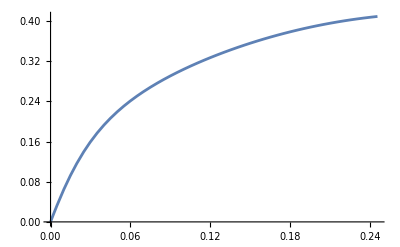

0.40901485914079

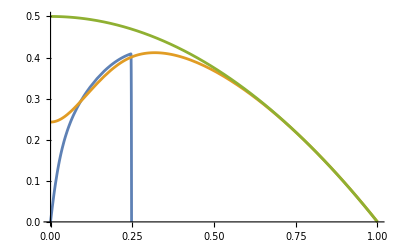

```mathematica
(grrinteriordp/.rp->r/aconf[r])(aconf[r]-r aconf'[r])^2/aconf[r]^2;(*choosing compactification imposing an initial conformally flat metric, as usual*)
Solve[%==1,aconf'[r],Assumptions->None][[1,1]];
NDSolve[{First@%==Last@%,aconf[rscompdp]==lilumsmdp[rscompdp]},aconf,{r,10^-12,rscompdp},AccuracyGoal->12,PrecisionGoal->18,WorkingPrecision->15]
Plot[%[[1,1,2]][r],{r,0,rscompdp},AxesOrigin->{0,0}]
%%[[1,1,2]][rscompdp]
aconftotdp=%%%[[1,1,2]];
Plot[{aconftotdp[r],aconfNS[r],-Kcmcset(1-r^2)/6},{r,0,1},PlotRange->{0,0.5}]
```

```mathematica
aconftotalldp[r_]=Piecewise[{{aconftotdp[r],r<rscompdp},{lilumsmdp[r],r>=rscompdp}}];
aconfomeg[r_]=-Kcmcset(1-r^2)/6 ;
```

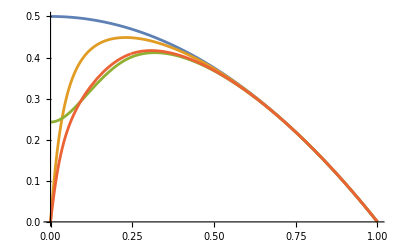

```mathematica
Plot[{aconfomeg[r],lilu[r],aconfNS[r],aconftotalldp[r]},{r,0,1}]
```

```mathematica
hpfunctotdp=part[rp]/Aadp/Sqrt[Aadp+part[rp]^2]/.Kcmc->Kcmcset/.Ccmc->Ccmcvalsuperpdp;
```

```mathematica
compigrralldp=Compile[{r},((1-Aadp^2 hpfunctotdp^2)/Aadp/.rp->r/aconf[r])(aconf[r]-r aconf'[r])^2/aconf[r]^2/.aconf->aconftotalldp//Re]
```

CompiledFunction[…]

{{0.01,0.999999},{0.03,1.},{0.05,0.999999},{0.07,0.999994},{0.09,1.},{0.11,0.999999},{0.13,1.},{0.15,0.999999},{0.17,1.},{0.19,1.},{0.21,1.},{0.23,1.},{0.25,1.},{0.27,1.},{0.29,1.},{0.31,1.},{0.33,1.},{0.35,1.},{0.37,1.},{0.39,1.},{0.41,1.},{0.43,1.},{0.45,1.},{0.47,1.},{0.49,1.},{0.51,1.},{0.53,1.},{0.55,1.},{0.57,1.},{0.59,1.},{0.61,1.},{0.63,1.},{0.65,1.},{0.67,1.},{0.69,1.},{0.71,1.},{0.73,1.},{0.75,1.},{0.77,1.},{0.79,1.},{0.81,1.},{0.83,1.},{0.85,1.},{0.87,1.},{0.89,1.},{0.91,1.},{0.93,1.},{0.95,1.},{0.97,1.},{0.99,1.}}

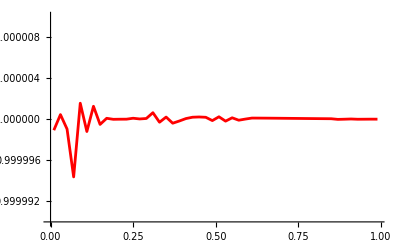

```mathematica
(*to check equation is satisfied -- takes a while to evaluate*)
Map[{#,compigrralldp[#]}&,Range[0.01,0.99,0.02]]
ListLinePlot[%,PlotStyle->Red,PlotRange->{0.99999,1.00001}]
```

```mathematica
FindRoot[rsuncofromisodp==r/aconftotalldp[r],{r,0.3}]
rsNScompdp=%[[1,2]](*location of the NS surface in terms of the compactified radius*)
rscompdp
FindRoot[2massBH==r/aconftotalldp[r],{r,0.01}]
FindRoot[2(msmcauchy/.χ->Function[{r},(ψtot[r]+δψsol[r])^-4]/.r->10^-12)==r/aconftotalldp[r],{r,0.01}]
rBHcompdp=%[[1,2]](*location of the BH horizon in terms of the compactified radius*)
```

{r→0.248586}

0.248586

0.2458419087898775232738463234110044029143

InterpolatingFunction::dmval: Input value {-0.0134436} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0175988} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0224065} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {r} = {1.}.

{r→-0.000270718}

InterpolatingFunction::dmval: Input value {1/1000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{r→0.0213973}

0.0213973

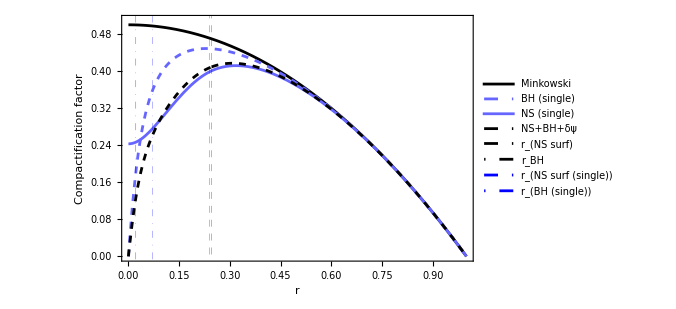

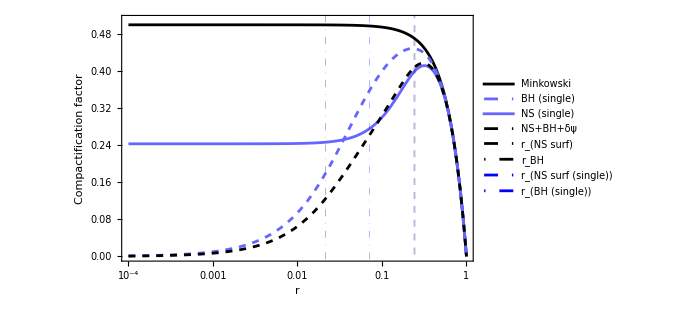

```mathematica
Plot[{-Kcmcset(1-r^2)/6,lilu[r],aconfNS[r],aconftotalldp[r],,,,},{r,0,1},PlotRange->{0,0.51},ImageSize->500,PlotStyle->{{Black},{myblue,Dashed},{myblue},{Black,Dashed},Directive[Black,Dashed,Thin],Directive[Black,DotDashed,Thin],Directive[Blue,Dashed,Thin],Directive[Blue,DotDashed,Thin]},ImageSize->500,Frame->True,FrameLabel->{"r","Compactification factor"},BaseStyle->{FontSize->15,FontFamily->"Times",FontColor->Black},FrameStyle->Black,AxesStyle->Black,PlotLegends->Placed[Map[Style[#,15,FontFamily->"Times"]&,{"Minkowski","BH (single)","NS (single)", "NS+BH+δψ","r_(NS surf)","r_BH","r_(NS surf (single))","r_(BH (single))"}],{0.453,0.28}],GridLines->{{{rscompdp,Directive[Black,Dashed,Thin]},{rBHcompdp,Directive[Black,DotDashed,Thin]},{rsNScomp,Directive[Blue,Dashed,Thin]},{rBHcomp,Directive[Blue,DotDashed,Thin]}},{}}]
LogLinearPlot[{-Kcmcset(1-r^2)/6,lilu[r],aconfNS[r],aconftotalldp[r],,,,},{r,0.0001,1},PlotRange->{0,0.51},ImageSize->500,PlotStyle->{{Black},{myblue,Dashed},{myblue},{Black,Dashed},Directive[Black,Dashed,Thin],Directive[Black,DotDashed,Thin],Directive[Blue,Dashed,Thin],Directive[Blue,DotDashed,Thin]},ImageSize->500,Frame->True,FrameLabel->{"r","Compactification factor"},BaseStyle->{FontSize->15,FontFamily->"Times",FontColor->Black},FrameStyle->Black,AxesStyle->Black,PlotLegends->Placed[Map[Style[#,15,FontFamily->"Times"]&,{"Minkowski","BH (single)","NS (single)", "NS+BH+δψ","r_(NS surf)","r_BH","r_(NS surf (single))","r_(BH (single))"}],{0.18,0.46}],GridLines->{{{rscompdp,Directive[Black,Dashed,Thin]},{rBHcompdp,Directive[Black,DotDashed,Thin]},{rsNScomp,Directive[Blue,Dashed,Thin]},{rBHcomp,Directive[Blue,DotDashed,Thin]}},{}}]
```

#### Misner-Sharp mass plots of superposition

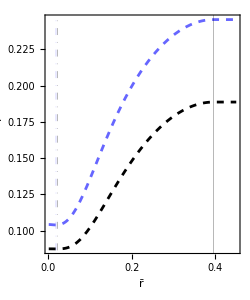

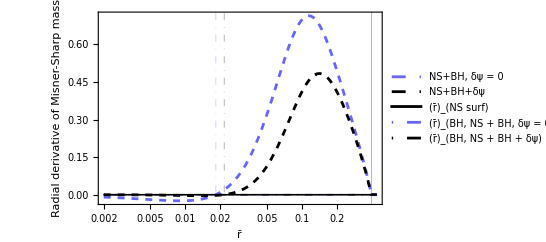

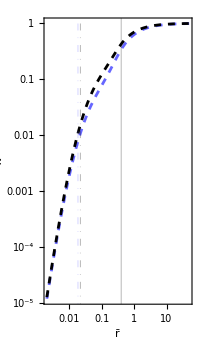

```mathematica
{msmcauchy/.χ->Function[{r},(ψNS[r]+massBH/(2 r))^-4],msmcauchy/.χ->Function[{r},(ψNS[r]+massBH/(2 r)+δψsol[r])^-4],,,,};
Plot[%,{r,0.001,0.45},PlotRange->All,ImageSize->250,Frame->True,FrameLabel->{"r̄","Misner-Sharp mass"},BaseStyle->{FontSize->12,FontFamily->"Times",FontColor->Black},FrameStyle->Black,AxesStyle->Black,PlotStyle->{{myblue,Dashed},{Black,Dashed},{Black,Thin},{myblue, DotDashed,Thin},{Black, DotDashed,Thin},{Black, Dotted,Thin}},AspectRatio->1.2,GridLines->{{{rsiso,Directive[Black]},{isoradiibh[[1]],Directive[myblue,DotDashed]},{newrjoindp,Directive[Black,DotDashed]}},{}}]
LogLinearPlot[D[%%,r]//Evaluate,{r,0.002,0.44},PlotRange->All,ImageSize->404,Frame->True,FrameLabel->{"r̄","Radial derivative of Misner-Sharp mass"},BaseStyle->{FontSize->12,FontFamily->"Times",FontColor->Black},FrameStyle->Black,AxesStyle->Black,PlotStyle->{{myblue,Dashed},{Black,Dashed},{Black,Thin},{myblue, DotDashed,Thin},{Black, DotDashed,Thin},{Black,Thin}},AspectRatio->0.6,PlotLegends->Placed[Map[Style[#,FontSize->12,FontFamily->"Times",FontColor->Black]&,{ "NS+BH, δψ = 0","NS+BH+δψ","(r̄)_(NS surf)","(r̄)_(BH,  NS + BH,  δψ = 0)","(r̄)_(BH,  NS + BH + δψ)"}],{0.22,0.50}],GridLines->{{{rsiso,Directive[Black]},{isoradiibh[[1]],Directive[myblue,DotDashed]},{newrjoindp,Directive[Black,DotDashed]}},{}}]
LogLogPlot[{χ[r]/.χ->Function[{r},(ψNS[r]+massBH/(2 r))^-4],χ[r]/.χ->Function[{r},(ψNS[r]+massBH/(2 r)+δψsol[r])^-4],,,,},{r,0.002,50},PlotRange->All,ImageSize->200,Frame->True,FrameLabel->{"r̄","χ"},BaseStyle->{FontSize->12,FontFamily->"Times",FontColor->Black},FrameStyle->Black,AxesStyle->Black,PlotStyle->{{myblue,Dashed},{Black,Dashed},{Black,Thin},{myblue, DotDashed,Thin},{Black, DotDashed,Thin},{Black, Dotted,Thin}},AspectRatio->1.8,GridLines->{{{rsiso,Directive[Black]},{isoradiibh[[1]],Directive[myblue,DotDashed]},{newrjoindp,Directive[Black,DotDashed]}},{}}]
```

### 7. Penrose diagrams

#### Setup

```mathematica
(*installation option 1:*)(*ResourceFunction["MaTeXInstall"]*)(*or*)
```

```mathematica
(*installation option 2:*)(*Needs["PacletManager`"]*)
```

```mathematica
(*installation option 2:*)(*PacletInstall["~/Downloads/MaTeX-1.7.10.paclet"]*)
```

```mathematica
<<MaTeX`
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{mathrsfs}\\DeclareSymbolFontAlphabet{\\mathrsfs}{rsfs}
\\newcommand{\\scri}{\\mathrsfs{I}}"}]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{mathrsfs}\DeclareSymbolFontAlphabet{\mathrsfs}{rsfs}
\newcommand{\scri}{\mathrsfs{I}}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

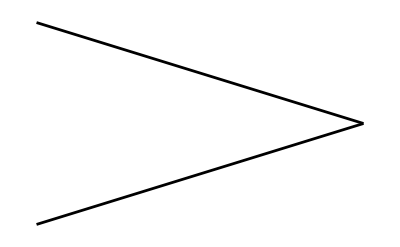
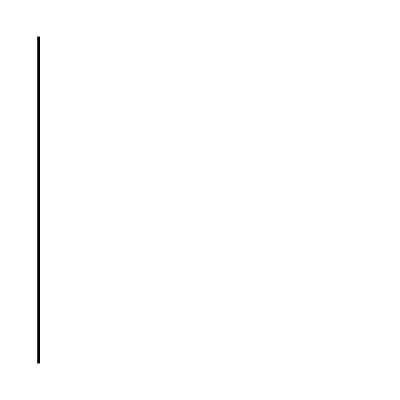

-Graphics-

```mathematica
labe = 22;matexmagnification=2;
covermin = {Plot[{x - π/2, π/2 - x}, {x, 0, π/2}, 
   PlotRange -> {{0, π/2}, {-π/2, π/2}}, Ticks -> None, 
   PlotStyle -> Black, Axes -> None(*,AspectRatio->1*)], 
  ContourPlot[x == 0, {x, -0.01, π/2}, {y, -π/2, π/2}, Axes -> None, 
   Frame -> None, ContourStyle -> Black]}
lettersmin = Graphics[{Text[MaTeX["i^+",Magnification->matexmagnification], {0 + 0.1, π/2 +  0.16}, BaseStyle -> {FontSize -> labe,FontFamily->Times}],    Text[MaTeX["i^-",Magnification->matexmagnification], {0 +  0.1, -π/2 - 0.2}, BaseStyle -> {FontSize -> labe,FontFamily->Times}],    Text[MaTeX["i^0",Magnification->matexmagnification], {π/2 + 0.2, 0},  BaseStyle -> {FontSize -> labe,FontFamily->Times}],  Text[MaTeX["\\scri^+",Magnification->matexmagnification], {π/4 + 0.15, π/4 + 0.15}], 
   Text[MaTeX["\\scri^-",Magnification->matexmagnification], {π/4 + 0.15, -π/4 - 0.15}]},  PlotRange -> {{0 - 0.3, π /2+ 0.3}, {-π/2 - 0.3, π/2 + 0.3}}]
```

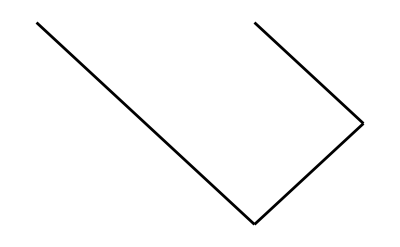
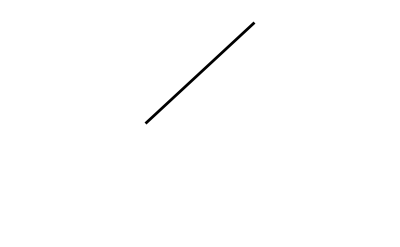
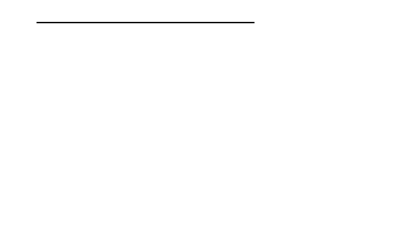

```mathematica
coverschw = {Plot[{x - π/2, π/2 - x,-x}, {x, -π/2, π/2},   PlotRange -> {{-π/4, π/2}, {-π/4, π/4}}, Ticks -> None,   PlotStyle -> Black, Axes -> None(*,AspectRatio->1*)],
 Plot[{x}, {x, 0, π/2},  PlotRange -> {{-π/4, π/2}, {-π/4, π/4}}, Ticks -> None,    PlotStyle -> Black, Axes -> None(*,AspectRatio->1*)],
 Plot[{π/4}, {x,-π/4, π/4},  PlotRange -> {{-π/4, π/2}, {-π/4, π/4}}, Ticks -> None,    PlotStyle ->{ Thick,Black}, Axes -> None(*,AspectRatio->1*)] }
```

```mathematica
lettersschw = Graphics[{Text[MaTeX["i^+",Magnification->matexmagnification], {π/4 + 0.1, π/8 +  0.42}, BaseStyle -> {FontSize -> labe,FontFamily->Times}],    Text[MaTeX["i^-",Magnification->matexmagnification], {π/4 +  0.1, -π /8- 0.45}, BaseStyle -> {FontSize -> labe,FontFamily->Times}],    Text[MaTeX["i^0",Magnification->matexmagnification], {π /2+ 0.1, 0},  BaseStyle -> {FontSize -> labe,FontFamily->Times}],  Text[MaTeX["\\scri^+",Magnification->matexmagnification], {3π/8 + 0.1, π/8 + 0.1}, BaseStyle -> {FontSize -> labe - 2,FontFamily->Times}], 
   Text[MaTeX["\\scri^-",Magnification->matexmagnification], {3π/8 + 0.1, -π/8 - 0.1}, BaseStyle -> {FontSize -> labe - 2,FontFamily->Times}],Text[MaTeX["\\tilde r=0",Magnification->1.8],{0,π/4+0.06}, BaseStyle -> {FontSize -> labe-2,FontFamily->Times}]},  PlotRange -> {{-π/4 - 0.01, π/2 + 0.25}, {-π/4 -0.13, π/4 + 0.14}}]
```

-Graphics-

```mathematica
makePlotLegend[names_, markers_, origin_, markerSize_, fontSize_, font_] := 
  Join @@ Table[{Text[Style[names[[i]], FontSize -> fontSize, FontFamily->font], 
      Offset[{1.5*markerSize, -(i - 0.5)*Max[markerSize, fontSize]*1.25}, 
       Scaled[origin]], {-1, 0}], 
     Inset[Show[markers[[i]], ImageSize -> markerSize], 
      Offset[{markerSize/2, -(i - 0.5)*Max[markerSize, fontSize]*1.25}, 
       Scaled[origin]], {0, 0}, 
      Background -> Directive[Opacity[0], White]]}, {i, 1, 
     Length[names]}];(*copied from \
http://stackoverflow.com/questions/3463437/plotting-legends-in-mathematica*)
```

#### Cauchy slices for single NS

```mathematica
npoints=20;
Timing[tortoiserpoints=Table[N[{rp,NIntegrate[1/Sqrt[Exp[Exp[νunco[r]]](1-2munco[r]/r)],{r,0,rp},AccuracyGoal->accdef,PrecisionGoal->precdef,WorkingPrecision->wpdef]}/.rp->0+ci(rsunco-0)/npoints,{Infinity,5accdef}],{ci,0,npoints}]]
tortoiser=Interpolation[tortoiserpoints]
```

NIntegrate::nlim: r = rp is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0004222361377079984609868132144301964616715920924701302409615611738657904587849066887369713361038729431}. NIntegrate obtained 0.2561428119924837362970674777293082832941515259693663705544402913428617101050366477181066046135422294 and 1.312822730982265665426563910218232002073926058078852102507588798791444468935926798847087016403854799×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0005805746893484978838568681698415201347984391271464290813221466140654618808293073650131673472380573429}. NIntegrate obtained 0.3747855132588336147875833692350027357382617692693735900305985950119235445467752741935488565924363815 and 1.995195931121888899753580776994215746535974889201157452016833474995202914120990854385740976918383398×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0006333542065619976914802198216452946925073881387051953614423417607986856881773600331054570041558094146}. NIntegrate obtained 0.4182208170128227123749412810568041997486909245298493482873249409953355540542449379802194001854584318 and 1.202684788693277498009350040747026971769002721833384027429375995948717490082573700281069113297415797×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{11.673,{{0.,0.},{0.030052931243905754232530000716290979258449256911336,0.029726891435922423503655598984268622803446043292474},{0.060105862487811508465060001432581958516898513822673,0.059668030887156848726280940069519774202305336088888},{0.090158793731717262697590002148872937775347770734009,0.090039486622015850111852295113694237187265955085971},{0.12021172497562301693012000286516391703379702764535,0.12106066381501204288907014959014478426439273420821},{0.15026465621952877116265000358145489629224628455668,0.15295509304828218514340929132909421261401055630052},{0.18031758746343452539518000429774587555069554146802,0.18594980937049274650132977164896204330032368875591},{0.21037051870734027962771000501403685480914479837936,0.22027222463226934390501250903910229298873149502581},{0.24042344995124603386024000573032783406759405529069,0.25614281199248373629706747772930828329415152596937},{0.27047638119515178809277000644661881332604331220203,0.2937612462645664315648299367380020142364612440162},{0.30052931243905754232530000716290979258449256911336,0.33328319163249001722826467430288934640293045253856},{0.3305822436829632965578300078792007718429418260247,0.37478551325883361478758336923500273573826176926937},{0.36063517492686905079036000859549175110139108293604,0.41822081701282271237494128105680419974869092452985},{0.39068810617077480502289000931178273035984033984737,0.46336954268742612784135556319502911397150888270405},{0.42074103741468055925542001002807370961828959675871,0.50980865181152408787952568299614576562148693909779},{0.45079396865858631348795001074436468887673885367005,0.55692312159266497089182535725705064613779090135256},{0.48084689990249206772048001146065566813518811058138,0.60397705370653070622056524855840628978599816201365},{0.51089983114639782195301001217694664739363736749272,0.65023073396029387283097942780104271021944373530232},{0.54095276239030357618554001289323762665208662440406,0.69505882689522353051274959852612430041023657512465},{0.57100569363420933041807001360952860591053588131539,0.73802356505707386091028908212321808455953798331648},{0.60105862487811508465060001432581958516898513822673,0.77888706909974689577201988876353707349864760886858}}}

InterpolatingFunction[…]

```mathematica
FindRoot[0==tortoiser[r]-(r+2msunco Log[r-2msunco]+C)/.r->rsunco,{C,1/10},AccuracyGoal->accdef,PrecisionGoal->precdef,WorkingPrecision->wpdef-1](*satisfying that rtort=r=0 at the origin and matching to outer Schwarzschild expression by setting the value of the integration constant*)
tortoutconst=%[[1]];
```

{C→0.7143419365522515650665070856642116691656636189829}

```mathematica
rtortNS[r_]=Piecewise[{{tortoiser[r],r<rsunco},{(r+2msunco Log[r-2msunco]+C)/.tortoutconst ,r>=rsunco}}]//Evaluate
```

Piecewise[{{InterpolatingFunction[…][r], r<0.60105862487811508465060001432581958516898513822673}, {0.7143419365522515650665070856642116691656636189829+r+0.3681759344528698875667174294529186310473351923708 Log[-0.3681759344528698875667174294529186310473351923708+r], r≥0.60105862487811508465060001432581958516898513822673}, {0, True}}]

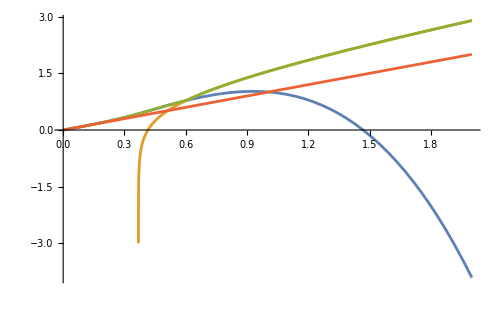
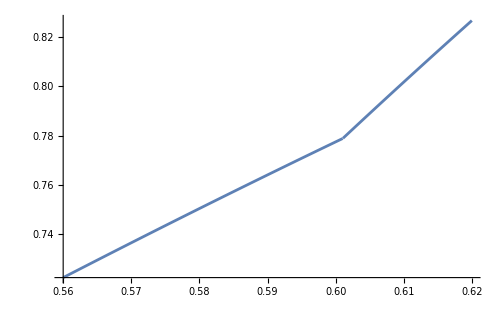
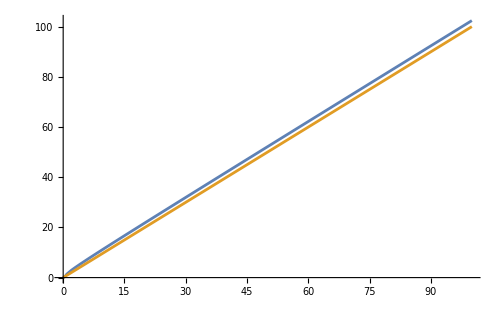

The matching point is a bit kinky.

```mathematica
{Plot[{tortoiser[r],r+2msunco Log[r-2msunco]+C/.tortoutconst,rtortNS[r],r},{r,0,2},ImageSize->500],Plot[{rtortNS[r]},{r,0.56,0.62},ImageSize->500],Plot[{rtortNS[r],r},{r,0,100},ImageSize->500]}
Style["The matching point is a bit kinky.",Orange,20]
```

```mathematica
(*construction for Minkowski*)
uf= t -r; vf = t +r;
Uf = ArcTan[uf]; Vf = ArcTan[vf];
Tf = (Uf + Vf)/2; Rf =( Vf - Uf)/2;
listtfMink[tval_] = {Rf, Tf} /. {t -> tval}//Evaluate;
```

```mathematica
(*construction for NS*)
uf = t -rtortNS[r]; vf = t + rtortNS[r];
Uf = ArcTan[uf]; Vf = ArcTan[vf];
Tf = (Uf + Vf)/2; Rf =( Vf - Uf)/2;
listrfNS[rval_] = {Rf, Tf} /. {r -> rval}//Evaluate;
listtfNS[tval_] = {Rf, Tf} /. {t -> tval}//Evaluate;
```

```mathematica
colournscauchy=myblue;
```

```mathematica
hlistNScauchy=Map[listtfNS[#]&,{10,3.5,1.5,0.5,-0.15,-1,-5}];
```

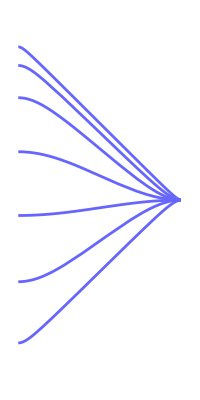

```mathematica
phlNScauchy=ParametricPlot[hlistNScauchy,{r,0,100},PlotRange->{{0,π/2},{-π/2,π/2}},Ticks->None,PlotStyle->colournscauchy,BaseStyle->{FontSize->labe-2},Axes->None, PlotPoints->200]
```

```mathematica
nsradius=ParametricPlot[listrfNS[rsunco], {t, -100, 100},   PlotRange -> {{0, π/2}, {-π/2, π/2}}, Ticks -> None, Axes -> None,   PlotStyle -> {{Black,Thick,Dashed}},PlotPoints->200];
```

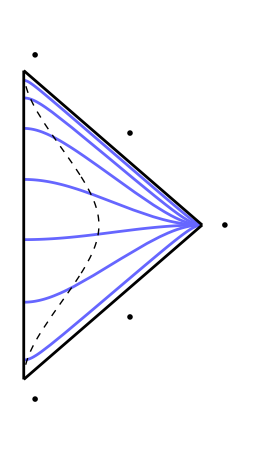

```mathematica
Show[phlNScauchy,nsradius,covermin,lettersmin,PlotRange->{{0,π/2+0.3},{-π/2-0.3,π/2+0.3}},ImageSize->{260,450}]
```

```mathematica
colourminkcauchy=Black;
```

```mathematica
hlistminkcauchy=Map[listtfMink[#]&,{10,3.5,1.5,0.5,-0.15,-1,-5}];
```

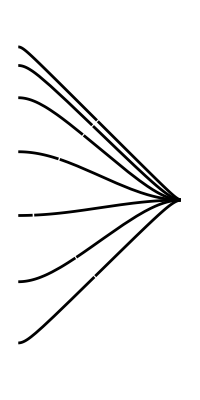

```mathematica
phlminkcauchy=ParametricPlot[hlistminkcauchy,{r,0,100},PlotRange->{{0,π/2},{-π/2,π/2}},Ticks->None,PlotStyle->colourminkcauchy,BaseStyle->{FontSize->labe-2},Axes->None, PlotPoints->200]
```

```mathematica
Show[phlminkcauchy,phlNScauchy,nsradius,covermin,lettersmin,PlotRange->{{0,π/2+0.3},{-π/2-0.3,π/2+0.3}},ImageSize->{260,450},Epilog->makePlotLegend[{MaTeX["\\textrm{Minkowski}",Magnification->1.7],MaTeX["\\textrm{NS}",Magnification->1.7]},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{Directive[Black],myblue},{0.40,0.18},labe-2,labe-2,"Times"]]
```

-Graphics-

#### Hyperboloidal slices for single NS

```mathematica
(*construction for Minkowski including height function*)
hfMink[r_]=Sqrt[(3/Kcmcset)^2+r^2]+3/Kcmcset;
thsMink = {t -> t +hfMink[r]};
uf = t - r; vf = t + r;
Uf = ArcTan[uf]; Vf = ArcTan[vf];
Tf = (Uf + Vf)/2; Rf =( Vf - Uf)/2;
listttfMink[tval_] = {Rf, Tf} /. thsMink/. {t -> tval}//Evaluate;
```

```mathematica
npoints=10;npoints2=20;
Table[N[{rp,NIntegrate[hpin[r],{r,0,rp},AccuracyGoal->accdef,PrecisionGoal->precdef,WorkingPrecision->wpdef]}/.rp->0+ci(rsunco-0)/npoints,{Infinity,5accdef}],{ci,0,npoints}]
Timing[Table[N[{rp,NIntegrate[hpNS[r],{r,0,rp},AccuracyGoal->accdef,PrecisionGoal->precdef,WorkingPrecision->wpdef]}/.rp->rsunco+ci(6-rsunco)/npoints2,{Infinity,5accdef}],{ci,1,npoints2}]]
Timing[Table[N[{rp,NIntegrate[hpNS[r],{r,0,rp},AccuracyGoal->accdef,PrecisionGoal->precdef,WorkingPrecision->wpdef]}/.rp->6+ci(100-6)/npoints2,{Infinity,5accdef}],{ci,1,npoints2}]]
hpoints=Flatten[{%%%,%%[[2]],%[[2]]},1]
hinter=Interpolation[hpoints];
```

NIntegrate::nlim: r = rp is not a valid limit of integration.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.04813154434576107841300024848071969797431692649362170115144814200886586420565982359285086817256789386}. NIntegrate obtained 0.0114946137583074648776743062396671491534710862011671217961210067193385937373320180312362977035036745 and 1.950836646319220148178705367882796862751547125812868018604677389000555858558351335711035371066769972×10^-16 for the integral and error estimates.

NIntegrate::nlim: r = rp is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.1112895543134750339422654973195848855778584814429116357356199885686553722021336340704607336914239862}. NIntegrate obtained 0.04473375335915798305333973011072045798014011006340721127785788297262756002151059756289888318218410865 and 2.901362196212242864119057396226423943615149444911314681462085076373871334775527961195429989771239738×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.1443946330372832352390007454421590939229507794808651034543444260265975926169935040772694686385361467}. NIntegrate obtained 0.09670048890310727816800449337094183352393669118335554254114466345914858584880271259153906883594719147 and 1.329535469478488904964652866751936471818378465442313229394012903779257455102361519444413892552984319×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.,0.},{0.060105862487811508465060001432581958516898513822673,0.011494613758307464877674306239667149153471086201167},{0.12021172497562301693012000286516391703379702764535,0.044733753359157983053339730110720457980140110063407},{0.18031758746343452539518000429774587555069554146802,0.096700488903107278168004493370941833523936691183356},{0.24042344995124603386024000573032783406759405529069,0.1640901039381420125593353309840835772530261889422},{0.30052931243905754232530000716290979258449256911336,0.24435042702515681376950826932477108902685597445681},{0.36063517492686905079036000859549175110139108293604,0.33558876266390791887635352186006615134365371596643},{0.42074103741468055925542001002807370961828959675871,0.43534644326242877117008328364226675333511511021081},{0.48084689990249206772048001146065566813518811058138,0.53923298811702269677858910844391892682891703888864},{0.54095276239030357618554001289323762665208662440406,0.64152315066383298359550476883646014021640690243135},{0.60105862487811508465060001432581958516898513822673,0.73776707486417981459954905035973296327140624400328}}

NIntegrate::nlim: r = rp is not a valid limit of integration.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.3944436890806957133015954514866683678242143816768845793065430949436187632864377816442550794894609094}. NIntegrate obtained 1.105704226008681407908661041367821706680344938353587485993625585453543343472453624040588184726131465 and 1.013547427313075812036222001212113174189516413856776435352755899141324475953624577650615898494158117×10^-12 for the integral and error estimates.

NIntegrate::nlim: r = rp is not a valid limit of integration.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.3944436890806957133015954514866683678242143816768845793065430949436187632864377816442550794894609094}. NIntegrate obtained 1.433711917552664021088890481056207469136752543999544797666789586501535145299881244569294856706209738 and 1.013547903979302578300736151840225496015100780220646545781645663616840028392864989191490092190018297×10^-12 for the integral and error estimates.

NIntegrate::nlim: r = rp is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.3944436890806957133015954514866683678242143816768845793065430949436187632864377816442550794894609094}. NIntegrate obtained 1.748088569704112748607722367898752059719603098324267968247115577380161894586150238042504076271333026 and 1.014035601617902657970613714671410718662158325548676358784391079055774719434960761439713634952396149×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{27.3081,{{0.87100569363420933041807001360952860591053588131539,1.1057042260086814079086610413678217066803449383536},{1.1409527623903035761855400128932376266520866244041,1.4337119175526640210888904810562074691367525439995},{1.4108998311463978219530100121769466473936373674927,1.7480885697041127486077223678987520597196030983243},{1.6808468999024920677204800114606556681351881105814,2.0557053875404721080636731851438084882765909938729},{1.95079396865858631348795001074436468887673885367,2.3591028671477903055038713210793905041175633698164},{2.2207410374146805592554200100280737096182895967587,2.6594561657744560670622365896749030075869981602047},{2.4906881061707748050228900093117827303598403398474,2.9574142333367649901412790450631725841609926008157},{2.760635174926869050790360008595491751101391082936,3.253388996160610340813626027322627194584647596796},{3.0305822436829632965578300078792007718429418260247,3.5476701164685040726244745014697849271231005800867},{3.3005293124390575423253000071629097925844925691134,3.8404762375836265239862176933811327286281727807241},{3.570476381195151788092770006446618813326043312202,4.1319804445735310749274934932250754749322837309263},{3.8404234499512460338602400057303278340675940552907,4.422324221114822920369982357915282906336888671644},{4.1103705187073402796277100050140368548091447983794,4.7116258082214198454790412663812527088138576771989},{4.380317587463434525395180004297745875550695541468,4.9999856064360159834031175949904644206835593138283},{4.6502646562195287711626500035814548962922462845567,5.2874898923076134710982212622752974261857909445443},{4.9202117249756230169301200028651639170337970276453,5.5742135043318487058546184309814960337993886395883},{5.190158793731717262697590002148872937775347770734,5.8602218591898744502667629688295297533676804331657},{5.4601058624878115084650600014325819585168985138227,6.1455725097529810704657980659566057741117645590297},{5.7300529312439057542325300007162909792584492569113,6.430316376045111284256729400211812751665825397443},{6.,6.714498734776004100181237178195782107002646054746}}}

NIntegrate::nlim: r = rp is not a valid limit of integration.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.3944436890806957133015954514866683678242143816768845793065430949436187632864377816442550794894609094}. NIntegrate obtained 11.60173931788691237056034275331756122134803496336365469331734243705872221937640959049578410074680319 and 1.013555197716707542615921019784099864735368031071906976262971075897347912516032492882429138495325342×10^-12 for the integral and error estimates.

NIntegrate::nlim: r = rp is not a valid limit of integration.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.3944436890806957133015954514866683678242143816768845793065430949436187632864377816442550794894609094}. NIntegrate obtained 16.42558673936061247428145945773579877750816907276751243621653076329298722526912929445470274067132953 and 1.017353640127344006395877342508964738042433781220813435151446730994574453654334230217248278482177396×10^-12 for the integral and error estimates.

NIntegrate::nlim: r = rp is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.3944436890806957133015954514866683678242143816768845793065430949436187632864377816442550794894609094}. NIntegrate obtained 21.21818018865301986301449167620085099144524390760877568702431532419599255084130444935976493245845933 and 1.013547614623012959049057543197507044695689353019058923468081574198596703133956868117871653756349941×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{25.2294,{{10.7,11.601739317886912370560342753317561221348034963364},{15.4,16.425586739360612474281459457735798777508169072768},{20.1,21.218180188653019863014491676200850991445243907609},{24.8,25.99213505929099239165682014162622912387986995144},{29.5,30.753704763658283364678501724636577276900290561823},{34.2,35.50644554611025599581177435342276944968830677511},{38.9,40.252573402812079389926409568138907530582857889437},{43.6,44.993562679265478314442765154601738739118782206319},{48.3,49.73044392940850368260152269769545106730054007688},{53.,54.463965842781048217069340897301686559960638479991},{57.7,59.19468947298731781677680929736415627539255986363},{62.4,63.92304611821579658487876061955951441838991696802},{67.1,68.649374477100221980747298867693912711655324841972},{71.8,73.373945391143336598556084146345030095868022931918},{76.5,78.096978839412414990715300494964685246219240319612},{81.2,82.81865592562607146133973931200647647874731160519},{85.9,87.539127529943452953832021000435114103249980622107},{90.6,92.258520680494571948627302916352381311731458917657},{95.3,96.976943329793215877218028669439064902544065967659},{100.,101.69448799243336388976651992090621902761701272613}}}

{{0.,0.},{0.060105862487811508465060001432581958516898513822673,0.011494613758307464877674306239667149153471086201167},{0.12021172497562301693012000286516391703379702764535,0.044733753359157983053339730110720457980140110063407},{0.18031758746343452539518000429774587555069554146802,0.096700488903107278168004493370941833523936691183356},{0.24042344995124603386024000573032783406759405529069,0.1640901039381420125593353309840835772530261889422},{0.30052931243905754232530000716290979258449256911336,0.24435042702515681376950826932477108902685597445681},{0.36063517492686905079036000859549175110139108293604,0.33558876266390791887635352186006615134365371596643},{0.42074103741468055925542001002807370961828959675871,0.43534644326242877117008328364226675333511511021081},{0.48084689990249206772048001146065566813518811058138,0.53923298811702269677858910844391892682891703888864},{0.54095276239030357618554001289323762665208662440406,0.64152315066383298359550476883646014021640690243135},{0.60105862487811508465060001432581958516898513822673,0.73776707486417981459954905035973296327140624400328},{0.87100569363420933041807001360952860591053588131539,1.1057042260086814079086610413678217066803449383536},{1.1409527623903035761855400128932376266520866244041,1.4337119175526640210888904810562074691367525439995},{1.4108998311463978219530100121769466473936373674927,1.7480885697041127486077223678987520597196030983243},{1.6808468999024920677204800114606556681351881105814,2.0557053875404721080636731851438084882765909938729},{1.95079396865858631348795001074436468887673885367,2.3591028671477903055038713210793905041175633698164},{2.2207410374146805592554200100280737096182895967587,2.6594561657744560670622365896749030075869981602047},{2.4906881061707748050228900093117827303598403398474,2.9574142333367649901412790450631725841609926008157},{2.760635174926869050790360008595491751101391082936,3.253388996160610340813626027322627194584647596796},{3.0305822436829632965578300078792007718429418260247,3.5476701164685040726244745014697849271231005800867},{3.3005293124390575423253000071629097925844925691134,3.8404762375836265239862176933811327286281727807241},{3.570476381195151788092770006446618813326043312202,4.1319804445735310749274934932250754749322837309263},{3.8404234499512460338602400057303278340675940552907,4.422324221114822920369982357915282906336888671644},{4.1103705187073402796277100050140368548091447983794,4.7116258082214198454790412663812527088138576771989},{4.380317587463434525395180004297745875550695541468,4.9999856064360159834031175949904644206835593138283},{4.6502646562195287711626500035814548962922462845567,5.2874898923076134710982212622752974261857909445443},{4.9202117249756230169301200028651639170337970276453,5.5742135043318487058546184309814960337993886395883},{5.190158793731717262697590002148872937775347770734,5.8602218591898744502667629688295297533676804331657},{5.4601058624878115084650600014325819585168985138227,6.1455725097529810704657980659566057741117645590297},{5.7300529312439057542325300007162909792584492569113,6.430316376045111284256729400211812751665825397443},{6.,6.714498734776004100181237178195782107002646054746},{10.7,11.601739317886912370560342753317561221348034963364},{15.4,16.425586739360612474281459457735798777508169072768},{20.1,21.218180188653019863014491676200850991445243907609},{24.8,25.99213505929099239165682014162622912387986995144},{29.5,30.753704763658283364678501724636577276900290561823},{34.2,35.50644554611025599581177435342276944968830677511},{38.9,40.252573402812079389926409568138907530582857889437},{43.6,44.993562679265478314442765154601738739118782206319},{48.3,49.73044392940850368260152269769545106730054007688},{53.,54.463965842781048217069340897301686559960638479991},{57.7,59.19468947298731781677680929736415627539255986363},{62.4,63.92304611821579658487876061955951441838991696802},{67.1,68.649374477100221980747298867693912711655324841972},{71.8,73.373945391143336598556084146345030095868022931918},{76.5,78.096978839412414990715300494964685246219240319612},{81.2,82.81865592562607146133973931200647647874731160519},{85.9,87.539127529943452953832021000435114103249980622107},{90.6,92.258520680494571948627302916352381311731458917657},{95.3,96.976943329793215877218028669439064902544065967659},{100.,101.69448799243336388976651992090621902761701272613}}

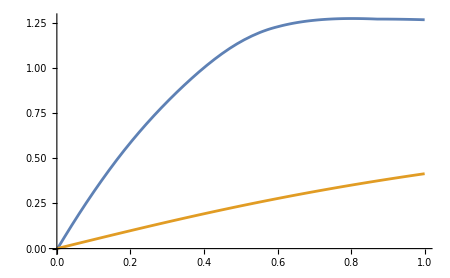
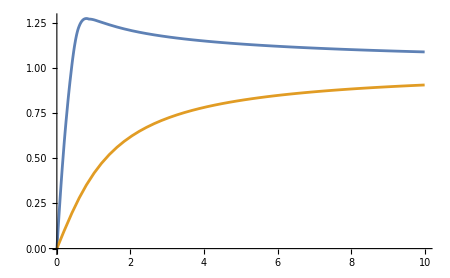
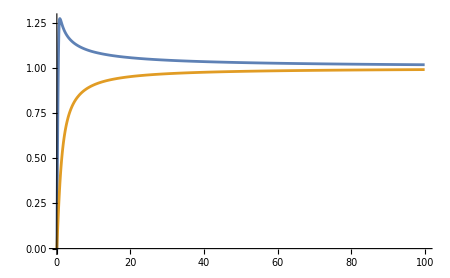

```mathematica
(*comparison to Minkowski*)
{Plot[{hinter[r]/r,hfMink[r]/r},{r,0,1},PlotRange->All,ImageSize->450],Plot[{hinter[r]/r,hfMink[r]/r},{r,0,10},PlotRange->All,ImageSize->450],Plot[{hinter[r]/r,hfMink[r]/r},{r,0,100},PlotRange->All,ImageSize->450]}
```

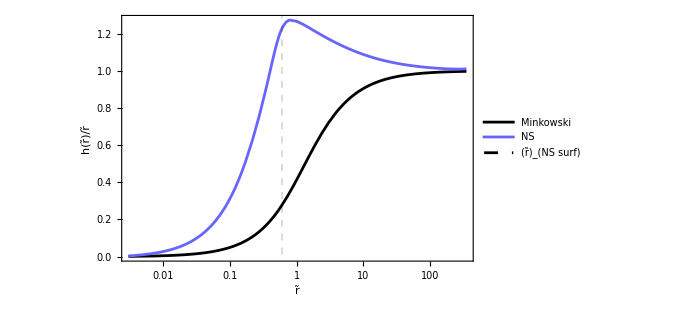

```mathematica
LogLinearPlot[{hfMink[r]/r,hinter[r]/r,},{r,0.003,350},PlotRange->All,ImageSize->500,PlotStyle->{{Black},{myblue},Directive[Black,Dashed,Thin]},ImageSize->500,Frame->True,FrameLabel->{"r̃","h(r̃)/r̃"},BaseStyle->{FontSize->15,FontFamily->"Times",FontColor->Black},FrameStyle->Black,AxesStyle->Black,PlotLegends->Placed[Map[Style[#,15,FontFamily->"Times"]&,{"Minkowski","NS","(r̃)_(NS surf)"}],{0.78,0.35}],GridLines->{{{rsunco,Directive[Black,Dashed,Thin]}},{}}]
```

```mathematica
(*construction for NS including height function*)
hfNS[r_]=hinter[r];
thsNS = {t -> t +hfNS[r]};
uf = t - rtortNS[r]; vf = t + rtortNS[r];
Uf = ArcTan[uf]; Vf = ArcTan[vf];
Tf = (Uf + Vf)/2; Rf =( Vf - Uf)/2;
listrfNS[rval_] = {Rf, Tf} /. {r -> rval}//Evaluate;
listttfNS[tval_] = {Rf, Tf} /. thsNS/. {t -> tval}//Evaluate;
```

```mathematica
colourns=myblue;
```

```mathematica
hlistNS=Map[listttfNS[#]&,{10,3.5,1.5,0.5,-0.15,-1,-5}];
```

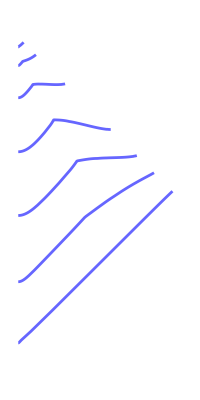

```mathematica
phlNS=ParametricPlot[hlistNS,{r,0,100},PlotRange->{{0,π/2},{-π/2,π/2}},Ticks->None,PlotStyle->colourns,BaseStyle->{FontSize->labe-2},Axes->None, PlotPoints->200]
```

```mathematica
nsradius=ParametricPlot[listrfNS[rsunco], {t, -100, 100},   PlotRange -> {{0, π/2}, {-π/2, π/2}}, Ticks -> None, Axes -> None,   PlotStyle -> {{Black,Thick,Dashed}},PlotPoints->200];
```

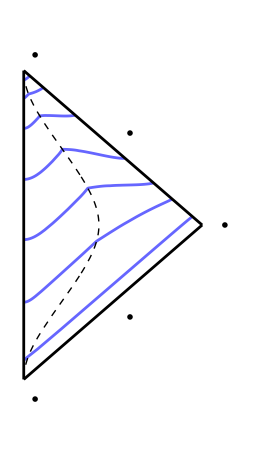

```mathematica
Show[phlNS,nsradius,covermin,lettersmin,PlotRange->{{0,π/2+0.3},{-π/2-0.3,π/2+0.3}},ImageSize->{260,450}]
```

```mathematica
colourmink=Black;
```

```mathematica
hlistMink=Map[listttfMink[#]&,{10,3.5,1.5,0.5,-0.15,-1,-5}];
```

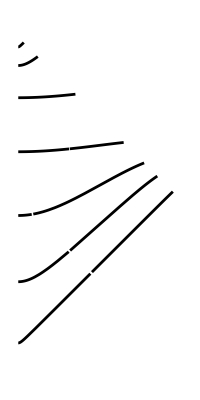

```mathematica
phlmink=ParametricPlot[hlistMink,{r,0,100},PlotRange->{{0,π/2},{-π/2,π/2}},Ticks->None,PlotStyle->colourmink,BaseStyle->{FontSize->labe-2},Axes->None, PlotPoints->200]
```

```mathematica
Show[phlmink,phlNS,nsradius,covermin,lettersmin,PlotRange->{{0,π/2+0.3},{-π/2-0.3,π/2+0.3}},ImageSize->{260,450},Epilog->makePlotLegend[{MaTeX["\\textrm{Minkowski}",Magnification->1.7],MaTeX["\\textrm{NS}",Magnification->1.7]},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{Directive[Black],myblue},{0.40,0.18},labe-2,labe-2,"Times"]]
```

-Graphics-

#### Calculating tortoise coordinate for superposition

```mathematica
(*visualizing behaviour of tortoise coordinate for Schwarzschild*)
{rp+2mass Log[1-rp/(2mass)],rp+2mass Log[rp/(2mass)-1]}/.mass->1//Evaluate;
Plot[%//Evaluate,{rp,0,4},ImageSize->500]
```

-Graphics-

```mathematica
(*calculation of tortoise coordinate for superposition*)
closehor=0.0005`50;
rtin=NDSolve[{rt'[rp]==1/oneovergrrarealradiusdp[rp],rt[0]==0},rt,{rp,0,newruncodp}][[1,1,2]]
rtout=NDSolve[{rt'[rp]==1/oneovergrrarealradiusdp[rp],rt[newruncodp+closehor]==rtin[newruncodp-closehor (*added a two here to improve the output -- may have to take away for other cases*)]},rt,{rp,newruncodp,rsuncofromisodp}][[1,1,2]]
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nbnum1: The function value 0.417159-0.000038788 ⅈ is not True or False when the arguments are {0.,0.+0. ⅈ,9.10597×10^-6+0. ⅈ,1,1,-1,-1,1}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

NDSolve::ecboo: The value of event condition function at rp = 0. was not True or False. The event will be considered inactive.

NDSolve::ecboo: The value of event condition function at rp = 0.0000179515 was not True or False. The event will be considered inactive.

NDSolve::ecboo: The value of event condition function at rp = 0.000035903 was not True or False. The event will be considered inactive.

General::stop: Further output of NDSolve::ecboo will be suppressed during this calculation.

NDSolve::ndsz: At rp == 0.174847, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0^2 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {rp,rt[rp],NDSolve`s$394526[rp],NDSolve`s$396278[rp],NDSolve`s$394524[rp],NDSolve`s$396279[rp],NDSolve`s$394525[rp]} = {0.174883,-3310.1,1,-1,1,1,1}.

InterpolatingFunction::dmval: Input value {0.606668} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction[…]

```mathematica
(*plotting in comparison to Schwarzschild with similar mass*)
Plot[{rtin[rp],rtout[rp],rp+2mass Log[1-rp/(2mass)],rp+2mass Log[rp/(2mass)-1]}/.mass->newruncodp/2//Evaluate,{rp,0,rsuncofromisodp/1.5},PlotRange->{-1.3,1.3}]
```

InterpolatingFunction::dmval: Input value {8.26223×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
(*setting integration constant such that the asymptotic behaviour of the tortoise coordinate is that of Schwarzschild with the same mass*)
rp+2mass Log[rp-(2mass)]+Dd/.mass->massBH+msunco+2Avalsol
rtout[rsuncofromisodp]//Chop
Solve[%==%%/.rp->rsuncofromisodp]
rasym[rp_]=%%%/.%[[1,1]]
```

Dd+rp+0.3772551129371598500889565726038915080631135898278 Log[-0.3772551129371598500889565726038915080631135898278+rp]

InterpolatingFunction::dmval: Input value {0.6066675894880070347992882367900098428777367653056} lies outside the range of data in the interpolating function. Extrapolation will be used.

1.27205

{{Dd→1.22079}}

1.22079+rp+0.3772551129371598500889565726038915080631135898278 Log[-0.3772551129371598500889565726038915080631135898278+rp]

```mathematica
rtboth[rp_]=Piecewise[{{rtin[rp],rp<=newruncodp},{rtout[rp],newruncodp<rp<rsuncofromisodp},{rasym[rp],rsuncofromisodp<=rp}}]
```

Piecewise[{{InterpolatingFunction[…][rp], rp≤0.1748830936617506714256753190666675263394}, {InterpolatingFunction[…][rp], 0.1748830936617506714256753190666675263394<rp<0.6066675894880070347992882367900098428777367653056}, {1.22079+rp+0.3772551129371598500889565726038915080631135898278 Log[-0.3772551129371598500889565726038915080631135898278+rp], 0.6066675894880070347992882367900098428777367653056≤rp}, {0, True}}]

```mathematica
Plot[rtboth[rp],{rp,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Plot[Re@{rtboth[r],,}//Evaluate,{r,0,1},PlotRange->All,ImageSize->500,PlotStyle->{{Black},Directive[Black,Dashed,Thin],Directive[Black,DotDashed,Thin]},ImageSize->500,Frame->True,FrameLabel->{"r̃","(r̃)_*"},BaseStyle->{FontSize->15,FontFamily->"Times",FontColor->Black},FrameStyle->Black,AxesStyle->Black,PlotLegends->Placed[Map[Style[#,15,FontFamily->"Times"]&,{ "NS+BH+δψ","(r̃)_(NS surf)","(r̃)_BH"}],{0.82,0.36}],GridLines->{{{rsuncofromisodp,Directive[Black,Dashed,Thin]},{newruncodp,Directive[Black,DotDashed,Thin]}},{}}]
```

-Graphics-

```mathematica
(*seeing the effect of varying B with Schwarzschild*)
(1-2mass/rp)Exp[-2(rp+2mass Log[rp/(2mass)-1])/B];
Plot[{%/.B->4mass,%/.B->2mass,%/.B->6mass}/.mass->1//Evaluate,{rp,1.5,2.5}]
```

-Graphics-

```mathematica
oneovergrrarealradiusdp[rp]Piecewise[{{-Exp[-2rtboth[rp]/( 2newruncodp(*4mass*))],rp<newruncodp},{Exp[-2rtboth[rp]/( 2newruncodp)],rp>newruncodp}}];
Plot[%,{rp,0,2newruncodp}]
Style["The correct value for B is indeed 4 mBH, which can be calculated from the MSmass at origin, or as half the Schwarzschild radius of the spacetime.",Blue,18]
```

-Graphics-

The correct value for B is indeed 4 mBH, which can be calculated from the MSmass at origin, or as half the Schwarzschild radius of the spacetime.

```mathematica
massBH
newruncodp/2
msmcauchy/.χ->Function[{r},(ψtot[r]+δψsol[r])^-4]/.r->10^-6
```

0.06136265574214498126111957157548643850788919872847

0.08744154683087533571283765953333376316971

0.08749540077050462821047132268968488359

#### Cauchy slices for superposition

```mathematica
bothsubs={rtortphys->rtboth[r],B-> 2newruncodp(*4mass*)};
scafac=1;
```

```mathematica
(*Kruskal-Szekeres coordinates.*)
uso =Exp[rtortphys/B]Cosh[t/B]/.bothsubs;vso =Exp[rtortphys/B]Sinh[t/B]/.bothsubs; (*set -rhs for symmetric spacetime*)
usi =Exp[rtortphys/B]Sinh[t/B]/.bothsubs;vsi =Exp[rtortphys/B]Cosh[t/B]/.bothsubs;(*set -rhs for white hole*)
Uso = ArcTan[(uso+vso)/scafac]; Vso = ArcTan[(uso-vso)/scafac];
Usi = ArcTan[(usi+vsi)/scafac]; Vsi = ArcTan[(usi-vsi)/scafac];
Tso = (Uso - Vso)/2; Rso = (Uso+Vso)/2;
Tsi = (Usi - Vsi)/2; Rsi = (Usi+Vsi)/2;
listrfo[rval_] =Re@{Rso, Tso} /. {r -> rval}//Evaluate;
listtfo[tval_] =Re@ {Rso, Tso} /. {t -> tval}//Evaluate;
listrfi[rval_] =Re@ {Rsi, Tsi} /. {r -> rval}//Evaluate;
listtfi[tval_] =Re@ {Rsi, Tsi} /. {t -> tval}//Evaluate;
(*added Re@, but they should be real anyway*)
```

```mathematica
colourbothcauchy=Directive[Black];
```

```mathematica
listttt={1,0.5,0.3,0.15,0,-0.15,-0.3,-0.5,-1};
hlisto=Map[listtfo[#]&,listttt];
hlisti=Map[listtfi[#]&,listttt];
```

```mathematica
nsradiusboth=ParametricPlot[listrfo[rsuncofromisodp], {t, -10, 10},   PlotRange -> {{0, π/2}, {-π/4, π/4}}, Ticks -> None, Axes -> None,PlotStyle ->{{Black,Thick,Dashed}},PlotPoints->200]
```

-Graphics-

```mathematica
bothcauchy=Show[{ParametricPlot[hlisto//Evaluate,{r,newruncodp+closehor/100,20},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->colourbothcauchy,Axes->None,PlotPoints->250],ParametricPlot[hlisti//Evaluate,{r,0,newruncodp-closehor/100},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->colourbothcauchy,Axes->None]}]
```

-Graphics-

```mathematica
Show[{lettersschw,bothcauchy,nsradiusboth,coverschw}, ImageSize->500]
```

-Graphics-

#### Hyperboloidal slices for superposition

```mathematica
Normal@Series[aconftotalldp[r],{r,0,1}];
r/%/.r->0.000002
inmstRdp=%(*taking this as the location of the trumpet in terms of the Schwarzschild-type uncompactified areal radial coordinate*)
1/D[aconftotalldp[r],r]/.r->0.000002
```

InterpolatingFunction::dmval: Input value {2.×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.144838

0.144838

InterpolatingFunction::dmval: Input value {2.×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.144822

```mathematica
(*behaviour near the origin for the compactification factors of the BH and the superposition*)
Plot[{lilu[r],aconftotalldp[r],r/inmstR,r/inmstRdp },{r,0,0.01}]
```

InterpolatingFunction::dmval: Input value {2.04286×10^-7} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
rphyshornum=newruncodp;(*location of the horizon*)
rphystrum=inmstRdp;(*location of the trumpet*)
rphysNS=rsuncofromisodp;(*location of the NS's surface*)
rphysmax=1000;(*maximum value of the radius up to which the integration is performed*)
```

```mathematica
(*integration of the height function*)
closehorpen=closehor; (*if smaller, slices do not match well at the horizon*)
part[rp]/Aadpinterior/Sqrt[Aadpinterior+part[rp]^2]/.Kcmc->Kcmcset/.Ccmc->Ccmcvalsuperpdp/.rp->r;
NDSolve[{%==hfu'[r],hfu[rphyshornum-closehorpen]==0},hfu,{r,rphystrum+closehorpen/2,rphyshornum-closehorpen}]
Plot[%[[1,1,2]][r],{r,rphystrum,rphyshornum}];
part[rp]/Aadp/Sqrt[Aadp+part[rp]^2]/.Kcmc->Kcmcset/.Ccmc->Ccmcvalsuperpdp/.rp->r;
NDSolve[{%==hfu'[r],hfu[rphyshornum+closehorpen]==0},hfu,{r,rphyshornum+closehorpen,rphysNS}]
Plot[%[[1,1,2]][r],{r,rphyshornum,rphysNS}];
-(Kcmc rp/3+Ccmc/rp^2)/(1-2M/rp)/Sqrt[(1-2M/rp)+(Kcmc rp/3+Ccmc/rp^2)^2]/.M->msunco+massBH+2 Avalsol/.Kcmc->Kcmcset/.Ccmc->Ccmcvalsuperpdp/.rp->r;
NDSolve[{%==hfu'[r],hfu[rphysNS]==%%%[[1,1,2]][rphysNS]},hfu,{r,rphysNS,rphysmax}]
Plot[%[[1,1,2]][r],{r,rphysNS,2}];
Show[{%%%%%%%,%%%%,%},PlotRange->{{rphystrum,2},Automatic}]
hnumcomp[r_]=Piecewise[{{%%%%%%%%%[[1,1,2]][r],r<rphyshornum},{%%%%%%[[1,1,2]][r],rphyshornum<r<rphysNS},{%%%[[1,1,2]][r],rphysNS<r}}];
Plot[hnumcomp[rphys],{rphys,rphystrum,5},AxesLabel->{"rphys", "h[rphys]"},PlotRange->{-1.5,4},PlotPoints->200]
```

{{hfu→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.144838} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.606668} lies outside the range of data in the interpolating function. Extrapolation will be used.

{{hfu→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.174892} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.6066675894880070347992882367900098428777367653056} lies outside the range of data in the interpolating function. Extrapolation will be used.

{{hfu→InterpolatingFunction[…]}}

-Graphics-

InterpolatingFunction::dmval: Input value {0.144862} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
{Plot[hnumcomp[rphys],{rphys,rphystrum,5},AxesLabel->{"rphys", "h[rphys]"},PlotRange->{-2,4},PlotPoints->200,ImageSize->400],Plot[hnumcomp[rphys],{rphys,rphystrum,rphysNS},AxesLabel->{"rphys", "h[rphys]"},PlotRange->{-1,1},PlotPoints->200,ImageSize->400]}
```

InterpolatingFunction::dmval: Input value {0.144862} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.14484} lies outside the range of data in the interpolating function. Extrapolation will be used.

{-Graphics-,-Graphics-}

```mathematica
Plot[hnumcomp[rphys]/rphys,{rphys,rphystrum,1000},AxesLabel->{"rphys", "h[rphys]"},PlotRange->{-0.5,2},PlotPoints->200]
```

-Graphics-

```mathematica
closehorpen=closehor/2; (*if smaller, slices do not match well at the horizon*)
part[rp]/Aadpinterior/Sqrt[Aadpinterior+part[rp]^2]/.Kcmc->Kcmcset/.Ccmc->Ccmcvalsuperpdp/.rp->r;
NDSolve[{%==hfu'[r],hfu[rphyshornum-closehorpen]==0},hfu,{r,rphystrum+closehorpen,rphyshornum}]
Plot[%[[1,1,2]][r],{r,rphystrum,rphyshornum}];
part[rp]/Aadp/Sqrt[Aadp+part[rp]^2]/.Kcmc->Kcmcset/.Ccmc->Ccmcvalsuperpdp/.rp->r;
NDSolve[{%==hfu'[r],hfu[rphyshornum+closehorpen]==0},hfu,{r,rphyshornum+closehorpen,rphysNS}]
Plot[%[[1,1,2]][r],{r,rphyshornum,rphysNS}];
-(Kcmc rp/3+Ccmc/rp^2)/(1-2M/rp)/Sqrt[(1-2M/rp)+(Kcmc rp/3+Ccmc/rp^2)^2]/.M->msunco+massset+2 Avalsol/.Kcmc->Kcmcset/.Ccmc->Ccmcvalsuperpdp/.rp->r;
NDSolve[{%==hfu'[r],hfu[rphysNS]==%%%[[1,1,2]][rphysNS]},hfu,{r,rphysNS,rphysmax}]
Plot[%[[1,1,2]][r],{r,rphysNS,2}];
Show[{%%%%%%%,%%%%,%},PlotRange->{{rphystrum,2},Automatic}]
hnumcomp[r_]=Piecewise[{{%%%%%%%%%[[1,1,2]][r],r<rphyshornum},{%%%%%%[[1,1,2]][r],rphyshornum<r<rphysNS},{%%%[[1,1,2]][r],rphysNS<r}}];
Plot[hnumcomp[rphys],{rphys,rphystrum,5},AxesLabel->{"rphys", "h[rphys]"},PlotRange->{-0.5,4},PlotPoints->200]
```

NDSolve::ndsz: At r == 0.0366599, step size is effectively zero; singularity or stiff system suspected.

{{hfu→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.0277097} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.754971} lies outside the range of data in the interpolating function. Extrapolation will be used.

{{hfu→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.0366745} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.7549709595986864949468469840609178855478825439302} lies outside the range of data in the interpolating function. Extrapolation will be used.

{{hfu→InterpolatingFunction[…]}}

-Graphics-

InterpolatingFunction::dmval: Input value {0.0277345} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
(*construction for superposition including the height function*)
hfboth[r_]=hnumcomp[r];
thsboth= {t -> t +hfboth[r]};
listrfo[rval_] =Re@{Rso, Tso} /. {r -> rval}//Evaluate;
listttfo[tval_] =Re@ {Rso, Tso} /.thsboth/. {t -> tval}//Evaluate;
listrfi[rval_] =Re@ {Rsi, Tsi} /. {r -> rval}//Evaluate;
listttfi[tval_] =Re@ {Rsi, Tsi} /.thsboth/. {t -> tval}//Evaluate;
(*added Re@, but they should be real anyway*)
```

```mathematica
colourbothhyp=Directive[Black];
```

```mathematica
listtttt={2,1.2,1,0.8,0.5,0.15};
hlistto=Map[listttfo[#]&,listtttt];
hlistti=Map[listttfi[#]&,listtttt];
```

```mathematica
nsradiusboth=ParametricPlot[listrfo[rsuncofromisodp], {t, -5, 5},   PlotRange -> {{0, π/2}, {-π/4, π/4}}, Ticks -> None, Axes -> None,PlotStyle ->{{Black,Thick,Dashed}},PlotPoints->200]
Style["This will barely be seen in the diagram, unless the value of B is increased.",Red,18]
```

-Graphics-

This will barely be seen in the diagram, unless the value of B is increased.

```mathematica
bothhyp=Show[{ParametricPlot[hlistto//Evaluate,{r,rphyshornum+closehorpen ,2},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->colourbothhyp,Axes->None,PlotPoints->250],ParametricPlot[hlistti//Evaluate,{r,rphystrum-closehorpen,rphyshornum-closehorpen},PlotRange->{{-π/4,π/2},{-π/4,π/4}},Ticks->None,PlotStyle->colourbothhyp,Axes->None,PlotPoints->250]}]//Quiet
```

-Graphics-

```mathematica
Show[{lettersschw,bothhyp,nsradiusboth,coverschw},Epilog->makePlotLegend[{MaTeX["\\textrm{NS}+\\textrm{BH}+\\delta\\psi",Magnification->1.8]}(*}]*),(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{colourbothhyp},{0.08,0.24},labe-2,labe-2,"Times"], ImageSize->500]
```

-Graphics-